```mathematica
(* Pre-processing *)
1+1;
ParallelTable[i,{i,6}];
AppendTo[$Path,NotebookDirectory[]];
```

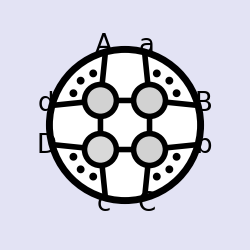
-Graphics-
One-Loop Amplitude Integrands
and Integrals in N=4 SYM
Jacob L. Bourjaily, 2013

i::shdw: Symbol i appears in multiple contexts {Global`,MathCompile`}; definitions in context Global` may shadow or be shadowed by other definitions.

i$::shdw: Symbol i$ appears in multiple contexts {Global`,MathCompile`}; definitions in context Global` may shadow or be shadowed by other definitions.

```mathematica
n=9;
<<"loop_amplitudes.m";
(* fun *)
ab[___,j_,___,j_,___]:=0;
sortab={i_ab:>ordercup[i]Signature[i]/Signature[ordercup[i]]};
sortdoubleab={i_doubleab:>Sort[i]Signature[i]/Signature[Sort[i]]};
sortcapinR=R[a__]:>R@@(Replace[List[a],cap[x_,y_]:>cap[ordercup@x,ordercup[y]],{0,Infinity}]);
Qlog[1]:=0;
Dmatrix[0]=0;
doubleab[___,j_,___,j_,___]:=0;
Dmatrix[ab[x__]y_]:=ab[x]Dmatrix[y];
FuseDmatrices:=Expand[#]//.{Dmatrix[i_]Dmatrix[j_]:>Dmatrix@Join[i,j]}&;
abelim={ab[x___,n+1,y___]:>ab[x,n,y]-e ab[x,B,y]};
abtre= ab[aa___,B,bb___]:>ab[aa,n-1,bb]-τ ab[aa,1,bb](ab[n-1,n,2,3]/ab[n,1,2,3])-e ab[aa,2,bb](ab[n-2,n-1,n,1]/ab[n-2,n-1,2,1]);
capexpand = {ab[x___, cap[{a_, b_}, {c__}], y___] :> ab[b, c] ab[x, a, y] + ab[c, a] ab[x, b, y],
               ab[x___,cap1[{a_,b_},{c__},{d__}],y___]:>(-1)^Length[{y}](ab[x,y,a,c]ab[x,y,b,d]-ab[x,y,a,d]ab[x,y,b,c]),
               ab[a___,cap2[{c_,d_,e_},{f_,g_,h_}],b___]:>ab[a,c,d,b]ab[e,f,g,h]+ab[a,d,e,b]ab[c,f,g,h]+ab[a,e,c,b]ab[d,f,g,h]};
shifexp={ab[x___,shift[y_,z_],w___]:>ab[x,y⟦1⟧,w]+z ab[x,y⟦2⟧,w]};
mom=RandomInteger[{-100,100},{20,4}];
mom1=Table[Binomial[n+i,i],{n,20},{i,0,3}];
neab[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom[[{x}]]];
neab1[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom1[[{x}]]];
todmatrix:=FuseDmatrices[#/.i_R:>(fromRform[n+1][i][[1,1]])Dmatrix[fromRform[n+1][i][[1,2]]]//.shifexp//.capexpand]&;
todmatrixn:=FuseDmatrices[#/.i_R:>(fromRform[n][i][[1,1]])Dmatrix[fromRform[n][i][[1,2]]]//.shifexp//.capexpand]&;
DmatrixEval[fermions__] :={Dmatrix[i_/;Length[i]==Length[{fermions}[[1]]]]:>Product[Det[Array[i[[#1,{fermions}[[l,#2]]]]&,{Length[i],Length[i]}]],{l,1,4}],Dmatrix[i_]:>0};
order[exprn_,option_:1]:=If[option==0,exprn/.{ab[x__]:>Signature[{x}] ab@@Sort[{x}]},Block[{nGuess=Max[Join[{0},Flatten[Apply[List,Cases[exprn,_ab,{0,∞}],{1}]]]],consec,xLike},consec=Partition[Range[nGuess],2,1,1];xLike=Apply[If[Length[Range[#2,#3]]>Length[Range[#4,#1+nGuess]],{#3,#4,#1,#2},{##1}]&,Select[Flatten/@Subsets[consec,{2}],Length[#1∩#1]==4&],{1}];exprn/.{ab[x__]:>If[Length[{x}]==2,(If[Length[#1]==1,Signature[#1[[1]]] Signature[{x}] ab@@#1[[1]],Signature[{x}] ab@@Sort[{x}]]&)[Select[consec,Length[{x}∩#1]==2&,1]],(If[Length[#1]==1,Signature[#1[[1]]] Signature[{x}] ab@@#1[[1]],Block[{xLikeLines=Select[consec,Length[#1∩{x}]==2&],boundaries},If[Length[xLikeLines]==0,Signature[{x}] ab@@Sort[{x}],boundaries=Complement[{x},xLikeLines[[1]]];If[Length[Range[boundaries[[2]],If[xLikeLines[[1,1]]<boundaries[[2]],nGuess,0]+xLikeLines[[1,1]]]]+Length[Range[xLikeLines[[1,2]],If[boundaries[[1]]<xLikeLines[[1,2]],nGuess,0]+boundaries[[1]]]]>Length[Range[boundaries[[1]],If[xLikeLines[[1,1]]<boundaries[[1]],nGuess,0]+xLikeLines[[1,1]]]]+Length[Range[xLikeLines[[1,2]],If[boundaries[[2]]<xLikeLines[[1,2]],nGuess,0]+boundaries[[2]]]],boundaries=Reverse[boundaries];];-Signature[Join[boundaries,xLikeLines[[1]]]] Signature[{x}] ab@@RotateLeft[Join[boundaries,xLikeLines[[1]]]]]]]&)[Select[xLike,Length[#1∩{x}]==4&]]]}]];
twistorSchouten=#1//.{ab[a___,x_,b___,y_,c___] ab[d___,x_,e___,y_,f___]:>Signature[Flatten[{x,y,Sort[{a,b,c}]}]] Signature[{a,x,b,y,c}] Signature[Flatten[{x,y,Sort[{d,e,f}]}]] Signature[{d,x,e,y,f}] ab@@Flatten[{x,y,Sort[{a,b,c}]}] ab@@Flatten[{x,y,Sort[{d,e,f}]}],ab[a___,x_,b___,y_,c___] ab[d___,y_,e___,x_,f___]:>Signature[Flatten[{x,y,Sort[{a,b,c}]}]] Signature[{a,x,b,y,c}] Signature[Flatten[{x,y,Sort[{d,e,f}]}]] Signature[{d,y,e,x,f}] ab@@Flatten[{x,y,Sort[{a,b,c}]}] ab@@Flatten[{x,y,Sort[{d,e,f}]}]}//.{ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,d_] ab[x_,y_,c_,b_]:>ab[x,y,a,c] ab[x,y,b,d],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,c_] ab[x_,y_,b_,d_]:>ab[x,y,a,d] ab[x,y,c,b],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]+ab[x_,y_,a_,d_] ab[x_,y_,b_,c_]:>ab[x,y,a,c] ab[x,y,b,d],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]+ab[x_,y_,a_,c_] ab[x_,y_,d_,b_]:>ab[x,y,a,d] ab[x,y,c,b],-ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,d_] ab[x_,y_,b_,c_]:>-ab[x,y,a,c] ab[x,y,b,d],-ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,c_] ab[x_,y_,d_,b_]:>-ab[x,y,a,d] ab[x,y,c,b]}&;
twistorSimplify[exprn_,orderQ_:0]:=If[Count[exprn,ab[x_,y_],∞]>0,Simplify[order[exprn]/.Apply[Rule,({#1,twistorSchouten[#1]}&)/@Cases[exprn,ab[x__] ab[y__]-ab[z__] ab[w__]|ab[x__] ab[y__]+ab[z__] ab[w__],{0,∞}],{1}]],order[FullSimplify[If[orderQ==1,order[FullSimplify[order[exprn,0],TransformationFunctions->{Automatic,twistorSchouten}],1],exprn],TransformationFunctions->{Automatic,twistorSchouten}],1]];
toqlog={R[i_,j_,k_,n,n+1]:> Which[i===1&&k===n-1,dlog[ab[X,n-2,n-1]/ab[X,1,2]]Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,j]],k===n-1,dlog[ab[X,i,j]/ab[X,n-2,n-1]]Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]],i===1,dlog[ab[X,j,k]/ab[X,1,2]]Qlog[ab[n-1,n,1,k]/ab[n-1,n,1,j]],True,dlog[ab[X,i,j]/ab[X,j,k]]Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]]+dlog[ab[X,j,k]/ab[X,i,k]]Qlog[ab[n-1,n,1,k]/ab[n-1,n,1,i]]]};
dab[___,i_,___,i_,___]:=0;
sortdab={i_dab:>Sort[i] Signature[i]Signature[Sort[i]]};
dabRcanel[exp_]:=Expand[exp]/.R[x__]dab[y__]:>0/;Sort[{x}]==Sort[{y}];
qlogRcanel[exp_]:=Expand[exp]/.R[x__]Qlog[ab[z__]/ab[y__]]:>0/;Sort[{x}]==Sort[Union[{y},{z}]];
qlogtodab=Qlog[ab[1,i_,n-1,n]/ab[1,j_,n-1,n]]:>dab[1,i,j,n-1,n]/(ab[1,i,n-1,n]ab[1,j,n-1,n]);
Rtodab=R[i_,j_,k_,n,n+1]:>(dab[i,j,k,n,B] ab[i,j,k,n])/(ab[i,j,n,B]ab[j,k,n,B]ab[k,i,n,B]);
dabBexp=dab[x___,B,y___]:>dab[x,n-1,y]-ab[n-1,n,2,3]/ab[n,1,2,3] τ dab[x,1,y]-ab[n-2,n-1,n,1]/ab[n-2,n-1,2,1] e dab[x,2,y];
dabtoqlog={dab[i_,j_,k_,l_,n]:>Which[i===1&&l===n-1,Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,k]]ab[1,j,n-1,n]ab[1,k,n-1,n],l===n-1, Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]]ab[n-1,n,1,i]ab[n-1,n,j,k]+Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,k]]ab[n-1,n,1,k]ab[n-1,n,i,j],
i===1,Qlog[ab[n-1,n,1,l]/ab[n-1,n,1,k]]ab[n-1,n,1,k]ab[n,1,l,j]+Qlog[ab[n-1,n,1,l]/ab[n-1,n,1,j]]ab[n-1,n,1,j]ab[n,1,k,l],True,dab[i,j,k,l,n]]};
dabcapexpand = {dab[x___, cap[{a_, b_}, {c__}], y___] :> ab[b, c] dab[x, a, y] + ab[c, a] dab[x, b, y]};
dabshifexp={dab[x___,shift[y_,z_],w___]:>dab[x,y⟦1⟧,w]+z dab[x,y⟦2⟧,w]};
fullabB[exp_]:=exp//.shifexp//.capexpand/.abelim/.abtre/.sortab

(* reduceR series *)
ab[___,j_,___,j_,___]:=0;

ordercup[exp_]:=SortBy[exp,Which[Head[#]===cap,1.5,Head[#]===shift,1.4,True,#]&];

sortR={i_R:>ordercup[i]Signature[i]Signature[ordercup[i]]};
reduceR1[Rinv1_,Rinv2_]:=Switch[Rinv1,
_Plus,Total[(reduceR1[#1,Rinv2]&)/@List@@Rinv1],
_Times,((Rinv1 reduceR1[#1,Rinv2])/#1&)[FirstCase[Rinv1,_R]],
_R,With[{plist1=List@@Rinv1,plist2=List@@Rinv2},With[{foo=Sort[plist1∩plist2]},With[{i=Complement[plist1,foo],j=Complement[plist2,foo]},Which[!SubsetQ[foo,{n,n+1}],Rinv1,Length[foo]===4,(Signature[plist1]Signature[{foo[[1]],foo[[2]],i[[1]],foo[[3]],foo[[4]]}]  ab[foo[[1]],foo[[2]],foo[[3]],foo[[4]]]^3 ab[foo[[1]],foo[[3]],i[[1]],j[[1]]] ab[foo[[2]],foo[[3]],i[[1]],j[[1]]] ab[foo[[1]],foo[[2]],i[[1]],j[[1]]] R[foo[[1]],foo[[2]],foo[[3]],i[[1]],j[[1]]])/(ab[foo[[1]],foo[[2]],j[[1]],foo[[3]]]^3 ab[foo[[1]],i[[1]],foo[[3]],foo[[4]]] ab[foo[[2]],i[[1]],foo[[3]],foo[[4]]] ab[foo[[1]],foo[[2]],i[[1]],foo[[4]]]),Length[foo]===3,(Signature[plist1]  Signature[{foo[[1]],i[[1]],i[[2]],foo[[2]],foo[[3]]}](ab[j[[1]],j[[2]],foo[[2]],cap[i,foo]] ab@@Join[foo,{j[[2]]}] ab@@Join[foo,{j[[1]]}] ab@@Join[foo[[1;;2]],i] ab[cap[i,foo],foo[[1]],j[[1]],j[[2]]]) R[foo[[1]],j[[1]],j[[2]],foo[[2]],cap[i,foo]])/(ab[j[[1]],j[[2]],foo[[1]],foo[[2]]]^3 ab[i[[1]],i[[2]],foo[[2]],foo[[3]]] ab@@Join[foo,{i[[2]]}] ab@@Join[foo,{i[[1]]}] ab[foo[[3]],foo[[1]],i[[1]],i[[2]]]),Length[foo]===2,(Signature[plist1] Signature[Join[i,foo]](ab[j[[1]],i[[1]],n,n+1] ab[j[[1]],j[[2]],j[[3]],cap[foo,i]] ab@@Join[i,{n}] ab[j[[2]],j[[3]],n,n+1]) (R[cap[{i[[2]],i[[3]]},{n,n+1,i[[1]]}],i[[1]],cap[{j[[2]],j[[3]]},{n,n+1,j[[1]]}],j[[1]],n]/. cap[x_,y_]:>cap[Sort[x],Sort[y]]))/((ab@@Join[j,{n}])^2 ab[i[[3]],n,n+1,i[[1]]] ab[n,n+1,i[[1]],i[[2]]] ab@@Join[{n+1},i])]]]],
_,Rinv1]

prefreduceR[Rinv_]:=With[{ppp =MaximalBy[#,StringCount[ToString[#],"cap"]&]&@Select[List@@Rinv,(Head[#]===cap)&&IntersectingQ[First[List@@#],Complement[List@@Rinv,{#}]]&]},
If[Length@ppp==0,Rinv,With[{pp=First@ppp},
With[{qq= DeleteCases[List@@Rinv,pp]},
With[{bbbb1=First[Intersection[First@pp,qq]],bbbb2=First@Complement[First@pp,Intersection[First@pp,qq]]},
(1+(ab@@(Join[{bbbb1},DeleteCases[List@@Rinv,pp|bbbb1]]))(ab@@(Join[{bbbb2},Last@pp]))/((ab@@(Join[Last@pp,{bbbb1}]))(ab@@(Join[{bbbb2},DeleteCases[List@@Rinv,pp|bbbb1]]))))^(-1) Rinv/.pp->bbbb2]
]]]];

freduceR[$Rinv_]:=With[{Rinv=Expand[$Rinv]},Switch[Rinv,
	_Plus, Total[freduceR/@ (List @@ Rinv)],
	_Times, (Rinv/# freduceR[#]) &[FirstCase[Rinv, _R]],
	_R, If[!Rinv===prefreduceR[Rinv],freduceR[prefreduceR[Rinv]],
	With[{cc=Cases[Rinv,_cap,1],pp=Cases[Rinv,Except[_cap],1]},
If[
Length[cc]>=1,With[{plist=List@@Rinv,c=First[cc]},
With[{foo=Intersection[pp,First[c]]},With[{pl=First[Complement[First[c],foo]]},
If[!Length[foo]==1,((prefreduceR/@(R@@@RotateLeft[Partition[Join[plist,{pl}],5,1,1]])).{1,-1,1,-1,1,0}),Rinv]]]],
Rinv
]]]]];
redR[exp_]:=FixedPoint[#/.i_R:>prefreduceR[i]&,exp];

fuse:=Expand[#]/.{doubleab[i_] Dmatrix[j_]:>doubleab@Join[i,j] Dmatrix[j]}&;
DmatrixEval3[a_,k_]:=With[{fermions=Transpose[{a}]},{Dmatrix[i_/;Length[i]==Length[fermions[[1]]]]:>Product[Det[Array[i[[#1,fermions[[l,#2]]]]&,{Length[i],Length[i]}]],{l,k}],Dmatrix[i_]:>0}]
dabne[fermions__]:={doubleab[i_/;Length[i]==Length[{fermions}[[1]]]]:>Product[Det[Array[i[[#1,{fermions}[[l,#2]]]]&,{Length[i],Length[i]}]],{l,1}],doubleab[i_]:>0}

sortall=Join[sortR,sortab,sortdab,{sortcapinR}];
todoubleab:=FuseDmatrices[#1/.i_dab:> doubleab[fromRform[n][R@@i]⟦1,2⟧]//.shifexp//.capexpand]&
expandlog[exp_]:=Block[{a,b,x},exp/.{log[a_]:>Total[#[[2]]log[#[[1]]]&/@ FactorList[a]]}/.{log[a_^x_]:>x log[a]}];

sixR[a_,b_,c_,d_,e_,f_]:=R[a,b,c,d,f]+R[a,b,c,f,e]+R[a,b,d,e,f]+R[a,c,d,f,e]+R[b,c,d,e,f]
myexpB=ab[x___,B,y___]:>ab[x,n-1,y]-τ ab[n-1,n,2,3]/ab[n,1,2,3] ab[x,1,y];
cap2expand=ab[a___,cap2[{c_,d_,e_},{f_,g_,h_}],b___]:>ab[a,c,d,b]ab[e,f,g,h]+ab[a,d,e,b]ab[c,f,g,h]+ab[a,e,c,b]ab[d,f,g,h];

randomPositiveZs[20];
neabp[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[Zs⟦{x}⟧];

preyangcom[yang_,{a_,b_},{c_,d_,ee_}]:=Simplify[ab[n-1,n,2,3]/ab[n,1,2,3]((yang//todmatrix)/.DmatrixEval[{a,b},{c,n+1},{d,n+1},{ee,n+1}]//fullabB)//neab1]
yangcom[yang_,{a_,b_},{c_,d_,ee_}]:=Limit[e^2 neab1[Simplify[If[a>b,-yangcom[yang,{b,a},{c,d,ee}],
With[{hh=preyangcom[yang,{a,b},{c,d,ee}],c1=ab[n-1,n,2,3]/ab[n,1,2,3],c2=ab[n-2,n-1,n,1]/ab[n-2,n-1,2,1]},If[!IntersectingQ[{a,b},{1,2,n-1,n}],
hh,
Switch[{a,b},
{1,2},hh+c2 e^2 preyangcom[yang,{1,n+1},{c,d,ee}]+c1 e τ preyangcom[yang,{n+1,2},{c,d,ee}],
{1,n-1},hh-e preyangcom[yang,{1,n+1},{c,d,ee}]+c1 e τ preyangcom[yang,{n+1,n-1},{c,d,ee}],
{1,n},hh+preyangcom[yang,{1,n+1},{c,d,ee}]+c1 e τ preyangcom[yang,{n+1,n},{c,d,ee}],
{1,_},hh+c1 e τ preyangcom[yang,{n+1,b},{c,d,ee}],
{2,n-1},hh-e preyangcom[yang,{2,n+1},{c,d,ee}]+c2 e^2  preyangcom[yang,{n+1,n-1},{c,d,ee}],
{2,n},hh+preyangcom[yang,{2,n+1},{c,d,ee}]+c2 e^2  preyangcom[yang,{n+1,n},{c,d,ee}],
{2,_},hh+c2 e^2 preyangcom[yang,{n+1,b},{c,d,ee}],
{_,n-1},hh-e preyangcom[yang,{a,n+1},{c,d,ee}],
{n-1,n},hh+ preyangcom[yang,{n-1,n+1},{c,d,ee}]-e preyangcom[yang,{n+1,n},{c,d,ee}],
{_,n},hh+ preyangcom[yang,{a,n+1},{c,d,ee}],_,hh]]]]]],e->0]//Factor

qlogRcom[exp_,{a_,b_},{c_,d_,e_}]:=((exp/.Qlog[ab[n-1,n,1,i_]/ab[n-1,n,1,j_]]:>Qlog[ab[1,i,n-1,n]/ab[1,j,n-1,n]]/.qlogtodab//todoubleab//todmatrixn//fuse)/.dabne[{a,b}]/.DmatrixEval3[{c,d,e},3]/.cap2expand//neab1)/.dlog[x_]:>D[Log[x],τ]//Simplify//Factor
```

```mathematica
n=9;
source=analyticIntegral[scalarBoxExpansion[n+1,2],False];
c1lvan=Table[If[source[[i,2,1,n+1]]===0,i],{i,Length@source}]//Union;
c2lvan=Table[If[source[[i,2,2,n+1]]===0,i],{i,Length@source}]//Union;
c1landc2lvan=Intersection[c1lvan,c2lvan];
c1nvan=Table[If[source[[i,2,1,n]]===0,i],{i,Length@source}]//Union;
c2nvan=Table[If[source[[i,2,2,n]]===0,i],{i,Length@source}]//Union;
c1nandc2nvan=Intersection[c1nvan,c2nvan];
eitherlnonvan=DeleteCases[Union[c1lvan,c2lvan],Null];
eithernnonvan=DeleteCases[Union[c1nvan,c2nvan],Null];
bothnvan=DeleteCases[Intersection[c1nvan,c2nvan],Null];
bothlnonvan=Complement[Range[Length[source]],eitherlnonvan];
bothnnonvan=Complement[Range[Length[source]],eithernnonvan];
bothnlnonvan=Intersection[bothnnonvan,bothlnonvan];
onlyc1lvan=Complement[c1lvan,c1landc2lvan];
onlyc2lvan=Complement[c2lvan,c1landc2lvan];
onlyc1nvan=Complement[c1nvan,c1nandc2nvan];
onlyc2nvan=Complement[c2nvan,c1nandc2nvan];
```

#### Treatment of data1:

```mathematica
rformoc1lvan=Flatten[{Cases[#1,_R,{0,∞}],#1/.R[x__]:>1}]&/@(rForm[scalarBoxExpansion[n+1,2]][[Complement[Complement[onlyc1lvan,onlyc2nvan],c1nandc2nvan]]]);
rformoc2lvan=Flatten[{Cases[#1,_R,{0,∞}],#1/.R[x__]:>1}]&/@(rForm[scalarBoxExpansion[n+1,2]][[Complement[Complement[onlyc2lvan,onlyc1nvan],c1nandc2nvan]]]);
data1=Join[rformoc1lvan,{#[[2]],#[[1]],#[
[3]]}&/@rformoc2lvan];
```

```mathematica
premovenl[R[a__,n,n+1],R[b___,cap[{c__},{d_,n,n+1}],e___]]:=
If[Length@{b}>0,(-1)^(Length[{b-1}])premovenl[R[a,n,n+1],R[cap[{c},{d,n,n+1}],b,e]],
With[{ints=Intersection[{c},{b,e}]},
If[(Sort[{a}]===Sort[{c,d}])&&(Length@ints==1),
Times@@{R[First[Complement[{a},{d,b,e}]],b,e],
R[First[Complement[{a},{d,b,e}]],cap[Complement[{a},{d}],Complement[{b,e},ints]],d,n,n+1]
},If[Length[ints]==0,premovenl[R[a,n,n+1],#]&/@sixR[b,cap[{c},{d,n,n+1}],e,First[c]],
R[a,n,n+1]R[b,cap[{c},{d,n,n+1}],e]]
]]];premovenl[R[a__,n,n+1],Except[R[___,cap[{__},{_,n,n+1}],___],R[f___]]]:=R[a,n,n+1]R[f];

movenl[Except[_R,z_]*x_R*y_R]:=z If[ContainsAll[List@@x,{n,n+1}],premovenl[x,y],premovenl[y,x]]
```

```mathematica
cdata1=Select[data1,!StringContainsQ[ToString[#],"Sqrt"]&];
cdata11=DeleteCases[{#[[1]],#[[2]],First@Flatten[analyticIntegral[#[[3]],False]]}&/@cdata1,{_,_,-Li[1]}];
cdata12=cdata11[[Complement[Range[Length@cdata11],Flatten[Position[{#[[1]],redR[#[[2]]]/.sortall/.R[1,2,n-1,n,n+1]:>0,#[[3]]}&/@cdata11,{_,0,_}]]]]];
cdata13=cdata12[[Complement[Range[Length@cdata12],First/@Position[{#[[1]],Simplify[Limit[(((freduceR[#[[2]]]//fullabB)/.sortall/.Rtodab/.dabBexp)//fullabB)/._R:>0,e->0]],#[[3]]}&/@cdata12,0]]]];//AbsoluteTiming
cdata14={#[[1]]/.sortcapinR/.{cap[x__,{n-1,n,n+1}]:>cap[x,{1,n-1,n}],cap[x__,{1,n,n+1}]:>cap[x,{1,n-1,n}],cap[{a_,n},{b__,n+1}]:>n}/.cap[{x___,a_,y___},{c___,a_,d___}]:>a,#[[2]]/.R[x___,cap[{n-1,n},___],y___]:>R[x,n-1,y],#[[3]]}&/@cdata13;
cdata15=({If[ SubsetQ[Flatten[List@@(#[[1]]/.cap:>List)],{n,n+1}],premovenl[#[[2]],#[[1]]]/.sortcapinR/.sortR/.toqlog,#[[1]](#[[2]]/.sortcapinR/.sortR/.toqlog)],#[[3]]}&/@cdata14)//.{Qlog[x_/ab[n-1,n,1,cap[{n-2,n-1},y__]]]:>Qlog[x/ab[n-1,n,1,n-2]],Qlog[ab[n-1,n,1,cap[{n-2,n-1},y__]]/x_]:>Qlog[ab[n-1,n,1,n-2]/x],Qlog[x_/ab[n-1,n,1,cap[{1,2},y__]]]:>Qlog[x/ab[n-1,n,1,2]],Qlog[ab[n-1,n,1,cap[{1,2},y__]]/x_]:>Qlog[ab[n-1,n,1,2]/x]};cdata16=cdata15/.{ab[X,1,2]:>1,ab[X,n-2,n-1]:>τ}/.ab[X,a__]:>τ+(ab[1,2,3,n]ab[n,n-1,a])/(ab[2,3,n-1,n]ab[n,1,a]);
```

{112.348,Null}

#### Treatment of data2:

```mathematica
ordercup2[exp_]:=SortBy[exp,If[Head[#]===cap,If[(#/.cap:>List)[[1]]=={n,n+1},n+2,0.5], #]&];

sortR2={i_R:>ordercup2[i]Signature[i]/Signature[ordercup2[i]]};

capnlreduce[R1_,R2_]:={R1,R2/.R[a___,cap[{n,n+1},{c__}],d___]:>With[{hh=Intersection[Flatten[{c}],{a,d}]},With[{jj=Complement[{c},hh],kk=Complement[{a,d},hh]},If[Length[hh]==0,R[a,cap[{n,n+1},{c}],d],Switch[Length[hh],
1,(-1)^(Length@{d}-1) R[a,d,cap[jj,Join[hh,{n,n+1}]]] ab@@(Join[kk,{cap[jj,Join[hh,{n,n+1}]]}])/ab@@(Join[kk,{cap[{n,n+1},{c}]}]),
2,R[a,First[jj],d] ab@@(Join[jj,kk,{First@hh}]) ab@@(Join[jj,kk,{Last@hh}]) (ab@@(Join[{n,n+1},hh]))^2/((ab@@(Join[{n+1},kk,{First[hh]}]) ab@@(DeleteCases[{n,n+1,c},n+1])-ab@@(Join[{n},kk,{First[hh]}]) ab@@(DeleteCases[{n,n+1,c},n])) (ab@@(Join[{n+1},kk,{Last[hh]}]) ab@@(DeleteCases[{n,n+1,c},n+1])-ab@@(Join[{n},kk,{Last[hh]}]) ab@@(DeleteCases[{n,n+1,c},n]))),True,R[a,cap[{n,n+1},{c}],d]]]]]};
```

```mathematica
data2=Flatten[{Cases[#1,_R,{0,∞}],#1/.R[x__]:>1}]&/@(rForm[scalarBoxExpansion[n+1,2]][[bothnlnonvan]]);
cdata2=Select[data2,!StringContainsQ[ToString[#],"Sqrt"]&];
cdata21=DeleteCases[{#[[1]],#[[2]],First@Flatten[analyticIntegral[#[[3]],False]]}&/@cdata2,{_,_,-Li[1]}]/.sortcapinR;
cdata22=Delete[cdata21,Transpose[List[First/@Position[cdata21,R[cap[{n,n+1},_],n+1,1,2,cap[_,{n-1,n,n+1}]]]]]];
cdata23={#[[1]]#[[2]]/.sortcapinR/.sortR2,#[[3]]}&/@cdata22;
```

replacement rule1

```mathematica
replace1=R[a_,b_,c_,n,n+1]R[cap[{b_,c_},{a_,n,n+1}],c_,d_,n,cap[{n,n+1},{a_,b_,c_}]]:>Which[a===1&&d===n-1,
Qlog[ab[1,2,n-1,n]/ab[1,b,n-1,n]] dlog[τ],
a===1&&d=!=n-1,
-Qlog[ab[1,b,n-1,n]/ab[1,d,n-1,n]] dlog[τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n])],
a=!=1&&d===n-1,
Qlog[ab[1,a,n-1,n]/ab[1,c,n-1,n]]dlog[τ/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))],
a=!=1&&d=!=n-1,(-Qlog[ab[1,a,n-1,n]/ab[1,cap[{a,b},{c,d,n}],n-1,n]]dlog[(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n]))]+Qlog[ab[1,a,n-1,n]/ab[1,d,n-1,n]] dlog[(τ+(ab[1,2,3,n] ab[a,d,n-1,n])/(ab[1,a,d,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n]))])]R[a,b,c,d,n];
replace2=R[a_,b_,c_,n,n+1]R[cap[{a_,b_},{c_,n,n+1}],1,a_,n+1,cap[{n,n+1},{a_,b_,c_}]]:>If[c=!=n-1,Qlog[ab[1,a,n-1,n]/ab[1,c,n-1,n]] R[1,a,b,c,n]dlog[τ+(ab[1,2,3,n] ab[b,c,n-1,n])/(ab[1,b,c,n] ab[2,3,n-1,n])],Qlog[ab[1,a,n-1,n]/ab[1,2,n-1,n]] R[1,a,b,c,n]dlog[τ]];
```

```mathematica
(*Union@Flatten@Table[yangcom[R[3,4,5,9,10] R[cap[{4,5},{3,9,10}],6,7,9,cap[{9,10},{3,4,5}]],{i,j},{k,l,m}]+qlogRcom[%564,{i,j},{k,l,m}],{i,n},{j,i+1,n},{k,n},{l,k+1,n},{m,l+1,n}]//AbsoluteTiming*)
```

{765.939,{0}}

replacement rule2

```mathematica
replace3={R[1,2,3,n,n+1]R[cap[{2,3},{1,n,n+1}],3,a_,b_,cap[{n,n+1},{1,2,3}]]:>-dlog[τ+(-ab[1,2,3,n] ab[3,a,b,n-1]+ab[1,2,3,n-1] ab[3,a,b,n])/(ab[1,3,a,b] ab[2,3,n-1,n])] Qlog[ab[1,2,n-1,n]/ab[1,cap[{2,3},{a,b,1}],n-1,n]] R[1,2,3,a,b],R[c_,d_,n-1,n,n+1]R[cap[{c_,d_},{n-1,n,n+1}],a_,b_,c_,cap[{n,n+1},{c_,d_,n-1}]]:>-Qlog[ab[1,cap[{c,d},{a,b,n-1}],n-1,n]/ab[1,d,n-1,n]] R[a,b,c,d,n-1]dlog[τ/(τ+(ab[1,2,3,n] ab[a,b,c,n-1] ab[c,d,n-1,n])/(ab[2,3,n-1,n] (ab[1,c,d,n-1] ab[a,b,c,n]-ab[1,a,b,c] ab[c,d,n-1,n])))]};
replace4={R[d_,a_,b_,n,n+1] R[cap[{a_,b_},{d_,n,n+1}],b_,c_,n-1,cap[{n,n+1},{d_,a_,b_}]]:>dlog[(τ+(ab[1,2,3,n] (-ab[d,a,c,n-1] ab[d,b,n-1,n]+ab[d,a,n-1,n] ab[d,b,c,n-1]))/(ab[2,3,n-1,n] (-ab[1,d,b,n] ab[d,a,c,n-1]+ab[1,d,a,n] ab[d,b,c,n-1])))/(τ+(ab[1,2,3,n] ab[d,a,n-1,n])/(ab[1,d,a,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,d]/ab[n-1,n,1,c]] R[d,a,b,c,n-1]+dlog[(τ+(ab[1,2,3,n] ab[d,a,b,n-1] ab[b,c,n-1,n])/(ab[2,3,n-1,n] (ab[1,b,c,n-1] ab[d,a,b,n]-ab[1,d,a,b] ab[b,c,n-1,n])))/(τ+(ab[1,2,3,n] ab[d,a,n-1,n])/(ab[1,d,a,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,c]/ab[n-1,n,1,cap[{d,a},{b,c,n-1}]]] R[d,a,b,c,n-1],
R[a_,b_,c_,n,n+1]R[cap[{a_,b_},{c_,n,n+1}],1,2,a_,cap[{n,n+1},{a_,b_,c_}]]:>-R[1,2,a,b,c](dlog[(τ+(ab[1,2,3,n] (ab[1,2,b,c] ab[a,c,n-1,n]-ab[1,2,a,c] ab[b,c,n-1,n]))/((ab[1,2,b,c] ab[1,a,c,n]-ab[1,2,a,c] ab[1,b,c,n]) ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[b,c,n-1,n])/(ab[1,b,c,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,c]]+dlog[(τ+(ab[1,2,3,n] (-ab[1,2,a,n] ab[a,b,c,n-1]+ab[1,2,a,n-1] ab[a,b,c,n]))/(ab[1,2,a,n] ab[1,a,b,c] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[b,c,n-1,n])/(ab[1,b,c,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,cap[{b,c},{1,2,a}]]/ab[n-1,n,1,2]]),R[4,5,6,n,n+1]R[cap[{4,5},{6,n,n+1}],2,3,4,cap[{n,n+1},{4,5,6}]]:>Qlog[ab[n-1,n,1,cap[{2,3},{4,5,6}]]/ab[n-1,n,1,cap[{5,6},{2,3,4}]]] R[5,6,2,3,4]dlog[(τ+(ab[1,2,3,n] (-ab[2,3,4,n] ab[4,5,6,n-1]+ab[2,3,4,n-1] ab[4,5,6,n]))/(ab[2,3,n-1,n] (ab[1,4,5,6] ab[2,3,4,n]-ab[1,2,3,4] ab[4,5,6,n])))/(τ+(ab[1,2,3,n]ab[5,6,n-1,n])/(ab[2,3,n-1,n]ab[1,5,6,n]))]+Qlog[ab[n-1,n,1,6]/ab[n-1,n,1,cap[{2,3},{4,5,6}]]] R[5,6,2,3,4]dlog[(τ+(ab[1,2,3,n] (-ab[2,3,5,6] ab[4,6,n-1,n]+ab[2,3,4,6] ab[5,6,n-1,n]))/((ab[1,5,6,n] ab[2,3,4,6]-ab[1,4,6,n] ab[2,3,5,6]) ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n]ab[5,6,n-1,n])/(ab[2,3,n-1,n]ab[1,5,6,n]))],R[2,3,4,n,n+1] R[cap[{3,4},{2,n,n+1}],4,5,6,cap[{n,n+1},{2,3,4}]]:>-Qlog[ab[n-1,n,1,cap[{5,6},{2,3,4}]]/ab[n-1,n,1,2]]R[2,3,4,5,6]dlog[(τ+(ab[1,2,3,n] (-ab[2,3,n-1,n] ab[2,4,5,6]+ab[2,3,5,6] ab[2,4,n-1,n]))/(ab[2,3,n-1,n] (ab[1,2,4,n] ab[2,3,5,6]-ab[1,2,3,n] ab[2,4,5,6])))/(τ+1)]-Qlog[ab[n-1,n,1,cap[{2,3},{4,5,6}]]/ab[n-1,n,1,cap[{5,6},{2,3,4}]]]R[2,3,4,5,6]dlog[(τ+(ab[1,2,3,n] (-ab[2,3,4,n] ab[4,5,6,n-1]+ab[2,3,4,n-1] ab[4,5,6,n]))/(ab[2,3,n-1,n] (ab[1,4,5,6] ab[2,3,4,n]-ab[1,2,3,4] ab[4,5,6,n])))/(τ+1)]};
replace5={R[c_,d_,n-1,n,n+1] R[cap[{c_,d_},{n-1,n,n+1}],a_,b_,n+1,cap[{n,n+1},{c_,d_,n-1}]]:>dlog[τ/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,c]/ab[n-1,n,1,d]] R[n-1,cap[{c,d},{n-1,n,1}],a,b,n],R[1,a_,b_,n,n+1] R[cap[{a_,b_},{1,n,n+1}],c_,d_,n,cap[{n,n+1},{1,a_,b_}]]:>If[d=!=n-1,-dlog[τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n])] Qlog[ab[n-1,n,1,a]/ab[n-1,n,1,b]] R[1,cap[{a,b},{1,n,n-1}],c,d,n],dlog[τ] Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,c]] R[1,a,b,n-1,n]]};
replace6={R[a_,b_,c_,n,n+1] R[cap[{b_,c_},{a_,n,n+1}],d_,n-1,n,cap[{n,n+1},{a_,b_,c_}]]:>Qlog[ab[n-1,n,1,a]/ab[n-1,n,1,d]] (dlog[τ/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] R[a,b,c,n-1,n]+dlog[(τ+(ab[1,2,3,n] ab[a,b,c,n-1] ab[a,d,n-1,n])/(ab[2,3,n-1,n] (ab[1,a,c,n] ab[a,b,d,n-1]-ab[1,a,b,n] ab[a,c,d,n-1])))/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] R[a,b,c,d,n-1]-dlog[(τ+(ab[1,2,3,n] ab[a,d,n-1,n])/(ab[1,a,d,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] R[a,b,c,d,n]+dlog[(τ+(ab[1,2,3,n] ab[a,c,n-1,n])/(ab[1,a,c,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] R[a,c,d,n-1,n]-dlog[(τ+(ab[1,2,3,n] ab[a,d,n-1,n] ab[b,c,n-1,n])/(ab[2,3,n-1,n] (ab[1,a,c,n] ab[b,d,n-1,n]-ab[1,a,b,n] ab[c,d,n-1,n])))/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] R[b,c,d,n-1,n]),R[2,3,4,n,n+1]R[cap[{3,4},{2,n,n+1}],5,6,n,cap[{n,n+1},{2,3,4}]]:>-Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,cap[{2,3},{5,6,n}]]]dlog[(τ+1)/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))]R[2,3,5,6,n]+Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,cap[{2,4},{5,6,n}]]]R[2,4,5,6,n]dlog[(τ+(ab[1,2,3,n] ab[2,4,n-1,n])/(ab[1,2,4,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))]+Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,cap[{5,6},{2,3,4}]]]R[2,3,4,5,6]dlog[(τ+(ab[1,2,3,n] (-ab[2,3,n-1,n] ab[2,4,5,6]+ab[2,3,5,6] ab[2,4,n-1,n]))/(ab[2,3,n-1,n] (ab[1,2,4,n] ab[2,3,5,6]-ab[1,2,3,n] ab[2,4,5,6])))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))]-Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,5]]R[2,3,4,5,n]dlog[(τ+(ab[1,2,3,n] (-ab[2,3,n-1,n] ab[2,4,5,n]+ab[2,3,5,n] ab[2,4,n-1,n]))/(ab[2,3,n-1,n] (ab[1,2,4,n] ab[2,3,5,n]-ab[1,2,3,n] ab[2,4,5,n])))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))]+Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,6]]dlog[(τ+(ab[1,2,3,n] (-ab[2,3,n-1,n] ab[2,4,6,n]+ab[2,3,6,n] ab[2,4,n-1,n]))/(ab[2,3,n-1,n] (ab[1,2,4,n] ab[2,3,6,n]-ab[1,2,3,n] ab[2,4,6,n])))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))]R[2,3,4,6,n]-Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,cap[{3,4},{5,6,n}]]]R[3,4,5,6,n]dlog[(τ+(ab[1,2,3,n] (ab[2,4,n-1,n] ab[3,5,6,n]-ab[2,3,n-1,n] ab[4,5,6,n]))/(ab[2,3,n-1,n] (ab[1,2,4,n] ab[3,5,6,n]-ab[1,2,3,n] ab[4,5,6,n])))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))]};
```

```mathematica
nreplace1=R[c_,d_,e_,n,n+1] R[cap[{c_,d_},{e_,n,n+1}],a_,b_,c_,cap[{n,n+1},{c_,d_,e_}]]:>((-dlog[ab[n,B,e,cap[{a,b},{c,d,e}]]/ab[n,B,a,b]] Qlog[ab[1,cap[{a,b},{c,d,e}],n-1,n]/ab[1,e,n-1,n]]+dlog[ab[n,B,cap[{a,b},{c,d,e}],c]] Qlog[ab[1,cap[{a,b},{c,d,e}],n-1,n]/ab[1,cap[{d,e},{a,b,c}],n-1,n]]) R[a,b,c,d,e]+(dlog[ab[n,B,d,e]/ab[n,B,c,d]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]]+dlog[ab[n,B,c,d]] Qlog[ab[1,d,n-1,n]/ab[1,cap[{a,b},{c,d,n}],n-1,n]]+dlog[ab[n,B,e,cap[{a,b},{c,d,n}]]/ab[n,B,a,b]] Qlog[ab[1,cap[{a,b},{c,d,n}],n-1,n]/ab[1,e,n-1,n]]-dlog[ab[n,B,cap[{a,b},{c,d,n}],e]/ab[n,B,c,d]] Qlog[ab[1,cap[{a,b},{c,d,n}],n-1,n]/ab[1,e,n-1,n]]) R[a,b,c,d,n]+dlog[ab[n,B,a,b]] Qlog[ab[1,cap[{a,b},{c,e,n}],n-1,n]/ab[1,e,n-1,n]] R[a,b,c,e,n]-dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[a,b,c,cap[{d,e},{n-1,n,1}],n]+dlog[ab[n,B,d,e]/ab[n,B,a,b]] Qlog[ab[1,cap[{a,b},{d,e,n}],n-1,n]/ab[1,e,n-1,n]] R[a,b,d,e,n]+(dlog[ab[n,B,a,b]/ab[n,B,a,c]] Qlog[ab[1,a,n-1,n]/ab[1,e,n-1,n]]+dlog[ab[n,B,a,c]] Qlog[ab[1,a,n-1,n]/ab[1,cap[{a,c},{d,e,n}],n-1,n]]-dlog[ab[n,B,d,e]/ab[n,B,a,c]] Qlog[ab[1,cap[{a,c},{d,e,n}],n-1,n]/ab[1,e,n-1,n]]) R[a,c,d,e,n]+(dlog[ab[n,B,b,c]/ab[n,B,a,b]] Qlog[ab[1,b,n-1,n]/ab[1,e,n-1,n]]-dlog[ab[n,B,b,c]] Qlog[ab[1,b,n-1,n]/ab[1,cap[{b,c},{d,e,n}],n-1,n]]+dlog[ab[n,B,d,e]/ab[n,B,b,c]] Qlog[ab[1,cap[{b,c},{d,e,n}],n-1,n]/ab[1,e,n-1,n]]) R[b,c,d,e,n]-dlog[ab[n,B,a,b]] Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]] R[cap[{a,b},{n-1,n,1}],c,d,e,n]/.myexpB)/;a<b<c<d<e;
nreplace2=R[a_,b_,c_,n,n+1] R[cap[{b_,c_},{a_,n,n+1}],d_,e_,n,cap[{n,n+1},{a_,b_,c_}]]:>((dlog[ab[n,B,cap[{d,e},{a,b,c}],a]/ab[n,B,a,b]] Qlog[ab[1,a,n-1,n]/ab[1,cap[{d,e},{a,b,c}],n-1,n]]-dlog[ab[n,B,a,b]] Qlog[ab[1,cap[{d,e},{a,b,c}],n-1,n]/ab[1,cap[{a,b},{c,d,e}],n-1,n]]) R[a,b,c,d,e]+(-dlog[(ab[1,c,d,n] ab[n,B,a,d])/(ab[1,a,d,n] ab[n,B,c,d])] Qlog[ab[1,a,n-1,n]/ab[1,d,n-1,n]]+dlog[(ab[1,c,d,n] ab[n,B,a,b])/(ab[1,a,b,n] ab[n,B,c,d])] Qlog[ab[1,a,n-1,n]/ab[1,cap[{a,b},{c,d,n}],n-1,n]]+dlog[ab[n,B,d,c]] Qlog[ab[1,d,n-1,n]/ab[1,cap[{d,c},{a,b,n}],n-1,n]]) R[a,b,c,d,n]+(dlog[(ab[1,c,e,n] ab[n,B,a,e])/(ab[1,a,e,n] ab[n,B,c,e])] Qlog[ab[1,a,n-1,n]/ab[1,e,n-1,n]]-dlog[(ab[1,c,e,n] ab[n,B,a,b])/(ab[1,a,b,n] ab[n,B,c,e])] Qlog[ab[1,a,n-1,n]/ab[1,cap[{a,b},{c,e,n}],n-1,n]]-dlog[ab[n,B,e,c]] Qlog[ab[1,e,n-1,n]/ab[1,cap[{e,c},{a,b,n}],n-1,n]]) R[a,b,c,e,n]+dlog[ab[n,B,c,a]] Qlog[ab[1,a,n-1,n]/ab[1,cap[{d,e},{c,a,n}],n-1,n]] R[a,c,d,e,n]+(-dlog[ab[n,B,b,a]] Qlog[ab[1,b,n-1,n]/ab[1,a,n-1,n]]+dlog[ab[n,B,cap[{d,e},{b,c,n}],a]] Qlog[ab[1,cap[{d,e},{b,c,n}],n-1,n]/ab[1,a,n-1,n]]) R[b,c,d,e,n]-dlog[ab[n,B,a,b]] Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]] R[cap[{a,b},{1,n-1,n}],c,d,e,n]+dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[cap[{d,e},{1,n-1,n}],a,b,c,n]/.myexpB)/;a<b<c<d<e;
nreplace3=R[cap[{b_,c_},{a_,n,n+1}],c_,d_,ee_,cap[{n,n+1},{a_,b_,c_}]]R[a_,b_,c_,n,n+1]:>(R[a,b,c,d,ee](Qlog[ab[1,a,n-1,n]/ab[1,cap[{d,ee},{a,b,c}],n-1,n]]dlog[ab[n,B,cap[{d,ee},{a,b,c}],a]/ab[n,B,a,b]]+Qlog[ab[1,cap[{d,ee},{a,b,c}],n-1,n]/ab[1,cap[{a,b},{c,d,ee}],n-1,n]]dlog[ab[n,B,cap[{d,ee},{a,b,c}],c]/ab[n,B,a,b]])/.myexpB)/;a<b<c<d<ee;
```

```mathematica
(* no two caps in one R *)
```

```mathematica
Select[(Union@Cases[cdata23,___ R[___]R[___,_cap,___,_cap,___],Infinity])/.replace1/.replace2/.replace3/.replace4/.replace5/.replace6/.nreplace1/.nreplace2/.nreplace3,FreeQ[#,dlog]&]
```

{}

```mathematica
(* one cap *)
```

```mathematica
cdata24=cdata23/.replace1/.replace2/.replace3/.replace4/.replace5/.replace6/.nreplace1/.nreplace2/.nreplace3;First/@Position[cdata24,dlog[_]]//Union//Length
```

102

```mathematica
Length[cdata24]
```

198

```mathematica
(*reptemp1={R[a_,b_,c_,cap[{n,n+1},{d_,ee_,f_}],n+1]R[d_,ee_,f_,n,n+1]:>(
Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]]R[cap[{a,b},{n-1,n,1}],d,ee,f,n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,a,b]]-
Qlog[ab[1,a,n-1,n]/ab[1,c,n-1,n]]R[cap[{a,c},{n-1,n,1}],d,ee,f,n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,a,c]]+
Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]]R[cap[{b,c},{n-1,n,1}],d,ee,f,n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,b,c]]+
Qlog[ab[1,d,n-1,n]/ab[1,ee,n-1,n]]R[a,b,c,cap[{d,ee},{n-1,n,1}],n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,d,ee]]-
Qlog[ab[1,d,n-1,n]/ab[1,f,n-1,n]]R[a,b,c,cap[{d,f},{n-1,n,1}],n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,d,f]]+
Qlog[ab[1,ee,n-1,n]/ab[1,f,n-1,n]]R[a,b,c,cap[{ee,f},{n-1,n,1}],n]dlog[ab[n,B,cap2[{a,b,c},{d,ee,f}]]/ab[n,B,ee,f]]
)/;a≠1&&f≠n-1,R[1,b_,c_,cap[{n,n+1},{d_,ee_,f_}],n+1]R[d_,ee_,f_,n,n+1]:>((
-Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]]R[cap[{b,c},{n-1,n,1}],d,ee,f,n]dlog[ab[n,B,b,c]]+
Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]]R[1,cap[{b,c},{n-1,n,1}],d,ee,f]dlog[ab[n,B,cap2[{1,b,c},{d,ee,f}]]]-
Qlog[ab[1,d,n-1,n]/ab[1,ee,n-1,n]]R[1,b,c,cap[{d,ee},{n-1,n,1}],n]dlog[ab[n,B,d,ee]]+
Qlog[ab[1,d,n-1,n]/ab[1,f,n-1,n]]R[1,b,c,cap[{d,f},{n-1,n,1}],n]dlog[ab[n,B,d,f]]-
Qlog[ab[1,ee,n-1,n]/ab[1,f,n-1,n]]R[1,b,c,cap[{ee,f},{n-1,n,1}],n]dlog[ab[n,B,ee,f]]
))/;f≠n-1,
R[a_,b_,c_,cap[{n,n+1},{d_,ee_,n-1}],n+1]R[d_,ee_,n-1,n,n+1]:>
Qlog[ab[1,d,n-1,n]/ab[1,ee,n-1,n]](
R[a,b,c,n-1,n]dlog[τ/ab[n,B,cap2[{a,b,c},{d,ee,n-1}]]]-
R[a,b,cap[{d,ee},{n-1,n,1}],n-1,n]dlog[ab[n,B,a,b]/ab[n,B,cap2[{a,b,c},{d,ee,n-1}]]]+
R[a,c,cap[{d,ee},{n-1,n,1}],n-1,n]dlog[ab[n,B,a,c]/ab[n,B,cap2[{a,b,c},{d,ee,n-1}]]]-
R[b,c,cap[{d,ee},{n-1,n,1}],n-1,n]dlog[ab[n,B,b,c]/ab[n,B,cap2[{a,b,c},{d,ee,n-1}]]]-
R[a,b,c,cap[{d,ee},{n-1,n,1}],n]dlog[ab[n,B,d,ee]/ab[n,B,cap2[{a,b,c},{d,ee,n-1}]]]
)/;a≠1,
R[1,b_,c_,cap[{n,n+1},{d_,ee_,n-1}],n+1]R[d_,ee_,n-1,n,n+1]:>
Qlog[ab[1,d,n-1,n]/ab[1,ee,n-1,n]](
R[1,b,c,n-1,n]dlog[τ]-
R[b,c,cap[{d,ee},{n-1,n,1}],n-1,n]dlog[ab[n,B,b,c]]-
R[1,b,c,cap[{d,ee},{n-1,n,1}],n]dlog[ab[n,B,d,ee]]+
R[1,b,c,cap[{d,ee},{n-1,n,1}],n-1]dlog[ab[n,B,cap2[{1,b,c},{d,ee,n-1}]]]
)
};
reptemp3=R[a_,b_,c_,n,n+1]:>Which[a≠1&&c≠n-1,dlog[ab[n,B,a,b]/ab[n,B,b,c]]Qlog[ab[1,b,n-1,n]/ab[1,a,n-1,n]]+dlog[ab[n,B,b,c]/ab[n,B,a,c]]Qlog[ab[1,c,n-1,n]/ab[1,a,n-1,n]],
c==n-1&&a≠1,dlog[ab[n,B,a,b]/ab[n,B,n-2,n-1]]Qlog[ab[1,b,n-1,n]/ab[1,a,n-1,n]],
c!=n-1&&a==1,dlog[ab[n,B,b,c]/ab[n,B,1,2]]Qlog[ab[1,c,n-1,n]/ab[1,b,n-1,n]],
c==n-1&&a==1,dlog[ab[n,B,n-2,n-1]/ab[n,B,1,2]]Qlog[ab[1,2,n-1,n]/ab[1,b,n-1,n]]];*)
```

```mathematica
replace7={R[1,a_,b_,n,n+1] R[c___,b_,d___,n-1,n,cap[{n,n+1},{1,a_,b_}]]:>Qlog[ab[n-1,n,1,a]/ab[n-1,n,1,c,d]] (dlog[τ] R[1,a,b,n-1,n]-dlog[τ+(ab[1,2,3,n] ab[c,b,d,n-1,n])/(ab[1,c,b,d,n] ab[2,3,n-1,n])] R[1,c,b,d,a,n]-dlog[τ+(ab[1,2,3,n] ab[1,a,b,n-1] ab[c,b,d,n-1,n])/(ab[1,a,b,n] ab[1,c,b,d,n-1] ab[2,3,n-1,n])] R[1,c,b,d,n-1,a]-dlog[τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n])] R[c,b,d,n-1,n,a]),R[1,d___,a_,e___,n+1,cap[{n,n+1},{a_,b_,n-1}]] R[a_,b_,n-1,n,n+1]:>(-1)^(Length[d])Qlog[ab[n-1,n,1,d,e]/ab[n-1,n,1,b]] (-dlog[τ] R[1,d,e,a,n-1,n]-dlog[τ+(ab[1,2,3,n] ab[a,b,n-1,n] ab[1,d,e,a,n-1])/(ab[1,a,b,n-1] ab[2,3,n-1,n] ab[1,d,e,a,n])] R[1,d,e,a,b,n-1]+dlog[τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n])] R[1,d,e,a,b,n]+dlog[τ+(ab[1,2,3,n] ab[d,e,a,n-1,n])/(ab[2,3,n-1,n] ab[1,d,e,a,n])] R[d,e,a,b,n-1,n])};
replace8={R[1,2,a_,n,n+1] R[a_,b_,c_,n,cap[{n,n+1},{1,2,a_}]]:>-dlog[(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[2,a,n-1,n])/(ab[1,2,a,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,b]] R[1,2,a,b,n]+dlog[(τ-(-ab[1,2,3,n] ab[1,a,b,c] ab[2,a,n-1,n]+ab[1,2,3,n] ab[1,a,n-1,n] ab[2,a,b,c])/(ab[1,2,a,n] ab[1,a,b,c] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[2,a,n-1,n])/(ab[1,2,a,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,cap[{2,a},{1,b,c}]]] R[1,2,a,b,c]+dlog[(τ+(ab[1,2,3,n] ab[a,c,n-1,n])/(ab[1,a,c,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[2,a,n-1,n])/(ab[1,2,a,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,c]] R[1,2,a,c,n]-dlog[τ+(ab[1,2,3,n] ab[2,a,n-1,n])/(ab[1,2,a,n] ab[2,3,n-1,n])] Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,a]] R[1,a,b,c,n]+dlog[(τ+(ab[1,2,3,n] ab[b,c,n-1,n])/(ab[1,b,c,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[2,a,n-1,n])/(ab[1,2,a,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,a]] R[cap[{2,a},{n-1,n,1}],1,b,c,n],R[1,a_,b_,n+1,cap[{n,n+1},{b_,c_,d_}]]R[b_,c_,d_,n,n+1]:>-(-dlog[(τ+(ab[1,2,3,n] ab[b,c,n-1,n])/(ab[1,b,c,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,a]/ab[n-1,n,1,c]] R[1,a,b,c,n]+dlog[(τ+(ab[1,2,3,n] (ab[1,a,b,d] ab[b,c,n-1,n]-ab[1,a,b,c] ab[b,d,n-1,n]))/(ab[1,a,b,n] ab[1,b,c,d] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,a]/ab[n-1,n,1,cap[{c,d},{1,a,b}]]] R[1,a,b,c,d]+dlog[(τ+(ab[1,2,3,n] ab[b,d,n-1,n])/(ab[1,b,d,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,a]/ab[n-1,n,1,d]] R[1,a,b,d,n]-dlog[τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n])] Qlog[ab[n-1,n,1,a]/ab[n-1,n,1,b]] R[1,b,c,d,n]-dlog[(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,a]/ab[n-1,n,1,cap[{c,d},{a,b,n}]]] R[a,b,c,d,n]),R[a_,b_,c_,n,n+1] R[c_,d_,n-1,n,cap[{n,n+1},{a_,b_,c_}]]:>dlog[τ/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,c]/ab[n-1,n,1,d]] R[a,b,c,n-1,n]-dlog[(τ-(ab[1,2,3,n] ab[a,b,c,n-1] ab[c,d,n-1,n])/(ab[2,3,n-1,n] (-ab[1,b,c,n] ab[a,c,d,n-1]+ab[1,a,c,n] ab[b,c,d,n-1])))/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,d]/ab[n-1,n,1,cap[{a,b},{c,d,n-1}]]] R[a,b,c,d,n-1]-dlog[(τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,cap[{c,d},{a,b,n}]]/ab[n-1,n,1,d]] R[a,b,c,d,n]+dlog[(τ+(ab[1,2,3,n] ab[a,c,n-1,n])/(ab[1,a,c,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,a]/ab[n-1,n,1,d]] R[a,c,d,n-1,n]-dlog[(τ+(ab[1,2,3,n] ab[b,c,n-1,n])/(ab[1,b,c,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,b]/ab[n-1,n,1,d]] R[b,c,d,n-1,n]};
replace9={R[c_,d_,n-1,n,n+1] R[e_,f_,b_,c_,cap[{n,n+1},{c_,d_,n-1}]]:>dlog[τ/(τ+(ab[1,2,3,n] ab[e,f,b,n-1] ab[c,d,n-1,n])/(ab[2,3,n-1,n] ab[c,d,n-1,cap[{1,n},{e,f,b}]]))] Qlog[ab[n-1,n,1,c]/ab[n-1,n,1,d]] R[e,f,b,c,n-1]-dlog[(τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[e,f,b,n-1] ab[c,d,n-1,n])/(ab[2,3,n-1,n] ab[c,d,n-1,cap[{1,n},{e,f,b}]]))] Qlog[ab[n-1,n,1,cap[{c,d},{e,f,b}]]/ab[n-1,n,1,d]] R[e,f,b,c,d]+dlog[(τ+(ab[1,2,3,n] ab[e,f,c,n-1] ab[c,d,n-1,n])/(ab[2,3,n-1,n] ab[c,d,n-1,cap[{1,n},{e,f,c}]]))/(τ+(ab[1,2,3,n] ab[e,f,b,n-1] ab[c,d,n-1,n])/(ab[2,3,n-1,n] ab[c,d,n-1,cap[{1,n},{e,f,b}]]))] Qlog[ab[n-1,n,1,cap[{c,d},{e,f,n-1}]]/ab[n-1,n,1,d]] R[e,f,c,d,n-1]-dlog[(τ+(ab[1,2,3,n] ab[e,b,c,n-1] ab[c,d,n-1,n])/(ab[2,3,n-1,n] ab[c,d,n-1,cap[{1,n},{e,b,c}]]))/(τ+(ab[1,2,3,n] ab[e,f,b,n-1] ab[c,d,n-1,n])/(ab[2,3,n-1,n] ab[c,d,n-1,cap[{1,n},{e,f,b}]]))] Qlog[ab[n-1,n,1,cap[{c,d},{e,b,n-1}]]/ab[n-1,n,1,d]] R[e,b,c,d,n-1]+dlog[(τ+(ab[1,2,3,n] ab[f,b,c,n-1] ab[c,d,n-1,n])/(ab[2,3,n-1,n] ab[c,d,n-1,cap[{1,n},{f,b,c}]]))/(τ+(ab[1,2,3,n] ab[e,f,b,n-1] ab[c,d,n-1,n])/(ab[2,3,n-1,n] ab[c,d,n-1,cap[{1,n},{e,f,b}]]))] Qlog[ab[n-1,n,1,cap[{c,d},{f,b,n-1}]]/ab[n-1,n,1,d]] R[f,b,c,d,n-1],R[1,a_,b_,n+1,cap[{n,n+1},{c_,d_,n-1}]]R[c_,d_,n-1,n,n+1]:>Qlog[ab[n-1,n,1,c]/ab[n-1,n,1,d]] (-dlog[τ] R[1,a,b,n-1,n]+dlog[τ+(ab[1,2,3,n] ab[1,a,b,n-1] ab[c,d,n-1,n])/(ab[1,a,b,n] ab[1,c,d,n-1] ab[2,3,n-1,n])] R[1,a,b,n-1,cap[{c,d},{n-1,n,1}]]+dlog[τ+(ab[1,2,3,n] ab[c,d,n-1,n])/(ab[1,c,d,n] ab[2,3,n-1,n])] R[1,a,b,cap[{c,d},{n-1,n,1}],n]+dlog[τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n])] R[a,b,cap[{c,d},{n-1,n,1}],n-1,n]),R[5,6,n-1,n,n+1]R[1,2,3,4,cap[{n,n+1},{5,6,n-1}]]:>Qlog[ab[n-1,n,1,5]/ab[n-1,n,1,6]] (dlog[τ/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))] R[1,2,3,4,n-1]+dlog[(τ+(ab[1,2,3,n-1] ab[5,6,n-1,n])/(ab[1,5,6,n-1] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))] R[1,2,3,n-1,cap[{5,6},{n-1,n,1}]]-dlog[(τ+(ab[1,2,3,n] ab[1,2,4,n-1] ab[5,6,n-1,n])/(ab[1,2,4,n] ab[1,5,6,n-1] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))] R[1,2,4,n-1,cap[{5,6},{n-1,n,1}]]+dlog[(τ+(ab[1,2,3,n] ab[1,3,4,n-1] ab[5,6,n-1,n])/(ab[1,3,4,n] ab[1,5,6,n-1] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))] R[1,3,4,n-1,cap[{5,6},{n-1,n,1}]]-dlog[(τ+(ab[1,2,3,n] ab[2,3,4,n-1] ab[5,6,n-1,n])/(ab[2,3,n-1,n] (ab[1,5,6,n-1] ab[2,3,4,n]-ab[1,2,3,4] ab[5,6,n-1,n])))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n])) ]R[2,3,4,n-1,cap[{5,6},{n-1,n,1}]])};
replace10={R[e_,f_,a_,n,n+1]R[a_,b_,c_,n,cap[{n,n+1},{e_,f_,a_}]]:>dlog[(τ+(ab[1,2,3,n] ab[e,a,n-1,n])/(ab[1,e,a,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[e,f,n-1,n])/(ab[1,e,f,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,e]/ab[n-1,n,1,cap[{e,a},{b,c,n}]]] R[e,a,b,c,n]-dlog[(τ+(ab[1,2,3,n] ab[a,b,n-1,n])/(ab[1,a,b,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[e,f,n-1,n])/(ab[1,e,f,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,cap[{e,f},{a,b,n}]]/ab[n-1,n,1,b]] R[e,f,a,b,n]+dlog[(τ+(ab[1,2,3,n] (-ab[e,a,b,c] ab[f,a,n-1,n]+ab[e,a,n-1,n] ab[f,a,b,c]))/(ab[2,3,n-1,n] (-ab[1,f,a,n] ab[e,a,b,c]+ab[1,e,a,n] ab[f,a,b,c])))/(τ+(ab[1,2,3,n] ab[e,f,n-1,n])/(ab[1,e,f,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,cap[{e,f},{a,b,c}]]/ab[n-1,n,1,cap[{b,c},{e,f,a}]]] R[e,f,a,b,c]-dlog[(τ+(ab[1,2,3,n] ab[a,c,n-1,n])/(ab[1,a,c,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[e,f,n-1,n])/(ab[1,e,f,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,c]/ab[n-1,n,1,cap[{e,f},{a,c,n}]]] R[e,f,a,c,n]-dlog[(τ+(ab[1,2,3,n] ab[f,a,n-1,n])/(ab[1,f,a,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[e,f,n-1,n])/(ab[1,e,f,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,f]/ab[n-1,n,1,cap[{f,a},{b,c,n}]]] R[f,a,b,c,n]+dlog[(τ+(ab[1,2,3,n] ab[b,c,n-1,n])/(ab[1,b,c,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[e,f,n-1,n])/(ab[1,e,f,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,b]/ab[n-1,n,1,c]] R[cap[{b,c},{n-1,n,1}],e,f,a,n],R[1,2,3,n+1,cap[{n,n+1},{4,5,6}]]R[4,5,6,n,n+1]:>+Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,3]] (dlog[(τ+(ab[1,2,3,n] ab[4,5,n-1,n])/(ab[1,4,5,n] ab[2,3,n-1,n]))/(τ+1)] R[1,cap[{2,3},{n-1,n,1}],4,5,n]-dlog[(τ+(ab[1,2,3,n] ab[4,6,n-1,n])/(ab[1,4,6,n] ab[2,3,n-1,n]))/(τ+1)] R[1,cap[{2,3},{n-1,n,1}],4,6,n]+dlog[(τ-ab[1,2,3,cap[{n-1,n},{4,5,6}]]/(ab[1,4,5,6] ab[2,3,n-1,n]))/(τ+1)] R[cap[{2,3},{n-1,n,1}],1,4,5,6]-dlog[(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))/(τ+1)] R[cap[{2,3},{n-1,n,1}],1,5,6,n]+dlog[τ+1]R[1,4,5,6,n]),R[4,5,6,n,n+1]R[1,2,3,4,cap[{n,n+1},{4,5,6}]]:>(-dlog[(τ+(ab[1,2,3,n] ab[4,5,n-1,n])/(ab[1,4,5,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,cap[{4,5},{1,2,3}]]/ab[n-1,n,1,5]] R[1,2,3,4,5]+dlog[(τ+(ab[1,2,3,n] ab[4,6,n-1,n])/(ab[1,4,6,n] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,cap[{4,6},{1,2,3}]]/ab[n-1,n,1,6]] R[1,2,3,4,6]+dlog[(τ-(ab[1,2,3,n] ab[1,2,4,cap[{5,6},{4,n-1,n}]])/(ab[1,2,4,cap[{5,6},{1,4,n}]] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,cap[{2,4},{1,5,6}]]] R[1,2,4,5,6]-dlog[(τ+(ab[1,2,3,n] ab[1,3,4,cap[{5,6},{4,n-1,n}]])/(ab[1,3,4,n] ab[1,4,5,6] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,3]/ab[n-1,n,1,cap[{5,6},{1,3,4}]]] R[1,3,4,5,6]+dlog[(τ+(ab[1,2,3,n] ab[n-1,4,n,cap[{5,6},{2,3,4}]])/(ab[1,4,n,cap[{5,6},{2,3,4}]] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,cap[{2,3},{5,6,4}]]/ab[n-1,n,1,cap[{5,6},{2,3,4}]]] R[2,3,4,5,6]+dlog[(τ+(-ab[1,2,3,n] ab[4,5,6,n-1]+ab[1,2,3,n-1] ab[4,5,6,n])/(ab[1,4,5,6] ab[2,3,n-1,n]))/(τ+(ab[1,2,3,n] ab[5,6,n-1,n])/(ab[1,5,6,n] ab[2,3,n-1,n]))] Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,3]] R[cap[{2,3},{n-1,n,1}],1,4,5,6])};
```

```mathematica
nreplace4=R[1,b_,c_,n+1,cap[{n,n+1},{d_,ee_,f_}]]R[d_,ee_,f_,n,n+1]:>(-(-Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]]R[cap[{b,c},{n-1,n,1}],d,ee,f,n]dlog[ab[n,B,b,c]]+Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]]R[1,cap[{b,c},{n-1,n,1}],d,ee,f]dlog[ab[n,B,cap2[{1,b,c},{d,ee,f}]]]-Qlog[ab[1,d,n-1,n]/ab[1,ee,n-1,n]]R[1,b,c,cap[{d,ee},{n-1,n,1}],n]dlog[ab[n,B,d,ee]]+Qlog[ab[1,d,n-1,n]/ab[1,f,n-1,n]]R[1,b,c,cap[{d,f},{n-1,n,1}],n]dlog[ab[n,B,d,f]]-Qlog[ab[1,ee,n-1,n]/ab[1,f,n-1,n]]R[1,b,c,cap[{ee,f},{n-1,n,1}],n]dlog[ab[n,B,ee,f]])/.myexpB)/;1<b<c<d<ee<f&&f≠n-1;
nreplace5=R[1,a_,b_,n+1,cap[{n,n+1},{a_,b_,c_}]]R[cap[{a_,b_},{1,n,n+1}],b_,c_,n,n+1]:>(If[c≠n-1,dlog[ab[n,B,b,c]] Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]] R[1,a,b,cap[{b,c},{n-1,n,1}],n],Qlog[ab[1,b,n-1,n]/ab[1,2,n-1,n]] dlog[τ] R[1,a,b,n-1,n]]/.myexpB)/;c==b+1==a+2;
nreplace6=R[1,a_,b_,c_,cap[{n,n+1},{c_,d_,e_}]] R[c_,d_,e_,n,n+1]:>(((dlog[ab[n,B,c,d]/ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,c,n-1,n]]+dlog[ab[n,B,d,e]/ab[n,B,c,e]] Qlog[ab[1,e,n-1,n]/ab[1,c,n-1,n]]) R[1,a,b,c,n]+dlog[ab[n,B,c,d]] Qlog[ab[1,c,n-1,n]/ab[1,d,n-1,n]] R[1,a,b,cap[{c,d},{n-1,n,1}],n]-dlog[ab[n,B,c,e]] Qlog[ab[1,c,n-1,n]/ab[1,e,n-1,n]] R[1,a,b,cap[{c,e},{n-1,n,1}],n]+dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,a,b,cap[{d,e},{n-1,n,1}],n]-dlog[ab[n,B,c,d]] Qlog[ab[1,c,n-1,n]/ab[1,d,n-1,n]] R[1,a,c,cap[{c,d},{n-1,n,1}],n]+dlog[ab[n,B,c,e]] Qlog[ab[1,c,n-1,n]/ab[1,e,n-1,n]] R[1,a,c,cap[{c,e},{n-1,n,1}],n]-dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,a,c,cap[{d,e},{n-1,n,1}],n]+dlog[ab[n,B,c,d]] Qlog[ab[1,c,n-1,n]/ab[1,d,n-1,n]] R[1,b,c,cap[{c,d},{n-1,n,1}],n]-dlog[ab[n,B,c,e]] Qlog[ab[1,c,n-1,n]/ab[1,e,n-1,n]] R[1,b,c,cap[{c,e},{n-1,n,1}],n]+dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,b,c,cap[{d,e},{n-1,n,1}],n]-dlog[ab[n,B,cap2[{1,a,b},{c,d,e}]]] Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]] R[1,cap[{a,b},{n-1,n,1}],c,d,e]+dlog[ab[n,B,cap2[{1,a,c},{c,d,e}]]] Qlog[ab[1,a,n-1,n]/ab[1,c,n-1,n]] R[1,cap[{a,c},{n-1,n,1}],c,d,e]-dlog[ab[n,B,cap2[{1,b,c},{c,d,e}]]] Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]] R[1,cap[{b,c},{n-1,n,1}],c,d,e]+dlog[ab[n,B,cap2[{a,b,c},{c,d,e}]]/ab[n,B,c,d]] Qlog[ab[1,c,n-1,n]/ab[1,d,n-1,n]] R[a,b,c,cap[{c,d},{n-1,n,1}],n]-dlog[ab[n,B,cap2[{a,b,c},{c,d,e}]]/ab[n,B,c,e]] Qlog[ab[1,c,n-1,n]/ab[1,e,n-1,n]] R[a,b,c,cap[{c,e},{n-1,n,1}],n]+dlog[ab[n,B,cap2[{a,b,c},{c,d,e}]]/ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[a,b,c,cap[{d,e},{n-1,n,1}],n]+(dlog[ab[n,B,cap2[{a,b,c},{c,d,e}]]] Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]]) R[cap[{a,b},{n-1,n,1}],c,d,e,n]+(-dlog[ab[n,B,cap2[{a,b,c},{c,d,e}]]] Qlog[ab[1,a,n-1,n]/ab[1,c,n-1,n]]) R[cap[{a,c},{n-1,n,1}],c,d,e,n]+(dlog[ab[n,B,cap2[{a,b,c},{c,d,e}]]] Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]]) R[cap[{b,c},{n-1,n,1}],c,d,e,n])/.myexpB)/;a<b<c<d<e;
nreplace7=R[1,a_,b_,c_,cap[{n,n+1},{d_,e_,f_}]] R[d_,e_,f_,n,n+1]:>(((dlog[ab[n,B,d,e]/ab[n,B,e,f]] Qlog[ab[1,e,n-1,n]/ab[1,d,n-1,n]]+dlog[ab[n,B,e,f]/ab[n,B,d,f]] Qlog[ab[1,f,n-1,n]/ab[1,d,n-1,n]]) R[1,a,b,c,n]+dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,a,b,cap[{d,e},{n-1,n,1}],n]-dlog[ab[n,B,d,f]] Qlog[ab[1,d,n-1,n]/ab[1,f,n-1,n]] R[1,a,b,cap[{d,f},{n-1,n,1}],n]+dlog[ab[n,B,e,f]] Qlog[ab[1,e,n-1,n]/ab[1,f,n-1,n]] R[1,a,b,cap[{e,f},{n-1,n,1}],n]-dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,a,c,cap[{d,e},{n-1,n,1}],n]+dlog[ab[n,B,d,f]] Qlog[ab[1,d,n-1,n]/ab[1,f,n-1,n]] R[1,a,c,cap[{d,f},{n-1,n,1}],n]-dlog[ab[n,B,e,f]] Qlog[ab[1,e,n-1,n]/ab[1,f,n-1,n]] R[1,a,c,cap[{e,f},{n-1,n,1}],n]+dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,b,c,cap[{d,e},{n-1,n,1}],n]-dlog[ab[n,B,d,f]] Qlog[ab[1,d,n-1,n]/ab[1,f,n-1,n]] R[1,b,c,cap[{d,f},{n-1,n,1}],n]+dlog[ab[n,B,e,f]] Qlog[ab[1,e,n-1,n]/ab[1,f,n-1,n]] R[1,b,c,cap[{e,f},{n-1,n,1}],n]-dlog[ab[n,B,cap2[{1,a,b},{d,e,f}]]] Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]] R[1,cap[{a,b},{n-1,n,1}],d,e,f]+dlog[ab[n,B,cap2[{1,a,c},{d,e,f}]]] Qlog[ab[1,a,n-1,n]/ab[1,c,n-1,n]] R[1,cap[{a,c},{n-1,n,1}],d,e,f]-dlog[ab[n,B,cap2[{1,b,c},{d,e,f}]]] Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]] R[1,cap[{b,c},{n-1,n,1}],d,e,f]+dlog[ab[n,B,cap2[{a,b,c},{d,e,f}]]/ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[a,b,c,cap[{d,e},{n-1,n,1}],n]-dlog[ab[n,B,cap2[{a,b,c},{d,e,f}]]/ab[n,B,d,f]] Qlog[ab[1,d,n-1,n]/ab[1,f,n-1,n]] R[a,b,c,cap[{d,f},{n-1,n,1}],n]+dlog[ab[n,B,cap2[{a,b,c},{d,e,f}]]/ab[n,B,e,f]] Qlog[ab[1,e,n-1,n]/ab[1,f,n-1,n]] R[a,b,c,cap[{e,f},{n-1,n,1}],n]+dlog[ab[n,B,cap2[{a,b,c},{d,e,f}]]] Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]] R[cap[{a,b},{n-1,n,1}],d,e,f,n]-dlog[ab[n,B,cap2[{a,b,c},{d,e,f}]]] Qlog[ab[1,a,n-1,n]/ab[1,c,n-1,n]] R[cap[{a,c},{n-1,n,1}],d,e,f,n]+dlog[ab[n,B,cap2[{a,b,c},{d,e,f}]]] Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]] R[cap[{b,c},{n-1,n,1}],d,e,f,n])/.myexpB)/;a<b<c<d<e<f&&f≠n-1;
nreplace8=R[a_,b_,c_,d_,cap[{n,n+1},{e_,f_,n-1}]] R[e_,f_,n-1,n,n+1]:>((dlog[ab[n,B,e,f]/ab[n,B,f,n-1]] Qlog[ab[1,f,n-1,n]/ab[1,e,n-1,n]] R[a,b,c,d,n]+Qlog[ab[1,e,n-1,n]/ab[1,f,n-1,n]] (-dlog[τ/ab[n,B,cap2[{a,b,c},{e,f,n-1}]]] R[a,b,c,n-1,n]+dlog[τ/ab[n,B,cap2[{a,b,d},{e,f,n-1}]]] R[a,b,d,n-1,n]-dlog[τ/ab[n,B,cap2[{a,c,d},{e,f,n-1}]]] R[a,c,d,n-1,n]+dlog[τ/ab[n,B,cap2[{b,c,d},{e,f,n-1}]]] R[b,c,d,n-1,n]-dlog[ab[n,B,e,f]/ab[n,B,cap2[{a,b,c},{e,f,n-1}]]] R[cap[{e,f},{n-1,n,1}],a,b,c,n]+dlog[ab[n,B,e,f]/ab[n,B,cap2[{a,b,d},{e,f,n-1}]]] R[cap[{e,f},{n-1,n,1}],a,b,d,n]+dlog[ab[n,B,cap2[{a,b,d},{e,f,n-1}]]/ab[n,B,cap2[{a,b,c},{e,f,n-1}]]] R[cap[{e,f},{n-1,n,1}],a,b,n-1,n]-dlog[ab[n,B,e,f]/ab[n,B,cap2[{a,c,d},{e,f,n-1}]]] R[cap[{e,f},{n-1,n,1}],a,c,d,n]+dlog[ab[n,B,cap2[{a,b,c},{e,f,n-1}]]/ab[n,B,cap2[{a,c,d},{e,f,n-1}]]] R[cap[{e,f},{n-1,n,1}],a,c,n-1,n]+dlog[ab[n,B,cap2[{a,c,d},{e,f,n-1}]]/ab[n,B,cap2[{a,b,d},{e,f,n-1}]]] R[cap[{e,f},{n-1,n,1}],a,d,n-1,n]+dlog[ab[n,B,e,f]/ab[n,B,cap2[{b,c,d},{e,f,n-1}]]] R[cap[{e,f},{n-1,n,1}],b,c,d,n]+dlog[ab[n,B,cap2[{b,c,d},{e,f,n-1}]]/ab[n,B,cap2[{a,b,c},{e,f,n-1}]]] R[cap[{e,f},{n-1,n,1}],b,c,n-1,n]+dlog[ab[n,B,cap2[{a,b,d},{e,f,n-1}]]/ab[n,B,cap2[{b,c,d},{e,f,n-1}]]] R[cap[{e,f},{n-1,n,1}],b,d,n-1,n]+dlog[ab[n,B,cap2[{b,c,d},{e,f,n-1}]]/ab[n,B,cap2[{a,c,d},{e,f,n-1}]]] R[cap[{e,f},{n-1,n,1}],c,d,n-1,n]))/.myexpB)/;a≠1&&a<b<c<d<e<f;
nreplace9=R[1,a_,b_,c_,cap[{9,10},{d_,e_,8}]] R[d_,e_,8,9,10]:>(dlog[ab[n,B,d,e]/ab[n,B,e,n-1]] Qlog[ab[1,e,n-1,n]/ab[1,d,n-1,n]] R[1,a,b,c,n]-dlog[τ] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,a,b,n-1,n]-dlog[ab[n,B,cap2[{1,a,b},{d,e,n-1}]]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,a,b,cap[{d,e},{n-1,n,1}],n-1]+dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,a,b,cap[{d,e},{n-1,n,1}],n]+dlog[τ] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,a,c,n-1,n]+dlog[ab[n,B,cap2[{1,a,c},{d,e,n-1}]]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,a,c,cap[{d,e},{n-1,n,1}],n-1]-dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,a,c,cap[{d,e},{n-1,n,1}],n]-dlog[τ] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,b,c,n-1,n]-dlog[ab[n,B,cap2[{1,b,c},{d,e,n-1}]]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,b,c,cap[{d,e},{n-1,n,1}],n-1]+dlog[ab[n,B,d,e]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[1,b,c,cap[{d,e},{n-1,n,1}],n]+dlog[τ/ab[n,B,cap2[{a,b,c},{d,e,n-1}]]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[a,b,c,n-1,n]-dlog[ab[n,B,d,e]/ab[n,B,cap2[{a,b,c},{d,e,n-1}]]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[a,b,c,cap[{d,e},{n-1,n,1}],n]+dlog[ab[n,B,cap2[{a,b,c},{d,e,n-1}]]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[a,b,cap[{d,e},{n-1,n,1}],n-1,n]+dlog[1/ab[n,B,cap2[{a,b,c},{d,e,n-1}]]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[a,c,cap[{d,e},{n-1,n,1}],n-1,n]+dlog[ab[n,B,cap2[{a,b,c},{d,e,n-1}]]] Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] R[b,c,cap[{d,e},{n-1,n,1}],n-1,n]/.myexpB)/;a<b<c<d<e;
nreplace10=R[a_,b_,c_,d_,cap[{n,n+1},{d_,e_,f_}]] R[d_,e_,f_,n,n+1]:>((dlog[ab[n,B,d,e]/ab[n,B,e,f]] Qlog[ab[1,e,n-1,n]/ab[1,d,n-1,n]] R[a,b,c,d,n]+dlog[ab[n,B,e,f]/ab[n,B,d,f]] Qlog[ab[1,f,n-1,n]/ab[1,d,n-1,n]] R[a,b,c,d,n]+Qlog[ab[1,d,n-1,n]/ab[1,e,n-1,n]] (-dlog[ab[n,B,cap2[{a,b,c},{d,e,f}]]/ab[n,B,d,e]] R[a,b,c,cap[{d,e},{n-1,n,1}],n]+dlog[ab[n,B,cap2[{a,b,d},{d,e,f}]]/ab[n,B,d,e]] R[a,b,d,cap[{d,e},{n-1,n,1}],n]-dlog[ab[n,B,cap2[{a,c,d},{d,e,f}]]/ab[n,B,d,e]] R[a,c,d,cap[{d,e},{n-1,n,1}],n]+dlog[ab[n,B,cap2[{b,c,d},{d,e,f}]]/ab[n,B,d,e]] R[b,c,d,cap[{d,e},{n-1,n,1}],n])+Qlog[ab[1,d,n-1,n]/ab[1,f,n-1,n]] (dlog[ab[n,B,cap2[{a,b,c},{d,e,f}]]/ab[n,B,d,f]] R[a,b,c,cap[{d,f},{n-1,n,1}],n]-dlog[ab[n,B,cap2[{a,b,d},{d,e,f}]]/ab[n,B,d,f]] R[a,b,d,cap[{d,f},{n-1,n,1}],n]+dlog[ab[n,B,cap2[{a,c,d},{d,e,f}]]/ab[n,B,d,f]] R[a,c,d,cap[{d,f},{n-1,n,1}],n]-dlog[ab[n,B,cap2[{b,c,d},{d,e,f}]]/ab[n,B,d,f]] R[b,c,d,cap[{d,f},{n-1,n,1}],n])+Qlog[ab[1,e,n-1,n]/ab[1,f,n-1,n]] (-dlog[ab[n,B,cap2[{a,b,c},{d,e,f}]]/ab[n,B,e,f]] R[a,b,c,cap[{e,f},{n-1,n,1}],n]+dlog[ab[n,B,cap2[{a,b,d},{d,e,f}]]/ab[n,B,e,f]] R[a,b,d,cap[{e,f},{n-1,n,1}],n]-dlog[ab[n,B,cap2[{a,c,d},{d,e,f}]]/ab[n,B,e,f]] R[a,c,d,cap[{e,f},{n-1,n,1}],n]+dlog[ab[n,B,cap2[{b,c,d},{d,e,f}]]/ab[n,B,e,f]] R[b,c,d,cap[{e,f},{n-1,n,1}],n])+dlog[ab[n,B,cap2[{a,b,d},{d,e,f}]]/ab[n,B,cap2[{a,b,c},{d,e,f}]]] Qlog[ab[1,a,n-1,n]/ab[1,b,n-1,n]] R[cap[{a,b},{n-1,n,1}],d,e,f,n]+dlog[ab[n,B,cap2[{a,b,c},{d,e,f}]]/ab[n,B,cap2[{a,c,d},{d,e,f}]]] Qlog[ab[1,a,n-1,n]/ab[1,c,n-1,n]] R[cap[{a,c},{n-1,n,1}],d,e,f,n]+dlog[ab[n,B,cap2[{a,c,d},{d,e,f}]]/ab[n,B,cap2[{a,b,d},{d,e,f}]]] Qlog[ab[1,a,n-1,n]/ab[1,d,n-1,n]] R[cap[{a,d},{n-1,n,1}],d,e,f,n]+dlog[ab[n,B,cap2[{b,c,d},{d,e,f}]]/ab[n,B,cap2[{a,b,c},{d,e,f}]]] Qlog[ab[1,b,n-1,n]/ab[1,c,n-1,n]] R[cap[{b,c},{n-1,n,1}],d,e,f,n]+dlog[ab[n,B,cap2[{a,b,d},{d,e,f}]]/ab[n,B,cap2[{b,c,d},{d,e,f}]]] Qlog[ab[1,b,n-1,n]/ab[1,d,n-1,n]] R[cap[{b,d},{n-1,n,1}],d,e,f,n]+dlog[ab[n,B,cap2[{b,c,d},{d,e,f}]]/ab[n,B,cap2[{a,c,d},{d,e,f}]]] Qlog[ab[1,c,n-1,n]/ab[1,d,n-1,n]] R[cap[{c,d},{n-1,n,1}],d,e,f,n])/.myexpB)/;a<b<c<d<e<f;
```

```mathematica
(* no R[___,cap,___] R[___] *)
```

```mathematica
Select[(Union[Cases[cdata24,___ R[___]R[___,_cap,___],Infinity]/.-x_:>x])/.replace7/.replace8/.replace9/.replace10/.nreplace4/.nreplace5/.nreplace6/.nreplace7/.nreplace8/.nreplace9/.nreplace10,FreeQ[#,dlog]&]
```

{}

```mathematica
cdata25=cdata24/.replace7/.replace8/.replace9/.replace10/.nreplace4/.nreplace5/.nreplace6/.nreplace7/.nreplace8/.nreplace9/.nreplace10;
```

```mathematica
First/@Position[cdata25,dlog[_]]//Union//Length
```

198

```mathematica
cdata26=cdata25;
```

```mathematica
(*AbsoluteTiming[Union@Simplify[yangcom[cdata23[[All,1]],{1,2},{1,1,1}]+(qlogRcom[cdata26[[All,1]],{1,2},{1,1,1}])]]*)
```

{9.47925,{0}}

```mathematica
(*Do[If[#[[2]]=={0},Print[i,j,a,b,c,":",#[[1]]],Print[i,j,a,b,c,": error"];Break[];]&@AbsoluteTiming[Union@Simplify[yangcom[cdata23[[All,1]],{i,j},{a,b,c}]+(qlogRcom[#,{i,j},{a,b,c}]&/@(cdata26[[All,1]]/.Qlog[ab[8,9,1,i_]/ab[8,9,1,j_]]:>Qlog[ab[1,i,8,9]/ab[1,j,8,9]]))]],{i,n},{j,i+1,n},{a,n},{b,a,n},{c,b,n}]//AbsoluteTiming*)
```

#### Treatment of data3:

```mathematica
(* data3 *)
```

```mathematica
data3=Select[If[ContainsAll[List@@#[[1]],{n,n+1}],{#[[2]],#[[1]],#[[3]]},#]&/@(Flatten[{Cases[#1,_R,{0,∞}],#1/.R[x__]:>1}]&/@rForm[scalarBoxExpansion[n+1,2]][[Complement[Complement[bothlnonvan,bothnlnonvan],bothnvan]]]),!StringContainsQ[ToString[#],"Sqrt"]&];cdata3=Select[data3,!StringContainsQ[ToString[#],"Sqrt"]&];cdata31=DeleteCases[{#[[1]],#[[2]],First@Flatten[analyticIntegral[#[[3]],False]]}&/@cdata3,{_,_,-Li[1]}];cdata32={(#[[1]])/.{R[m___,cap[{n+1,1},a__],b___]:>R[m,cap[{n,1},a],b]}/.sortcapinR/.{R[x___,cap[a__,{1,n,n+1}],y___]:>R[x,cap[a,{1,n,n-1}],y],R[x___,cap[a__,{n-1,n,n+1}],y___]:>R[x,cap[a,{1,n,n-1}],y]}/.sortcapinR/.R[x___,cap[{___,a_,___},{___,a_,___}],y___]:>R[x,a,y]/.sortall/.R[x___,n+1]:>R[x,n],(#[[2]]/.sortall/.sortcapinR)/.{R[m___,cap[{1,n+1},a__],b___]:>R[m,1,b]}/.R[m___,cap[{n-2,n-1},a__],b___]:>R[m,n-2,b]/.R[x___,cap[a__,{b__,n+1}],y___]:>R[x,cap[a,{b,n}],y],#[[3]]}&/@cdata31;
cdata33={#[[1]]((#[[2]]/.sortR/.toqlog)/.i_R:>0)//.{Qlog[x_/ab[n-1,n,1,cap[{n-2,n-1},y__]]]:>Qlog[x/ab[n-1,n,1,n-2]],Qlog[ab[n-1,n,1,cap[{n-2,n-1},y__]]/x_]:>Qlog[ab[n-1,n,1,n-2]/x],Qlog[x_/ab[n-1,n,1,cap[{1,2},y__]]]:>Qlog[x/ab[n-1,n,1,2]],Qlog[ab[n-1,n,1,cap[{1,2},y__]]/x_]:>Qlog[ab[n-1,n,1,2]/x]}/.Qlog[ab[n-1,n,1,i_]/ab[n-1,n,1,j_]] R[1,i_,j_,n-1,n]:>0,#[[3]]}&/@cdata32;cdata34=DeleteCases[cdata33/.{ab[X,1,2]:>1,ab[X,n-2,n-1]:>τ}/.ab[X,a__]:>τ+(ab[1,2,3,n]ab[n,n-1,a])/(ab[2,3,n-1,n]ab[n,1,a]),{0,_}];
```

```mathematica
(*Table[yangcom[Times@@cdata31[[a,1;;2]],{3,4},{1,1,1}]+qlogRcom[cdata34[[a,1]],{3,4},{1,1,1}],{a,Length@cdata31}]*)
```

```mathematica
(* tree *)
amp1=Total[(rAmp[n+1,2]/.Join[Table[i->i-1,{i,2,n+1}],{1->n+1}]/.Join[Table[i->i-1,{i,2,n+1}],{1->n+1}])/.sortR/.toqlog/.R[x___]R[y___]:>0/.{R[x___,cap[{n+1,1},{b__,n}],y___]:>R[x,n,y]}/.R[x___,cap[a__,{1,n+1,n}],y___]:>R[x,cap[a,{n,n-1,1}],y]/.{ab[X,1,2]:>1,ab[X,n-2,n-1]:>τ}/.ab[X,a__]:>τ+((ab[1,2,3,n]ab[n,n-1,a])/(ab[2,3,n-1,n]ab[n,1,a])//.capexpand/.sortab)/.sortcapinR/.sortR2]/.R[cap[{a___,x_,b___},{c___,x_,d___}],z___]:>R[x,z]/.sortR2/. Qlog[ab[n-1,n,1,b_]/ab[n-1,n,1,a_]] R[cap[{a_,b_},{1,n-1,n}],c___,a_,d___]:>Qlog[ab[n-1,n,1,b]/ab[n-1,n,1,cap[{a,b},{c,d}]]] R[b,c,a,d]//Simplify;
etreen2=Total[DeleteCases[DeleteCases[scalarBoxRatioExpansion[n+1,2]/.onShellGraph[x__][y__]:>0,0]/.i_scalarBox:>First[Flatten[analyticIntegral[i,False]]],amp[n+1,2]Li[1]]]//Simplify;
(*data4={amp1,(((etreen2/.{Li[1]:>Li[1]/2})//fullabB)/.log[x_]:>log[Factor[x]]/.{log[e y_]:>log[y],log[e^x_ y_]:>log[y]}/.{log[x_]:>log[Limit[x,e->0]],Li[x_]:>Li[Limit[x,e->0]]}/.log[1]->0)/.amp[n+1,2]->1};*)
data41=Flatten[Outer[List,List@@amp1,List@@Expand[etreen2/.{Li[1]:>Li[1]/2}/.amp[n+1,2]->1],1],1];
data42={#[[1]],(#[[2]]//fullabB)/.log[x_]:>log[Factor[x]]/.{log[e y_]:>log[y],log[e^x_ y_]:>log[y]}/.{log[x_]:>log[Limit[x,e->0]],Li[x_]:>Li[Limit[x,e->0]]}/.log[1]->0}&/@data41;
data43={#[[1]]/.dlog[x_]:>dlog[x/.sortall],(#[[2]]//twistorSimplify)/.sortall}&/@data42;
```

```mathematica
(* easy 4 massbox for any n*)
easy4massbox=Flatten[With[{n=9},Table[{dlog[τ] Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,cap[{b-1,b},{c-1,c,n}]]] R[b-1,b,c-1,c,n],-Li[1-(ab[1,b-1,b,n] ab[c-1,c,n-1,n])/(ab[1,c-1,c,n] ab[b-1,b,n-1,n])]-1/2 (log[(ab[1,2,n-1,n] ab[1,n-2,n-1,n] ab[b-1,b,c-1,c])/(ab[1,2,n-2,n-1] ab[1,c-1,c,n] ab[b-1,b,n-1,n])]+2log[e]) log[(ab[1,b-1,b,n] ab[c-1,c,n-1,n])/(ab[1,c-1,c,n] ab[b-1,b,n-1,n])]},{b,3,n-4},{c,b+2,n-2}]],1];
data5={#[[1]]//dabRcanel,((#[[2]])//fullabB)/.log[x_]:>log[Factor[x]]/.{log[e y_]:>log[y],log[e^x_ y_]:>log[y]}/.{log[x_]:>log[Limit[x,e->0]],Li[x_]:>Li[Limit[x,e->0]]}/.log[1]->0}&/@easy4massbox;
```

```mathematica
(* Divergent part of the second term *)
```

```mathematica
secpart={FirstCase[#,_R,Infinity],#/FirstCase[#,_R,Infinity]}&/@Flatten[scalarBoxExpansion[n,1]/.onShellGraph[x_][y__]:>rForm[onShellGraph[x][y]]/.i_scalarBox:>First@Flatten[analyticIntegral[i,False]]];
secpart=(R[2,n-2,n-1,n,n+1]/.toqlog/.{ab[X,1,2]:>1,ab[X,n-1,n]:>τ}/.ab[X,a__]:>τ+((ab[1,2,3,n]ab[n,n-1,a])/(ab[2,3,n-1,n]ab[n,1,a])//.capexpand/.sortab))(Total[Times@@#&/@(DeleteCases[secpart,{_,-Li[1]|Li[1]}]/.{Li[1]->Li[1]/2})]+Total@DeleteCases[(DeleteCases[scalarBoxRatioExpansion[n,1]/.onShellGraph[x_][y__]:>0,0]/.i_scalarBox:>First@Flatten[analyticIntegral[i,False]])/amp[n,1],Li[1]]Total[rAmp[n,1]]);
data6={secpart[[1;;2]]#[[1]],#[[2]]}&/@(Reverse[List@@Collect[#,_R]]&/@(List@@(secpart[[3]])));
```

```mathematica
(*(*coefficents of 1/τ in hard4massbox*)
hardlogt={{Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,6]] R[1,2,4,5,7]dlog[τ/(τ+1)],-Li[1-(ab[1,2,7,8]ab[4,5,6,7])/(ab[1,2,6,7]ab[4,5,7,8])]-1/2(log[τ]+log[(ab[1,2,4,5]ab[1,6,7,8]ab[2,3,7,8])/(ab[1,2,3,8]ab[1,2,6,7]ab[4,5,7,8])])log[(ab[1,2,7,8]ab[4,5,6,7])/(ab[1,2,6,7]ab[4,5,7,8])]},
{Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,6]] R[1,2,3,4,7]dlog[τ/(τ+1)],-Li[1-(ab[1,2,7,8]ab[3,4,6,7])/(ab[1,2,6,7]ab[3,4,7,8])]-1/2(log[τ]+log[(ab[1,2,3,4]ab[1,6,7,8]ab[2,3,7,8])/(ab[1,2,3,8]ab[1,2,6,7]ab[3,4,7,8])])log[(ab[1,2,7,8]ab[3,4,6,7])/(ab[1,2,6,7]ab[3,4,7,8])]},
{ Qlog[ab[n-1,n,1,cap[{2,3},{4,5,7}]]/ab[n-1,n,1,6]] R[2,3,4,5,7]dlog[τ/(τ+1)],-Li[1-(ab[2,3,7,8]ab[4,5,6,7])/(ab[2,3,6,7]ab[4,5,7,8])]-1/2(log[τ]+log[(ab[2,3,4,5]ab[1,6,7,8]ab[2,3,7,8])/(ab[1,2,3,8]ab[2,3,6,7]ab[4,5,7,8])])log[(ab[2,3,7,8]ab[4,5,6,7])/(ab[2,3,6,7]ab[4,5,7,8])]}}; *)
(*divergent part of hardbox @ tau-> 0 for any n *)
hardlogt=With[{n=9},Join[Table[{R[1,2,b-1,b,n-1]Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,n-2]]dlog[τ/(τ+1)],-Li[1-(ab[1,2,n-1,n]ab[b-1,b,n-2,n-1])/(ab[1,2,n-2,n-1]ab[b-1,b,n-1,n])]-1/2(log[τ]+log[(ab[1,2,b-1,b]ab[1,n-2,n-1,n]ab[2,3,n-1,n])/(ab[1,2,3,n]ab[1,2,n-2,n-1]ab[b-1,b,n-1,n])])log[(ab[1,2,n-1,n]ab[b-1,b,n-2,n-1])/(ab[1,2,n-2,n-1]ab[b-1,b,n-1,n])]},{b,4,n-3}],Flatten[Table[{Qlog[ab[n-1,n,1,cap[{a-1,a},{b-1,b,n-1}]]/ab[n-1,n,1,n-2]] R[a-1,a,b-1,b,n-1]dlog[τ/(τ+1)],-Li[1-(ab[a-1,a,n-1,n]ab[b-1,b,n-2,n-1])/(ab[a-1,a,n-2,n-1]ab[b-1,b,n-1,n])]-1/2(log[τ]+log[(ab[a-1,a,b-1,b]ab[1,n-2,n-1,n]ab[2,3,n-1,n])/(ab[1,2,3,n]ab[a-1,a,n-2,n-1]ab[b-1,b,n-1,n])])log[(ab[a-1,a,n-1,n]ab[b-1,b,n-2,n-1])/(ab[a-1,a,n-2,n-1]ab[b-1,b,n-1,n])]},{a,3,n-5},{b,a+2,n-3}],1]]
];
(*divergent part of hardbox @ tau-> infnity for any n *)
hardloginf=With[{n=9},Join[Table[{-Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,n-2]] R[1,b-1,b,n-2,n-1]dlog[τ+1],-Li[1-(ab[1,2,b-1,b] ab[1,n-2,n-1,n])/(ab[1,2,n-2,n-1] ab[1,b-1,b,n])]-1/2 log[(ab[1,2,b-1,b] ab[1,n-2,n-1,n])/(ab[1,2,n-2,n-1] ab[1,b-1,b,n])] (log[(ab[1,2,3,n] ab[1,2,n-1,n] ab[b-1,b,n-2,n-1])/(ab[1,2,n-2,n-1] ab[1,b-1,b,n] ab[2,3,n-1,n])]-log[τ])},{b,4,n-3}],Flatten[Table[{Qlog[ab[n-1,n,1,cap[{c-1,c},{1,b-1,b}]]/ab[n-1,n,1,2]] R[1,b-1,b,c-1,c]dlog[τ+1],-Li[1-(ab[1,2,b-1,b] ab[1,c-1,c,n])/(ab[1,2,c-1,c] ab[1,b-1,b,n])]-1/2 log[(ab[1,2,b-1,b] ab[1,c-1,c,n])/(ab[1,2,c-1,c] ab[1,b-1,b,n])](log[(ab[1,2,3,n] ab[1,2,n-1,n] ab[b-1,b,c-1,c])/(ab[1,2,c-1,c] ab[1,b-1,b,n] ab[2,3,n-1,n])]-log[τ])},{b,4,n-4},{c,b+2,n-2}],1]]];
```

```mathematica
(* check log(e) *)
```

```mathematica
Clear[minideg]
minideg[f_,var_]:=minideg[f,var]=If[FreeQ[f,var],0,If[SeriesCoefficient[f,{var,0,0}]===0,minideg[D[f,var],var]+1,0]];
logeterm={log[x_]:>(log[0]minideg[x,e]+log[SeriesCoefficient[x,{e,0,minideg[x,e]}]])};
```

```mathematica
logedata1=Total[(#[[1]]D[(#[[2]]//fullabB//neab1)/.logeterm,log[0]]&/@cdata16)];
logedata2=Total[#[[1]]D[(#[[2]]//fullabB//neab1)/.logeterm,log[0]]&/@cdata26];
logedata3=Total[#[[1]]D[(#[[2]]//fullabB//neab1)/.logeterm,log[0]]&/@cdata34];
treeresult=2 amp1 neab1[log[(τ ab[1,2,3,n] ab[n-3,n-2,n-1,n])/((1+τ) (τ ab[1,n-3,n-2,n] ab[2,3,n-1,n]+ab[1,2,3,n] ab[n-3,n-2,n-1,n]))]];
loge4massbox=Total[#[[1]]D[(#[[2]]//fullabB//neab1)/.logeterm,log[0]]&/@easy4massbox];
```

```mathematica
logediv=Expand[logedata1+logedata2+logedata3+treeresult+loge4massbox]/.Qlog[ab[8,9,1,i_]/ab[8,9,1,j_]]:>Qlog[ab[1,i,8,9]/ab[1,j,8,9]];
```

```mathematica
ParallelEvaluate[Off[NIntegrate::ncvb,NIntegrate::izero]];
(* Chop@NIntegrate is faster *)
(*ParallelTable[If[#==0,Print[i,j,a,b,c];
#,Print["error|",i,j,a,b,c];Break[];]&@(Integrate[1/(-1+t)^2 qlogRcom[logediv,{i,j},{a,b,c}]/.τ->t/(1-t)/.log->Log,{t,0,1}]),{i,n},{j,i+1,n},{a,n},{b,a,n},{c,b,n}]//AbsoluteTiming*)
```

```mathematica
(* cdata12345 9pt *)
```

```mathematica
ccdata1={#[[1]],((#[[2]]/.Li[1]:>Li[1]/2)//fullabB)/.logeterm/.log[0]->0/.Li[x_]:>Li[Limit[x/.sortab,e->0]]}&/@cdata16;
ccdata2={#[[1]],((#[[2]]/.Li[1]:>Li[1]/2)//fullabB)/.logeterm/.log[0]->0/.Li[x_]:>Li[Limit[x/.sortab,e->0]]}&/@cdata26;
ccdata3={#[[1]],((#[[2]]/.Li[1]:>Li[1]/2)//fullabB)/.logeterm/.log[0]->0/.Li[x_]:>Li[Limit[x/.sortab,e->0]]}&/@cdata34;
ctreeresult=data43;
ceasy4massbox=data5/.log[0]->0;
```

```mathematica
cdata123459pt=Join[ccdata1,ccdata2,ccdata3,ctreeresult,ceasy4massbox]/.Qlog[ab[8,9,1,i_]/ab[8,9,1,j_]]:>Qlog[ab[1,i,8,9]/ab[1,j,8,9]];
(*cdata123459pt=Flatten[Function[{entry},If[Count[Expand[First[entry]],_R,Infinity]>1,{#,Last[entry]}&/@(List@@(Expand[First[entry]])),List@entry]]/@cdata123459pt,1];*)
```

```mathematica
cdata123459pt>>"cdata123459pt";
```

```mathematica
(*(* coefficients of 1/τ *)
temp1=(Limit[#,τ->0]&/@(τ#[[1]]&/@data13)).(Last/@data13);
temp2=Limit[#[[1]]τ,τ->0]&/@data28;
(* Position[temp22,Indeterminate]//Flatten *)
(* {18,31,40} *)
temp2=ReplacePart[temp2,{18->(SeriesCoefficient[τ data27[[18,1]],{τ,0,0}]/.sortall/.{R[1,2,3,6,7]->sixR[1,2,3,6,7,8]}/.sortall//dabRcanel)/.sortall,
31->(SeriesCoefficient[τ data27[[31,1]],{τ,0,0}]/.sortall/.{R[2,3,6,7,8]->sixR[2,3,6,7,8,4]})/.sortall//Simplify//dabRcanel,
40->(SeriesCoefficient[τ data27[[40,1]],{τ,0,0}]/.sortall/.{R[3,4,5,6,7]->sixR[3,4,5,6,7,8]}/.sortall//dabRcanel)/.sortall}].(Last/@data28);
temp3=((Limit[#,τ->0]&/@(τ#[[1]]&/@data33))/.dab[x___,cap[a__,{b___,9,c___}],y___]:>dab[x,cap[a,{b,8,c}],y]).(Last/@data33);
temp4=Limit[τ data4[[1]],τ->0](Last@data4);
tempeasy=(Limit[τ #[[1]],τ->0]&/@data5).data5[[All,2]];
temphard=(Limit[τ #[[1]],τ->0]&/@hardlogt).hardlogt[[All,2]];
tempsec=Limit[τ secpart,τ->0]//dabRcanel;*)
```

```mathematica
(*(* check 1/tau and log[tau]/tau *)
minideg[f_,var_]:=minideg[f,var]=If[SeriesCoefficient[f,{var,0,0}]===0,minideg[D[f,var],var]+1,0]
tempall=(temp1+temp2+temp3+temp4+tempeasy+temphard-tempsec)/.{log[x_]:>(log[0]minideg[x,τ]+log[SeriesCoefficient[x,{τ,0,minideg[x,τ]}]])}/.Li[x_]:>Li[Limit[x,τ->0]]/.{log[1]->0,Li[0]->0};*)
```

```mathematica
(*Table[numtemp=(((tempall//neab1)//todoubleab//todmatrix//fuse)/.dabne[{1,2}]/.DmatrixEval3[{3,i,j},3])//neab1;
(numtemp/.{log[0]->0}/.log->Log/.Li[x_]:>PolyLog[2,x])//FullSimplify,{i,1,8},{j,1,i}]*)
```

```mathematica
logecoeff[exp_]:=D[exp/.log[x_]:>log[Factor[x]]//.log[e^a_ b_]:>a log[e]+log[b],log[e]]/.log[x__]:>log[Limit[x,e->0]];
randomPositiveZs[20]
neabp[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[Zs⟦{x}⟧]
```

```mathematica
(*echeck=cdata16[[All,1]].((cdata16[[All,2]]//fullabB)//logecoeff)+cdata26[[All,1]].((cdata26[[All,2]]//fullabB)//logecoeff)+cdata34[[All,1]].((cdata34[[All,2]]//fullabB)//logecoeff)+2 *amp1  log[(τ ab[1,2,3,8] ab[5,6,7,8])/((1+τ) (τ ab[1,5,6,8] ab[2,3,7,8]+ab[1,2,3,8] ab[5,6,7,8]))]+easy4massbox[[All,1]].((easy4massbox[[All,2]]//fullabB)//logecoeff);*)
```

```mathematica
(*Do[
If[Union[#]=={0},Print[i," ",j];,Print["error|",i,j]]&@With[{hh=((echeck/.sortab/.qlogtodab//neabp)//todoubleab//todmatrix//fuse)/.dabne[{1,3}]},
Flatten@ParallelTable[temp=Integrate[Collect[Expand[((hh/.DmatrixEval3[{a,b,c},3]//neabp//Simplify)/.Log->log)//expandlog],_log]/.log->Log/.dlog[x_]:>D[Log[x],τ]//Simplify,τ];FullSimplify[Limit[temp,τ->0]-Limit[temp,τ->Infinity]],{a,2},{b,a,2},{c,b,2}]],{i,2},{j,i+1,2}]*)
```

```mathematica
dlogmonic[exp_]:=dlog[Expand[Numerator[exp]/Last[DeleteCases[CoefficientList[Numerator[exp],τ],0]]]/Expand[Denominator[exp]/Last[DeleteCases[CoefficientList[Denominator[exp],τ],0]]]]+dlog[Last[DeleteCases[CoefficientList[Numerator[exp],τ],0]]/Last[DeleteCases[CoefficientList[Denominator[exp],τ],0]]]
cdata12345=(<<"cdata123459pt")/.dlog[x_]:>dlogmonic[x]/.dlog[x_]:>0/;FreeQ[x,τ]/.log[1]->0;
dlogtaupart=
DeleteCases[Expand[({D[#[[1]],dlog[τ]],#[[2]]}&/@(cdata12345/.{dlog[τ/x_]:>dlog[τ]-dlog[x],dlog[x_/τ]:>-dlog[τ]+dlog[x],dlog[1/τ]:>-dlog[τ]}))],{0,_}]/.{Li[x_]:>Li[x]-Li[Limit[x,τ->0]]}/.Li[0]->0/.log[x_]log[y_]:>With[{hh=Limit[x,τ->0],jj=Limit[y,τ->0]},Which[hh===0,log[τ]log[y/jj]+log[x/τ]log[y]-log[Limit[x/τ,τ->0]]log[jj],jj===0,log[τ]log[x/hh]+log[y/τ]log[x]-log[Limit[y/τ,τ->0]]log[hh],True,log[x]log[y]-log[hh]log[jj]]]/.log[1]->0;
ndlogtaupart={#[[1]]/.dlog[τ]:>0,#[[2]]}&/@(cdata12345/.{dlog[τ/x_]:>dlog[τ]-dlog[x],dlog[x_/τ]:>-dlog[τ]+dlog[x],dlog[1/τ]:>-dlog[τ]});
pdlogtaupart={#[[1]]dlog[τ+1],#[[2]]}&/@DeleteCases[Expand[({D[#[[1]],dlog[τ]],#[[2]]}&/@(cdata12345/.{dlog[τ/x_]:>dlog[τ]-dlog[x],dlog[x_/τ]:>-dlog[τ]+dlog[x],dlog[1/τ]:>-dlog[τ]}))],{0,_}]/.{Li[x_]:>Li[Limit[x,τ->0]]}/.Li[0]->0/.log[x_]log[y_]:>With[{hh=Limit[x,τ->0],jj=Limit[y,τ->0]},Which[hh===0,log[τ]log[jj]+log[Limit[x/τ,τ->0]]log[jj],jj===0,log[τ]log[hh]+log[Limit[y/τ,τ->0]]log[hh],True,log[hh]log[jj]]]/.log[1]->0;
```

```mathematica
substract1=(Join[{dlog[τ]#[[1]],#[[2]]}&/@DeleteCases[dlogtaupart,{0,_}|{_,0}],DeleteCases[ndlogtaupart,{0,_}|{_,0}],hardloginf]/.log[1]->0);
substract2=substract1/.dlog[x_]:>If[Limit[1/x/.cap2expand//neab1,τ->+Infinity]===0,dlog[x/(τ+1)],dlog[x]]/.dlog[1]->0;
substract3=Join[substract1/.dlog[x_]:>If[Limit[1/x/.cap2expand//neab1,τ->+Infinity]===0,dlog[τ+1],0]/.dlog[1]->0,pdlogtaupart];
substract5=({#[[1]],#[[2]]/.log[x_]:>logmonic[Factor[x]]/.log[1]->0/.log[1/x_]:>-log[x]/.{log[(τ+x_)/(τ+y_)]:>0,log[τ/(τ+z_)]:>0}}/.{Li[x_]:>Li[Limit[x,τ->Infinity]]}/.Li[0]->0)&/@substract3;
substract4=Table[{substract3[[i,1]],substract3[[i,2]]-substract5[[i,2]]},{i,Length@substract3}];
substract7=substract5/.{log[τ+x_]:>log[τ]};
substract6=Table[{substract5[[i,1]],Simplify[substract5[[i,2]]-substract7[[i,2]]]},{i,Length@substract5}];
subsecpart=secpart/.dlog[(τ+(ab[1,2,3,9] ab[2,7,8,9])/(ab[1,2,7,9] ab[2,3,8,9]))/τ]->dlog[(τ+(ab[1,2,3,9] ab[2,7,8,9])/(ab[1,2,7,9] ab[2,3,8,9]))/(τ+1)];
```

```mathematica
finiteint=DeleteCases[Join[substract2,substract4,substract6],{0,_}|{_,0}];(* and subsecpart*)
divint=DeleteCases[substract7,{0,_}|{_,0}];
```

```mathematica
Total[qlogRcom[#[[1]]/.dlog[x_]:>1/.Qlog[ab[8,9,1,i_]/ab[8,9,1,j_]]:>Qlog[ab[1,i,8,9]/ab[1,j,8,9]],{1,2},{2,2,2}]neab1[#[[2]]]&/@divint]/.log->Log/.Li[x_]:>PolyLog[2,x]//Simplify
```

1/7551109368391680(291669 (8985600 Log[25/21]+52650000 Log[4/3]+27522560 Log[9/5]+2646 Log[20/7]-144806103 Log[45/14]+80172560 Log[10/3]-52650000 Log[40/9]+8985600 Log[9/2]-8985600 Log[75/14]-27522560 Log[6]-144803457 Log[225]-2646 Log[4500/7]+144806103 Log[10125/14]) Log[τ]-104 (13199 π^2+79194 Log[9/2] Log[90/7]+367650 (Log[6] Log[720/7]+2 PolyLog[2,5/6])))

```mathematica
ParallelTable[Print[i,j,a,b,c,":",Total[qlogRcom[#[[1]]/.dlog[x_]:>1/.Qlog[ab[8,9,1,i_]/ab[8,9,1,j_]]:>Qlog[ab[1,i,8,9]/ab[1,j,8,9]],{i,j},{a,b,c}]neab1[#[[2]]]&/@divint]/.log->Log//FullSimplify],{i,n},{j,i+1,n},{a,n},{b,a,n},{c,b,n}]
```

34111:0

56111:0

78111:0

12111:0

89111:0

34112:0

56112:0

78112:0

89112:0

12112:0

34113:0

56113:0

78113:0

89113:0

12113:0

34114:0

56114:0

78114:0

89114:0

12114:0

56115:0

34115:0

78115:0

12115:0

89115:0

56116:0

34116:0

78116:0

89116:0

12116:0

56117:0

34117:0

78117:0

89117:0

12117:0

56118:0

34118:0

78118:0

89118:0

12118:0

56119:0

34119:0

78119:0

89119:0

12119:0

56122:0

34122:0

78122:0

89122:0

12122:0

56123:0

34123:0

78123:0

89123:0

12123:0

56124:0

34124:0

78124:0

89124:0

12124:0

56125:0

34125:0

78125:0

89125:0

12125:0

56126:0

34126:0

78126:0

89126:0

12126:0

56127:0

34127:0

78127:0

89127:0

12127:0

56128:0

34128:0

78128:0

89128:0

12128:0

56129:0

34129:0

78129:0

89129:0

12129:0

56133:0

34133:0

78133:0

89133:0

12133:0

56134:0

34134:0

78134:0

89134:0

12134:0

56135:0

34135:0

78135:0

89135:0

12135:0

56136:0

34136:0

78136:0

89136:0

12136:0

56137:0

34137:0

78137:0

89137:0

12137:0

56138:0

34138:0

78138:0

89138:0

12138:0

56139:0

34139:0

78139:0

89139:0

56144:0

12139:0

34144:0

78144:0

89144:0

56145:0

12144:0

34145:0

78145:0

89145:0

56146:0

34146:0

12145:0

78146:0

89146:0

56147:0

34147:0

12146:0

78147:0

89147:0

56148:0

34148:0

12147:0

78148:0

89148:0

56149:0

34149:0

12148:0

78149:0

56155:0

89149:0

34155:0

12149:0

78155:0

56156:0

89155:0

34156:0

12155:0

78156:0

56157:0

89156:0

34157:0

12156:0

78157:0

56158:0

34158:0

89157:0

12157:0

78158:0

56159:0

34159:0

89158:0

12158:0

78159:0

56166:0

34166:0

89159:0

12159:0

78166:0

56167:0

34167:0

89166:0

12166:0

78167:0

56168:0

34168:0

89167:0

12167:0

78168:0

56169:0

34169:0

89168:0

12168:0

78169:0

56177:0

34177:0

89169:0

12169:0

78177:0

56178:0

34178:0

89177:0

12177:0

78178:0

56179:0

34179:0

89178:0

12178:0

78179:0

56188:0

34188:0

89179:0

12179:0

78188:0

56189:0

34189:0

89188:0

12188:0

78189:0

56199:0

34199:0

89189:0

12189:0

78199:0

56222:(Li[1]+Log[9/2] Log[90/7])/44869545

34222:0

89199:0

12199:0

78222:(-49020 Li[5/6]-18703 Li[1]+Log[2] (5807 Log[7/5]-79337 Log[2]-147060 Log[3])-61916 Log[3] Log[45/7])/172873382976

56223:0

34223:0

89222:(-426474 Li[5/6]-128495 Li[1]+169484 ArcCoth[6] Log[2]-724453 Log[2]^2+940454 ArcCoth[6] Log[3]-1279422 Log[2] Log[3]-940454 Log[3]^2)/4840454723328

12222:(-122550 Li[5/6]-13199 Li[1]+96152 ArcCoth[6] Log[2]-231901 Log[2]^2+175346 ArcCoth[6] Log[3]-367650 Log[2] Log[3]-175346 Log[3]^2)/12101136808320

78223:0

56224:0

34224:0

89223:0

78224:(172 Li[5/6]+27 (Li[1]+Log[9/2] Log[90/7])+86 Log[6] Log[720/7])/866533248

12223:0

56225:(-Li[1]-Log[9/2] Log[90/7])/51279480

34225:0

89224:(2494 Li[5/6]+333 (Li[1]+Log[9/2] Log[90/7])+1247 Log[6] Log[720/7])/40438218240

78225:(570 Li[5/6]+16 (Li[1]+Log[9/2] Log[90/7])+285 Log[6] Log[720/7])/287165088

56226:(-Li[1]-Log[9/2] Log[90/7])/1424430

12224:(430 Li[5/6]+27 Li[1]-376 ArcCoth[6] Log[2]+833 Log[2]^2-538 ArcCoth[6] Log[3]+1290 Log[2] Log[3]+538 Log[3]^2)/60657327360

34226:0

89225:(9918 Li[5/6]+208 (Li[1]+Log[9/2] Log[90/7])+4959 Log[6] Log[720/7])/16081244928

78226:(2231 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/686005488

56227:(Li[1]+Log[9/2] Log[90/7])/569772

12225:(2850 Li[5/6]+16 (Li[1]+Log[9/2] Log[90/7])+1425 Log[6] Log[720/7])/40203112320

34227:0

56228:(-Li[1]-Log[9/2] Log[90/7])/674730

89226:(15271 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/19208153664

78227:-(5 (6536 Li[5/6]+6693 Li[1]+Log[2] (3425 Log[7/5]+6379 Log[2]+19608 Log[3])+16654 Log[3] Log[45/7]))/4116032928

34228:0

12226:(1543 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/48020384160

56229:(Li[1]+Log[9/2] Log[90/7])/2346120

89227:(-94772 Li[5/6]-76355 Li[1]-57938 ArcCoth[6] Log[2]-113189 Log[2]^2+400192 ArcCoth[6] Log[3]-284316 Log[2] Log[3]-400192 Log[3]^2)/38416307328

78228:(23220 Li[5/6]+17893 Li[1]+12566 ArcCoth[6] Log[2]+28547 Log[2]^2-94792 ArcCoth[6] Log[3]+69660 Log[2] Log[3]+94792 Log[3]^2)/2599599744

34229:0

12227:(-16340 Li[5/6]-4629 (Li[1]+Log[9/2] Log[90/7])-8170 Log[6] Log[720/7])/57624460992

56233:0

34233:0

78229:(-646 Li[5/6]-443 (Li[1]+Log[9/2] Log[90/7])-323 Log[6] Log[720/7])/223350624

89228:(202014 Li[5/6]+122501 Li[1]+42988 ArcCoth[6] Log[2]+281527 Log[2]^2-692018 ArcCoth[6] Log[3]+606042 Log[2] Log[3]+692018 Log[3]^2)/72788792832

12228:(58050 Li[5/6]+12389 Li[1]+103711 Log[2]^2+174150 Log[2] Log[3]+107606 Log[3]^2-2 ArcCoth[6] (16636 Log[2]+53803 Log[3]))/181971982080

56234:0

34234:0

78233:0

89229:-(29 (969 Li[5/6]+523 Li[1]+77 ArcCoth[6] Log[2]+1415 Log[2]^2-3061 ArcCoth[6] Log[3]+2907 Log[2] Log[3]+3061 Log[3]^2))/31269087360

12229:(-3230 Li[5/6]-614 (Li[1]+Log[9/2] Log[90/7])-1615 Log[6] Log[720/7])/31269087360

56235:0

34235:0

78234:0

12233:0

89233:0

56236:0

34236:0

78235:0

89234:0

12234:0

56237:0

34237:0

78236:0

89235:0

12235:0

56238:0

34238:0

78237:0

89236:0

12236:0

56239:0

34239:0

78238:0

89237:0

12237:0

56244:0

34244:0

78239:0

89238:0

12238:0

56245:0

34245:0

78244:(-172 Li[5/6]-27 (Li[1]+Log[9/2] Log[90/7])-86 Log[6] Log[720/7])/1237904640

89239:0

12239:0

56246:0

34246:0

78245:(-2 Li[5/6]-Log[6] Log[720/7])/1439424

89244:(-2494 Li[5/6]-333 (Li[1]+Log[9/2] Log[90/7])-1247 Log[6] Log[720/7])/57768883200

56247:0

12244:(-430 Li[5/6]-27 Li[1]+376 ArcCoth[6] Log[2]-833 Log[2]^2+538 ArcCoth[6] Log[3]-1290 Log[2] Log[3]-538 Log[3]^2)/86653324800

34247:0

78246:(-Li[1]-Log[9/2] Log[90/7])/1146208

89245:-(29 (2 Li[5/6]+Log[6] Log[720/7]))/134346240

56248:0

12245:(-2 Li[5/6]-Log[6] Log[720/7])/40303872

34248:0

78247:(344 Li[5/6]+135 (Li[1]+Log[9/2] Log[90/7])+172 Log[6] Log[720/7])/61895232

89246:-(37 (Li[1]+Log[9/2] Log[90/7]))/160469120

56249:0

12246:(-Li[1]-Log[9/2] Log[90/7])/80234560

34249:0

78248:(-172 Li[5/6]-51 (Li[1]+Log[9/2] Log[90/7])-86 Log[6] Log[720/7])/27508992

56255:(Li[1]+Log[9/2] Log[90/7])/58605120

89247:(4988 Li[5/6]+1665 (Li[1]+Log[9/2] Log[90/7])+2494 Log[6] Log[720/7])/2888444160

12247:(172 Li[5/6]+27 (Li[1]+Log[9/2] Log[90/7])+86 Log[6] Log[720/7])/866533248

34255:0

78249:(34 Li[5/6]+9 Li[1]+9 Log[9/2] Log[90/7]+17 Log[6] Log[720/7])/16793280

56256:(Li[1]+Log[9/2] Log[90/7])/1627920

89248:(-2494 Li[5/6]-629 (Li[1]+Log[9/2] Log[90/7])-1247 Log[6] Log[720/7])/1283752960

34256:0

12248:(-430 Li[5/6]-51 (Li[1]+Log[9/2] Log[90/7])-215 Log[6] Log[720/7])/1925629440

78255:(-2 (285 Li[5/6]+Li[1]+Log[9/2] Log[90/7])-285 Log[6] Log[720/7])/41023584

56257:(-Li[1]-Log[9/2] Log[90/7])/651168

89249:(986 Li[5/6]+222 (Li[1]+Log[9/2] Log[90/7])+493 Log[6] Log[720/7])/1567372800

34257:0

12249:(170 Li[5/6]+18 (Li[1]+Log[9/2] Log[90/7])+85 Log[6] Log[720/7])/2351059200

78256:(-Li[1]-Log[9/2] Log[90/7])/569772

56258:(Li[1]+Log[9/2] Log[90/7])/771120

34258:0

89255:(-9918 Li[5/6]-26 (Li[1]+Log[9/2] Log[90/7])-4959 Log[6] Log[720/7])/2297320704

12255:(-1425 Li[5/6]-Li[1]+1423 ArcCoth[6] Log[2]-2849 Log[2]^2+1429 ArcCoth[6] Log[3]-4275 Log[2] Log[3]-1429 Log[3]^2)/2871650880

78257:(5 (38 Li[5/6]+3 Li[1]+3 Log[9/2] Log[90/7]+19 Log[6] Log[720/7]))/3418632

56259:(-Li[1]-Log[9/2] Log[90/7])/2681280

34259:0

89256:-(13 (Li[1]+Log[9/2] Log[90/7]))/31907232

12256:(-Li[1]-Log[9/2] Log[90/7])/79768080

78258:(-270 Li[5/6]-16 (Li[1]+Log[9/2] Log[90/7])-135 Log[6] Log[720/7])/4318272

56266:(Li[1]+Log[9/2] Log[90/7])/45220

34266:0

89257:(1102 Li[5/6]+65 (Li[1]+Log[9/2] Log[90/7])+551 Log[6] Log[720/7])/63814464

12257:(190 Li[5/6]+3 Li[1]+3 Log[9/2] Log[90/7]+95 Log[6] Log[720/7])/95721696

78259:(38 Li[5/6]+2 Li[1]+Log[90/7] Log[81/4]+19 Log[6] Log[720/7])/1876896

56267:(-Li[1]-Log[9/2] Log[90/7])/18088

34267:0

89258:(-4698 Li[5/6]-208 (Li[1]+Log[9/2] Log[90/7])-2349 Log[6] Log[720/7])/241823232

12258:(-1350 Li[5/6]-16 (Li[1]+Log[9/2] Log[90/7])-675 Log[6] Log[720/7])/604558080

78266:-(267 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/2722244

56268:(Li[1]+Log[9/2] Log[90/7])/21420

34268:0

89259:(3306 Li[5/6]+130 (Li[1]+Log[9/2] Log[90/7])+1653 Log[6] Log[720/7])/525530880

12259:(190 Li[5/6]+2 Li[1]+Log[90/7] Log[81/4]+95 Log[6] Log[720/7])/262765440

56269:(-Li[1]-Log[9/2] Log[90/7])/74480

78267:(1335 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/5444488

34269:0

89266:-(1821 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/76222832

12266:-(181 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/190557080

56277:(5 (Li[1]+Log[9/2] Log[90/7]))/36176

78268:-(2141 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/10315872

34277:0

12267:(181 (Li[1]+Log[9/2] Log[90/7]))/76222832

89267:(9105 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/152445664

56278:(-Li[1]-Log[9/2] Log[90/7])/8568

34278:0

78269:(53 (Li[1]+Log[9/2] Log[90/7]))/886312

12268:-(1453 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/722111040

89268:-(14605 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/288844416

56279:(Li[1]+Log[9/2] Log[90/7])/29792

34279:0

78277:-(5 (13072 Li[5/6]+36045 Li[1]+59018 ArcCoth[6] Log[2]-9901 Log[2]^2+4 (-39313 ArcCoth[6]+9804 Log[2]) Log[3]+157252 Log[3]^2))/294002352

12269:(9 (Li[1]+Log[9/2] Log[90/7]))/15510460

89269:(113 (Li[1]+Log[9/2] Log[90/7]))/7755230

56288:(19 (Li[1]+Log[9/2] Log[90/7]))/192780

34288:0

78278:(5 (1032 Li[5/6]+2141 Li[1]+3250 ArcCoth[6] Log[2]-77 Log[2]^2-9596 ArcCoth[6] Log[3]+3096 Log[2] Log[3]+9596 Log[3]^2))/20631744

12277:-(5 (6536 Li[5/6]+4887 (Li[1]+Log[9/2] Log[90/7])+3268 Log[6] Log[720/7]))/4116032928

89277:(-189544 Li[5/6]-409725 Li[1]-629906 ArcCoth[6] Log[2]+30637 Log[2]^2+1828444 ArcCoth[6] Log[3]-568632 Log[2] Log[3]-1828444 Log[3]^2)/2744021952

56289:(-Li[1]-Log[9/2] Log[90/7])/35280

34289:0

78279:(-1292 Li[5/6]-2385 (Li[1]+Log[9/2] Log[90/7])-646 Log[6] Log[720/7])/15953616

12278:(2580 Li[5/6]+1453 (Li[1]+Log[9/2] Log[90/7])+1290 Log[6] Log[720/7])/288844416

56299:(17 (Li[1]+Log[9/2] Log[90/7]))/2085440

89278:(44892 Li[5/6]+73025 Li[1]+Log[2] (50579 Log[7/5]+16759 Log[2]+134676 Log[3])+168496 Log[3] Log[45/7])/577688832

34299:0

78288:(-208980 Li[5/6]-326197 Li[1]-443414 ArcCoth[6] Log[2]-91763 Log[2]^2+1513768 ArcCoth[6] Log[3]-626940 Log[2] Log[3]-1513768 Log[3]^2)/742742784

12279:(-646 Li[5/6]-324 (Li[1]+Log[9/2] Log[90/7])-323 Log[6] Log[720/7])/223350624

56333:0

89279:(-18734 Li[5/6]-27120 (Li[1]+Log[9/2] Log[90/7])-9367 Log[6] Log[720/7])/744502080

34333:0

78289:(18 Li[5/6]+25 (Li[1]+Log[9/2] Log[90/7])+9 Log[6] Log[720/7])/197568

56334:0

34334:0

12288:(-522450 Li[5/6]-221621 Li[1]+79208 ArcCoth[6] Log[2]-823279 Log[2]^2-1408934 Log[3]^2+704467 ArcCoth[6] Log[9]-783675 Log[2] Log[9])/51991994880

78299:(-10982 Li[5/6]-13572 (Li[1]+Log[9/2] Log[90/7])-5491 Log[6] Log[720/7])/372251040

89288:(-1818126 Li[5/6]-2225621 Li[1]-2633116 ArcCoth[6] Log[2]-1410631 Log[2]^2+10720610 ArcCoth[6] Log[3]-5454378 Log[2] Log[3]-10720610 Log[3]^2)/20796797952

56335:0

34335:0

12289:(90 Li[5/6]+34 (Li[1]+Log[9/2] Log[90/7])+45 Log[6] Log[720/7])/27659520

78333:0

89289:(783 Li[5/6]+853 Li[1]+923 ArcCoth[6] Log[2]+713 Log[2]^2-4195 ArcCoth[6] Log[3]+2349 Log[2] Log[3]+4195 Log[3]^2)/27659520

56336:0

34336:0

12299:(-54910 Li[5/6]-18474 (Li[1]+Log[9/2] Log[90/7])-27455 Log[6] Log[720/7])/52115145600

78334:0

56337:0

89299:(-159239 Li[5/6]-154383 Li[1]-149527 ArcCoth[6] Log[2]-164095 Log[2]^2+776771 ArcCoth[6] Log[3]-477717 Log[2] Log[3]-776771 Log[3]^2)/17371715200

34337:0

12333:0

78335:0

56338:0

34338:0

89333:0

12334:0

78336:0

56339:0

34339:0

89334:0

12335:0

78337:0

56344:0

34344:0

89335:0

12336:0

78338:0

56345:0

34345:0

89336:0

12337:0

78339:0

56346:0

34346:0

89337:0

12338:0

78344:0

56347:0

34347:0

89338:0

12339:0

78345:0

56348:0

34348:0

89339:0

12344:0

56349:0

78346:0

34349:0

89344:0

12345:0

56355:0

78347:0

34355:0

89345:0

12346:0

56356:0

78348:0

34356:0

89346:0

12347:0

56357:0

78349:0

34357:0

89347:0

56358:0

12348:0

34358:0

78355:0

89348:0

56359:0

12349:0

34359:0

78356:0

89349:0

56366:0

12355:0

34366:0

78357:0

56367:0

89355:0

12356:0

34367:0

78358:0

56368:0

89356:0

34368:0

12357:0

78359:0

56369:0

34369:0

89357:0

12358:0

78366:0

56377:0

34377:0

89358:0

12359:0

78367:0

56378:0

34378:0

89359:0

12366:0

78368:0

56379:0

34379:0

89366:0

12367:0

78369:0

56388:0

34388:0

89367:0

12368:0

78377:0

56389:0

34389:0

89368:0

12369:0

78378:0

56399:0

34399:0

12377:0

89369:0

78379:0

56444:0

34444:0

12378:0

89377:0

78388:0

56445:0

34445:0

12379:0

89378:0

78389:0

56446:0

34446:0

12388:0

89379:0

78399:0

56447:0

34447:0

12389:0

89388:0

78444:(172 Li[5/6]+27 Li[1]+317 Log[2]^2+516 Log[2] Log[3]+280 Log[3]^2-2 ArcCoth[6] (59 Log[2]+140 Log[3]))/1768435200

56448:0

34448:0

12399:0

89389:0

78445:(2 Li[5/6]+Log[6] Log[720/7])/2056320

56449:0

34449:0

12444:(430 Li[5/6]+27 Li[1]-376 ArcCoth[6] Log[2]+833 Log[2]^2-538 ArcCoth[6] Log[3]+1290 Log[2] Log[3]+538 Log[3]^2)/123790464000

89399:0

56455:0

78446:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/1637440

34455:0

12445:(2 Li[5/6]+Log[6] Log[720/7])/57576960

56456:0

89444:(2494 Li[5/6]+333 Li[1]+4655 Log[2]^2+7482 Log[2] Log[3]+3826 Log[3]^2-2 ArcCoth[6] (914 Log[2]+1913 Log[3]))/82526976000

78447:(-344 Li[5/6]-135 Li[1]+74 ArcCoth[6] Log[2]-553 Log[2]^2+884 ArcCoth[6] Log[3]-1032 Log[2] Log[3]-884 Log[3]^2)/88421760

34456:0

56457:0

12446:(Li[1]+Log[9/2] Log[90/7])/114620800

78448:(172 Li[5/6]+51 Li[1]-70 ArcCoth[6] Log[2]+293 Log[2]^2-376 ArcCoth[6] Log[3]+516 Log[2] Log[3]+376 Log[3]^2)/39298560

89445:(29 (2 Li[5/6]+Log[6] Log[720/7]))/191923200

34457:0

56458:0

12447:(-172 Li[5/6]-27 (Li[1]+Log[9/2] Log[90/7])-86 Log[6] Log[720/7])/1237904640

34458:0

78449:(-34 Li[5/6]-9 (Li[1]+Log[9/2] Log[90/7])-17 Log[6] Log[720/7])/23990400

89446:(37 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/229241600

56459:0

12448:(430 Li[5/6]+51 Li[1]-328 ArcCoth[6] Log[2]+809 Log[2]^2-634 ArcCoth[6] Log[3]+1290 Log[2] Log[3]+634 Log[3]^2)/2750899200

34459:0

78455:(2 Li[5/6]+Log[6] Log[720/7])/205632

89447:(-4988 Li[5/6]-1665 Li[1]+Log[2] (829 Log[7/5]-8311 Log[2]-14964 Log[3])-5824 Log[3] Log[45/7])/4126348800

56466:0

12449:(-170 Li[5/6]-18 (Li[1]+Log[9/2] Log[90/7])-85 Log[6] Log[720/7])/3358656000

34466:0

78456:0

89448:(2494 Li[5/6]+629 Li[1]+4359 Log[2]^2+7482 Log[2] Log[3]+5010 Log[3]^2-6 ArcCoth[6] (206 Log[2]+835 Log[3]))/1833932800

56467:0

34467:0

12455:(2 Li[5/6]+Log[6] Log[720/7])/5757696

78457:(-2 Li[5/6]-Log[6] Log[720/7])/51408

89449:(-493 Li[5/6]-111 Li[1]+271 ArcCoth[6] Log[2]-875 Log[2]^2+937 ArcCoth[6] Log[3]-1479 Log[2] Log[3]-937 Log[3]^2)/1119552000

56468:0

34468:0

12456:0

78458:(2 Li[5/6]+Log[6] Log[720/7])/45696

89455:(29 (2 Li[5/6]+Log[6] Log[720/7]))/19192320

56469:0

34469:0

12457:(-2 Li[5/6]-Log[6] Log[720/7])/1439424

78459:(-2 Li[5/6]-Log[6] Log[720/7])/141120

89456:0

56477:0

34477:0

12458:(2 Li[5/6]+Log[6] Log[720/7])/1279488

78466:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/40936

89457:-(29 (2 Li[5/6]+Log[6] Log[720/7]))/4798080

56478:0

34478:0

12459:(-2 Li[5/6]-Log[6] Log[720/7])/3951360

78467:-(5 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/81872

89458:(29 (2 Li[5/6]+Log[6] Log[720/7]))/4264960

56479:0

34479:0

12466:(Li[1]+Log[9/2] Log[90/7])/2865520

78468:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/19264

56488:0

89459:-(29 (2 Li[5/6]+Log[6] Log[720/7]))/13171200

34488:0

12467:(-Li[1]-Log[9/2] Log[90/7])/1146208

78469:(-Li[1]-Log[9/2] Log[90/7])/66640

56489:0

89466:(37 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/5731040

34489:0

12468:(Li[1]+Log[9/2] Log[90/7])/1348480

78477:(688 Li[5/6]+675 Li[1]+Log[2] (331 Log[7/5]+701 Log[2]+2064 Log[3])+1694 Log[3] Log[45/7])/4421088

56499:0

34499:0

89467:-(37 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/2292416

12469:(-Li[1]-Log[9/2] Log[90/7])/4664800

78478:(-344 Li[5/6]-255 Li[1]-Log[2] (83 Log[7/5]+433 Log[2]+1032 Log[3])-682 Log[3] Log[45/7])/1964928

56555:(-Li[1]-Log[9/2] Log[90/7])/66977280

34555:0

89468:(37 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/2696960

12477:(344 Li[5/6]+135 (Li[1]+Log[9/2] Log[90/7])+172 Log[6] Log[720/7])/61895232

78479:(68 Li[5/6]+45 (Li[1]+Log[9/2] Log[90/7])+34 Log[6] Log[720/7])/1199520

56556:(-Li[1]-Log[9/2] Log[90/7])/1860480

34556:0

89469:-(37 (Li[1]+Log[9/2] Log[90/7]))/9329600

12478:(-172 Li[5/6]-51 (Li[1]+Log[9/2] Log[90/7])-86 Log[6] Log[720/7])/27508992

56557:(Li[1]+Log[9/2] Log[90/7])/744192

34557:0

78488:(516 Li[5/6]+289 Li[1]+Log[2] (31 Log[7/5]+743 Log[2]+1548 Log[3])+836 Log[3] Log[45/7])/2619904

89477:(9976 Li[5/6]+8325 Li[1]+6674 ArcCoth[6] Log[2]+11627 Log[2]^2-43276 ArcCoth[6] Log[3]+29928 Log[2] Log[3]+43276 Log[3]^2)/206317440

12479:(34 Li[5/6]+9 Li[1]+9 Log[9/2] Log[90/7]+17 Log[6] Log[720/7])/16793280

56558:(-Li[1]-Log[9/2] Log[90/7])/881280

34558:0

78489:(-2 Li[5/6]-Li[1]-Log[9/2] Log[90/7]-Log[6] Log[720/7])/31360

89478:(-4988 Li[5/6]-3145 Li[1]-3 (434 ArcCoth[6] Log[2]+2277 Log[2]^2-5856 ArcCoth[6] Log[3]+4988 Log[2] Log[3]+5856 Log[3]^2))/91696640

12488:(1290 Li[5/6]+289 Li[1]-712 ArcCoth[6] Log[2]+2291 Log[2]^2-2446 ArcCoth[6] Log[3]+3870 Log[2] Log[3]+2446 Log[3]^2)/183393280

56559:(Li[1]+Log[9/2] Log[90/7])/3064320

34559:0

78499:(578 Li[5/6]+258 (Li[1]+Log[9/2] Log[90/7])+289 Log[6] Log[720/7])/27988800

89479:(986 Li[5/6]+555 (Li[1]+Log[9/2] Log[90/7])+493 Log[6] Log[720/7])/55977600

12489:(-2 (5 Li[5/6]+Li[1]+Log[9/2] Log[90/7])-5 Log[6] Log[720/7])/4390400

56566:(-Li[1]-Log[9/2] Log[90/7])/51680

34566:0

78555:(2280 Li[5/6]+Li[1]-2278 ArcCoth[6] Log[2]+4559 Log[2]^2-2284 ArcCoth[6] Log[3]+6840 Log[2] Log[3]+2284 Log[3]^2)/23442048

89488:(22446 Li[5/6]+10693 Li[1]+34199 Log[2]^2+67338 Log[2] Log[3]+65218 Log[3]^2-2 ArcCoth[6] (530 Log[2]+32609 Log[3]))/366786560

12499:(2890 Li[5/6]+516 (Li[1]+Log[9/2] Log[90/7])+1445 Log[6] Log[720/7])/3918432000

56567:(Li[1]+Log[9/2] Log[90/7])/20672

34567:0

78556:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/651168

12555:(11400 Li[5/6]+Li[1]+22799 Log[2]^2+34200 Log[2] Log[3]+11404 Log[3]^2-2 ArcCoth[6] (5699 Log[2]+5702 Log[3]))/3281886720

56568:(-Li[1]-Log[9/2] Log[90/7])/24480

34568:0

89489:(-174 Li[5/6]-74 Li[1]+(13 ArcCoth[6]-137 Log[2]-261 Log[3]) Log[4]-235 Log[3] Log[45/7])/8780800

78557:-(5 (304 Li[5/6]+3 Li[1]-298 ArcCoth[6] Log[2]+605 Log[2]^2-316 ArcCoth[6] Log[3]+912 Log[2] Log[3]+316 Log[3]^2))/3907008

34569:0

56569:(Li[1]+Log[9/2] Log[90/7])/85120

12556:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/91163520

89499:(8381 Li[5/6]+3182 Li[1]-2017 ArcCoth[6] Log[2]+13580 Log[2]^2-21109 ArcCoth[6] Log[3]+25143 Log[2] Log[3]+21109 Log[3]^2)/1306144000

78558:(135 Li[5/6]+Li[1]-133 ArcCoth[6] Log[2]+269 Log[2]^2-139 ArcCoth[6] Log[3]+405 Log[2] Log[3]+139 Log[3]^2)/308448

34577:0

56577:-(5 (Li[1]+Log[9/2] Log[90/7]))/41344

12557:(-1520 Li[5/6]-3 (Li[1]+Log[9/2] Log[90/7])-760 Log[6] Log[720/7])/109396224

89555:(39672 Li[5/6]+13 Li[1]-19823 Log[7/5] Log[2]+79331 Log[2]^2+119016 Log[2] Log[3]+19862 Log[3] Log[45/7])/1312754688

78559:(-152 Li[5/6]-Li[1]-Log[9/2] Log[90/7]-76 Log[6] Log[720/7])/1072512

34578:0

56578:(Li[1]+Log[9/2] Log[90/7])/9792

12558:(675 Li[5/6]+Li[1]-673 ArcCoth[6] Log[2]+1349 Log[2]^2-679 ArcCoth[6] Log[3]+2025 Log[2] Log[3]+679 Log[3]^2)/43182720

89556:(13 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/36465408

78566:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/18088

34579:0

56579:(-Li[1]-Log[9/2] Log[90/7])/34048

12559:(-760 Li[5/6]-Li[1]-Log[9/2] Log[90/7]-380 Log[6] Log[720/7])/150151680

89557:(-8816 Li[5/6]-65 Li[1]+8686 ArcCoth[6] Log[2]-17567 Log[2]^2+9076 ArcCoth[6] Log[3]-26448 Log[2] Log[3]-9076 Log[3]^2)/72930816

78567:-(5 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/36176

34588:0

56588:-(19 (Li[1]+Log[9/2] Log[90/7]))/220320

12566:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/2532320

89558:(2349 Li[5/6]+13 Li[1]-2323 ArcCoth[6] Log[2]+4685 Log[2]^2-2401 ArcCoth[6] Log[3]+7047 Log[2] Log[3]+2401 Log[3]^2)/17273088

78568:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/8568

34589:0

56589:(Li[1]+Log[9/2] Log[90/7])/40320

12567:(-Li[1]-Log[9/2] Log[90/7])/1012928

78569:(-Li[1]-Log[9/2] Log[90/7])/29792

89559:(-13224 Li[5/6]-65 Li[1]+Log[2] (6547 Log[7/5]-26383 Log[2]-39672 Log[3])-6742 Log[3] Log[45/7])/300303360

34599:0

56599:-(17 (Li[1]+Log[9/2] Log[90/7]))/2383360

12568:(Li[1]+Log[9/2] Log[90/7])/1199520

78577:(5 (608 Li[5/6]+135 Li[1]+1081 Log[2]^2+1824 Log[2] Log[3]+1148 Log[3]^2-2 ArcCoth[6] (169 Log[2]+574 Log[3])))/1953504

34666:0

89566:(13 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/1012928

56666:-(9 (Li[1]+Log[9/2] Log[90/7]))/12920

12569:(-Li[1]-Log[9/2] Log[90/7])/4170880

34667:0

78578:-(5 (6 Li[5/6]+Li[1]+11 Log[2]^2+18 Log[2] Log[3]+10 Log[3]^2-2 ArcCoth[6] Log[972]))/17136

89567:-(65 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/2025856

56667:(9 (Li[1]+Log[9/2] Log[90/7]))/5168

12577:(5 (608 Li[5/6]+27 (Li[1]+Log[9/2] Log[90/7])+304 Log[6] Log[720/7]))/54698112

34668:0

56668:1/680 (-Li[1]-Log[9/2] Log[90/7])

78579:(304 Li[5/6]+45 (Li[1]+Log[9/2] Log[90/7])+152 Log[6] Log[720/7])/536256

89568:(13 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/479808

12578:(-30 Li[5/6]-Li[1]-Log[9/2] Log[90/7]-15 Log[6] Log[720/7])/479808

34669:0

56669:(9 (Li[1]+Log[9/2] Log[90/7]))/21280

78588:(1215 Li[5/6]+152 Li[1]-911 ArcCoth[6] Log[2]+2278 Log[2]^2-1823 ArcCoth[6] Log[3]+3645 Log[2] Log[3]+1823 Log[3]^2)/616896

89569:-(13 (Li[1]+Log[9/2] Log[90/7]))/1668352

12579:(304 Li[5/6]+9 Li[1]+9 Log[9/2] Log[90/7]+152 Log[6] Log[720/7])/15015168

34677:0

56677:-(45 (Li[1]+Log[9/2] Log[90/7]))/10336

78589:(-2 (9 Li[5/6]+Li[1]+Log[9/2] Log[90/7])-9 Log[6] Log[720/7])/28224

89577:(17632 Li[5/6]+2925 Li[1]+32339 Log[2]^2+52896 Log[2] Log[3]+29332 Log[3]^2-2 ArcCoth[6] (5891 Log[2]+14666 Log[3]))/36465408

12588:(6075 Li[5/6]+152 Li[1]-5771 ArcCoth[6] Log[2]+11998 Log[2]^2-6683 ArcCoth[6] Log[3]+18225 Log[2] Log[3]+6683 Log[3]^2)/86365440

34678:0

56678:1/272 (Li[1]+Log[9/2] Log[90/7])

78599:(17 (152 Li[5/6]+15 (Li[1]+Log[9/2] Log[90/7])+76 Log[6] Log[720/7]))/12512640

89578:(-522 Li[5/6]-65 Li[1]+392 ArcCoth[6] Log[2]-979 Log[2]^2+782 ArcCoth[6] Log[3]-1566 Log[2] Log[3]-782 Log[3]^2)/959616

12589:(-2 (45 Li[5/6]+Li[1]+Log[9/2] Log[90/7])-45 Log[6] Log[720/7])/3951360

34679:0

56679:-(9 (Li[1]+Log[9/2] Log[90/7]))/8512

78666:(577 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/194446

89579:(8816 Li[5/6]+975 (Li[1]+Log[9/2] Log[90/7])+4408 Log[6] Log[720/7])/50050560

12599:(17 (152 Li[5/6]+3 Li[1]+3 Log[9/2] Log[90/7]+76 Log[6] Log[720/7]))/350353920

34688:0

56688:-(19 (Li[1]+Log[9/2] Log[90/7]))/6120

78667:-(2885 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/388892

89588:(21141 Li[5/6]+1976 Li[1]-17189 ArcCoth[6] Log[2]+40306 Log[2]^2-29045 ArcCoth[6] Log[3]+63423 Log[2] Log[3]+29045 Log[3]^2)/34546176

34689:0

12666:(767 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/27222440

56689:(Li[1]+Log[9/2] Log[90/7])/1120

78668:(257 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/40936

89589:(-783 Li[5/6]-65 Li[1]+653 ArcCoth[6] Log[2]-1501 Log[2]^2+1043 ArcCoth[6] Log[3]-2349 Log[2] Log[3]-1043 Log[3]^2)/3951360

34699:0

12667:-(767 (Li[1]+Log[9/2] Log[90/7]))/10888976

56699:-(153 (Li[1]+Log[9/2] Log[90/7]))/595840

78669:-(229 (Li[1]+Log[9/2] Log[90/7]))/126616

34777:0

89599:(17 (4408 Li[5/6]+325 Li[1]-3758 ArcCoth[6] Log[2]+8491 Log[2]^2-5708 ArcCoth[6] Log[3]+13224 Log[2] Log[3]+5708 Log[3]^2))/1167846400

12668:(171 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/2865520

56777:(225 (Li[1]+Log[9/2] Log[90/7]))/20672

78677:(14425 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/777784

34778:0

89666:(7843 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/10888976

12669:-(61 (Li[1]+Log[9/2] Log[90/7]))/3545248

56778:-5/544 (Li[1]+Log[9/2] Log[90/7])

78678:-(1285 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/81872

34779:0

89667:-(39215 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/21777952

12677:(3835 (Li[1]+Log[9/2] Log[90/7]))/21777952

56779:(45 (Li[1]+Log[9/2] Log[90/7]))/17024

78679:(1145 (Li[1]+Log[9/2] Log[90/7]))/253232

34788:0

56788:(19 (Li[1]+Log[9/2] Log[90/7]))/2448

12678:-(171 (Li[1]+Log[9/2] Log[90/7]))/1146208

89668:(1747 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/1146208

34789:0

78688:(39149 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/2947392

56789:1/448 (-Li[1]-Log[9/2] Log[90/7])

12679:(305 (Li[1]+Log[9/2] Log[90/7]))/7090496

89669:-(15569 (Li[1]+Log[9/2] Log[90/7]))/35452480

34799:0

78689:-3/784 (Li[1]+Log[9/2] Log[90/7])

56799:(153 (Li[1]+Log[9/2] Log[90/7]))/238336

12688:(26077 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/206317440

89677:(196075 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/43555904

34888:0

78699:(19541 (Li[1]+Log[9/2] Log[90/7]))/17726240

56888:-(361 (Li[1]+Log[9/2] Log[90/7]))/55080

12689:(-Li[1]-Log[9/2] Log[90/7])/27440

89678:-(8735 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/2292416

34889:0

56889:(19 (Li[1]+Log[9/2] Log[90/7]))/10080

12699:(26077 (Li[1]+Log[9/2] Log[90/7]))/2481673600

89679:(15569 (Li[1]+Log[9/2] Log[90/7]))/14180992

78777:-(5 (52288 Li[5/6]+389475 Li[1]+726662 ArcCoth[6] Log[2]-284899 Log[2]^2+4 (-402547 ArcCoth[6]+39216 Log[2]) Log[3]+1610188 Log[3]^2))/42000336

34899:0

56899:-(17 (Li[1]+Log[9/2] Log[90/7]))/31360

12777:-(5 (52288 Li[5/6]+103545 (Li[1]+Log[9/2] Log[90/7])+26144 Log[6] Log[720/7]))/1176009408

89688:(266173 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/82526976

78778:(5 (688 Li[5/6]+3855 Li[1]+7022 ArcCoth[6] Log[2]-2479 Log[2]^2+4 (-4027 ArcCoth[6]+516 Log[2]) Log[3]+16108 Log[3]^2))/491232

34999:0

56999:(2601 (Li[1]+Log[9/2] Log[90/7]))/16683520

12778:(5 (344 Li[5/6]+513 (Li[1]+Log[9/2] Log[90/7])+172 Log[6] Log[720/7]))/6877248

89689:-(51 (Li[1]+Log[9/2] Log[90/7]))/54880

78779:-1/441 Li[5/6]-(5725 (Li[1]+Log[9/2] Log[90/7]))/506464-1/882 Log[6] Log[720/7]

35111:0

57111:0

12779:(-10336 Li[5/6]-13725 (Li[1]+Log[9/2] Log[90/7])-5168 Log[6] Log[720/7])/127628928

89699:(1328989 (Li[1]+Log[9/2] Log[90/7]))/4963347200

35112:0

78788:-(5 (9288 Li[5/6]+39149 Li[1]+69010 ArcCoth[6] Log[2]-20573 Log[2]^2+4 (-41471 ArcCoth[6]+6966 Log[2]) Log[3]+165884 Log[3]^2))/5894784

57112:0

12788:(-23220 Li[5/6]-26077 (Li[1]+Log[9/2] Log[90/7])-11610 Log[6] Log[720/7])/82526976

35113:0

78789:(4 Li[5/6]+15 (Li[1]+Log[9/2] Log[90/7])+Log[36] Log[720/7])/1568

57113:0

12789:(2 Li[5/6]+2 Li[1]+Log[90/7] Log[81/4]+Log[6] Log[720/7])/21952

35114:0

78799:(-87856 Li[5/6]-293115 (Li[1]+Log[9/2] Log[90/7])-43928 Log[6] Log[720/7])/106357440

57114:0

12799:(-87856 Li[5/6]-78231 (Li[1]+Log[9/2] Log[90/7])-43928 Log[6] Log[720/7])/2978008320

35115:0

57115:0

78888:(1880820 Li[5/6]+5963653 Li[1]+10046486 ArcCoth[6] Log[2]-2202013 Log[2]^2-25735432 ArcCoth[6] Log[3]+5642460 Log[2] Log[3]+25735432 Log[3]^2)/212212224

35116:0

89777:(-1516352 Li[5/6]-8823375 Li[1]-16130398 ArcCoth[6] Log[2]+5790671 Log[2]^2+36809852 ArcCoth[6] Log[3]-4549056 Log[2] Log[3]-36809852 Log[3]^2)/784006272

57116:0

35117:0

78889:(-162 Li[5/6]-457 Li[1]-752 ArcCoth[6] Log[2]+133 Log[2]^2+1990 ArcCoth[6] Log[3]-486 Log[2] Log[3]-1990 Log[3]^2)/56448

89778:(9976 Li[5/6]+43675 Li[1]+77374 ArcCoth[6] Log[2]-23723 Log[2]^2+4 (-46169 ArcCoth[6]+7482 Log[2]) Log[3]+184676 Log[3]^2)/4584832

57117:0

12888:(4702050 Li[5/6]+3976709 Li[1]+3251368 ArcCoth[6] Log[2]+5427391 Log[2]^2-20608886 ArcCoth[6] Log[3]+14106150 Log[2] Log[3]+20608886 Log[3]^2)/14854855680

35118:0

78899:(51 Li[5/6]+128 Li[1]+205 ArcCoth[6] Log[2]-26 Log[2]^2-563 ArcCoth[6] Log[3]+153 Log[2] Log[3]+563 Log[3]^2)/54880

89779:-(29 Li[5/6])/41160-(77845 (Li[1]+Log[9/2] Log[90/7]))/28361984-(29 Log[6] Log[720/7])/82320

57118:0

12889:(-162 Li[5/6]-122 (Li[1]+Log[9/2] Log[90/7])-81 Log[6] Log[720/7])/1580544

35119:0

57119:0

78999:(-746776 Li[5/6]-1667521 Li[1]-2588266 ArcCoth[6] Log[2]+173969 Log[2]^2+7416860 ArcCoth[6] Log[3]-2240328 Log[2] Log[3]-7416860 Log[3]^2)/2481673600

12899:(3 (85 Li[5/6]+57 Li[1]+29 ArcCoth[6] Log[2]+113 Log[2]^2-313 ArcCoth[6] Log[3]+255 Log[2] Log[3]+313 Log[3]^2))/7683200

89788:(-404028 Li[5/6]-1330865 Li[1]-2257702 ArcCoth[6] Log[2]+522809 Log[2]^2+5727488 ArcCoth[6] Log[3]-1212084 Log[2] Log[3]-5727488 Log[3]^2)/165053952

35122:0

57122:0

79111:0

89789:(3 (58 Li[5/6]+170 (Li[1]+Log[9/2] Log[90/7])+29 Log[6] Log[720/7]))/219520

35123:0

57123:0

79112:0

89799:(-2547824 Li[5/6]-6644945 (Li[1]+Log[9/2] Log[90/7])-1273912 Log[6] Log[720/7])/9926694400

35124:0

57124:0

79113:0

35125:0

57125:0

79114:0

35126:0

12999:(-3733880 Li[5/6]-2229617 Li[1]-Log[2] (725354 ArcCoth[6]+5238143 Log[2])+4 (3163087 ArcCoth[6]-2800410 Log[2]) Log[3]-12652348 Log[3]^2)/347434304000

57126:0

79115:0

35127:0

13111:0

57127:0

79116:0

35128:0

13112:0

57128:0

79117:0

35129:0

57129:0

13113:0

35133:0

79118:0

89888:(16363134 Li[5/6]+40554533 Li[1]+64745932 ArcCoth[6] Log[2]-7828265 Log[2]^2-178581266 ArcCoth[6] Log[3]+49089402 Log[2] Log[3]+178581266 Log[3]^2)/5941942272

57133:0

13114:0

35134:0

79119:0

57134:0

89889:(-7047 Li[5/6]-15541 Li[1]-24035 ArcCoth[6] Log[2]+1447 Log[2]^2+69211 ArcCoth[6] Log[3]-21141 Log[2] Log[3]-69211 Log[3]^2)/7902720

13115:0

35135:0

79122:0

57135:0

89899:(4437 Li[5/6]+8707 Li[1]+12977 ArcCoth[6] Log[2]+167 Log[2]^2-39265 ArcCoth[6] Log[3]+13311 Log[2] Log[3]+39265 Log[3]^2)/15366400

13116:0

35136:0

79123:0

57136:0

13117:0

35137:0

79124:0

57137:0

13118:0

35138:0

79125:0

57138:0

89999:(-64969512 Li[5/6]-113447729 Li[1]-161925946 ArcCoth[6] Log[2]-16491295 Log[2]^2+518760428 ArcCoth[6] Log[3]-194908536 Log[2] Log[3]-518760428 Log[3]^2)/694868608000

13119:0

35139:0

79126:0

57139:0

13122:0

35144:0

79127:0

57144:0

13123:0

35145:0

79128:0

57145:0

13124:0

35146:0

79129:0

57146:0

13125:0

35147:0

79133:0

57147:0

35148:0

13126:0

79134:0

57148:0

35149:0

13127:0

57149:0

79135:0

35155:0

13128:0

57155:0

79136:0

35156:0

13129:0

57156:0

79137:0

35157:0

13133:0

57157:0

79138:0

35158:0

13134:0

57158:0

79139:0

35159:0

13135:0

57159:0

79144:0

35166:0

13136:0

57166:0

79145:0

35167:0

13137:0

57167:0

79146:0

35168:0

13138:0

57168:0

35169:0

79147:0

13139:0

57169:0

35177:0

79148:0

13144:0

57177:0

35178:0

79149:0

13145:0

57178:0

35179:0

79155:0

13146:0

57179:0

35188:0

79156:0

13147:0

57188:0

35189:0

79157:0

13148:0

57189:0

35199:0

79158:0

13149:0

57199:0

35222:0

79159:0

13155:0

57222:(-Li[1]-Log[9/2] Log[90/7])/17947818

35223:0

79166:0

57223:0

35224:0

13156:0

79167:0

57224:0

35225:0

13157:0

79168:0

35226:0

57225:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/20511792

13158:0

79169:0

35227:0

57226:(Li[1]+Log[9/2] Log[90/7])/569772

13159:0

79177:0

57227:-(5 (Li[1]+Log[9/2] Log[90/7]))/1139544

35228:0

13166:0

79178:0

57228:(Li[1]+Log[9/2] Log[90/7])/269892

35229:0

13167:0

79179:0

35233:0

57229:(-Li[1]-Log[9/2] Log[90/7])/938448

13168:0

79188:0

35234:0

57233:0

13169:0

79189:0

35235:0

57234:0

13177:0

79199:0

35236:0

57235:0

13178:0

79222:(3268 Li[5/6]+1201 Li[1]-866 ArcCoth[6] Log[2]+5335 Log[2]^2-8072 ArcCoth[6] Log[3]+9804 Log[2] Log[3]+8072 Log[3]^2)/19208153664

35237:0

57236:0

13179:0

35238:0

79223:0

57237:0

13188:0

35239:0

79224:(-172 Li[5/6]-27 (Li[1]+Log[9/2] Log[90/7])-86 Log[6] Log[720/7])/1444222080

57238:0

13189:0

35244:0

79225:(-38 Li[5/6]-Li[1]-Log[9/2] Log[90/7]-19 Log[6] Log[720/7])/31907232

57239:0

13199:0

35245:0

79226:-(143 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/76222832

57244:0

13222:0

35246:0

57245:0

79227:(6536 Li[5/6]+6435 Li[1]+Log[2] (3167 Log[7/5]+6637 Log[2]+19608 Log[3])+16138 Log[3] Log[45/7])/1372010976

13223:0

35247:0

57246:0

79228:(-1548 Li[5/6]-1147 Li[1]-746 ArcCoth[6] Log[2]-1949 Log[2]^2+6136 ArcCoth[6] Log[3]-4644 Log[2] Log[3]-6136 Log[3]^2)/288844416

13224:0

35248:0

57247:0

79229:(646 Li[5/6]+426 (Li[1]+Log[9/2] Log[90/7])+323 Log[6] Log[720/7])/372251040

13225:0

35249:0

57248:0

79233:0

13226:0

35255:0

57249:0

79234:0

13227:0

35256:0

57255:(-Li[1]-Log[9/2] Log[90/7])/23442048

79235:0

13228:0

35257:0

57256:(-Li[1]-Log[9/2] Log[90/7])/651168

79236:0

13229:0

35258:0

57257:(5 (Li[1]+Log[9/2] Log[90/7]))/1302336

79237:0

35259:0

13233:0

57258:(-Li[1]-Log[9/2] Log[90/7])/308448

79238:0

35266:0

13234:0

57259:(Li[1]+Log[9/2] Log[90/7])/1072512

79239:0

35267:0

13235:0

57266:(-Li[1]-Log[9/2] Log[90/7])/18088

79244:(172 Li[5/6]+27 (Li[1]+Log[9/2] Log[90/7])+86 Log[6] Log[720/7])/2063174400

35268:0

13236:0

57267:(5 (Li[1]+Log[9/2] Log[90/7]))/36176

79245:(2 Li[5/6]+Log[6] Log[720/7])/2399040

35269:0

13237:0

57268:(-Li[1]-Log[9/2] Log[90/7])/8568

35277:0

79246:(3 (Li[1]+Log[9/2] Log[90/7]))/5731040

13238:0

57269:(Li[1]+Log[9/2] Log[90/7])/29792

35278:0

79247:(-344 Li[5/6]-135 (Li[1]+Log[9/2] Log[90/7])-172 Log[6] Log[720/7])/103158720

13239:0

57277:-(25 (Li[1]+Log[9/2] Log[90/7]))/72352

35279:0

79248:(172 Li[5/6]+51 (Li[1]+Log[9/2] Log[90/7])+86 Log[6] Log[720/7])/45848320

13244:0

57278:(5 (Li[1]+Log[9/2] Log[90/7]))/17136

35288:0

79249:(-34 Li[5/6]-9 (Li[1]+Log[9/2] Log[90/7])-17 Log[6] Log[720/7])/27988800

13245:0

57279:-(5 (Li[1]+Log[9/2] Log[90/7]))/59584

35289:0

79255:(304 Li[5/6]+Li[1]+Log[9/2] Log[90/7]+152 Log[6] Log[720/7])/36465408

13246:0

57288:-(19 (Li[1]+Log[9/2] Log[90/7]))/77112

35299:0

79256:(Li[1]+Log[9/2] Log[90/7])/1012928

13247:0

57289:(Li[1]+Log[9/2] Log[90/7])/14112

35333:0

79257:(-608 Li[5/6]-45 (Li[1]+Log[9/2] Log[90/7])-304 Log[6] Log[720/7])/18232704

13248:0

57299:-(17 (Li[1]+Log[9/2] Log[90/7]))/834176

35334:0

79258:(18 Li[5/6]+Li[1]+Log[9/2] Log[90/7]+9 Log[6] Log[720/7])/479808

13249:0

57333:0

35335:0

79259:(-304 Li[5/6]-15 (Li[1]+Log[9/2] Log[90/7])-152 Log[6] Log[720/7])/25025280

13255:0

57334:0

35336:0

79266:(615 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/10888976

13256:0

57335:0

35337:0

79267:-(3075 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/21777952

13257:0

57336:0

35338:0

79268:(137 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/1146208

13258:0

57337:0

35339:0

79269:-(1221 (Li[1]+Log[9/2] Log[90/7]))/35452480

13259:0

57338:0

35344:0

79277:(52288 Li[5/6]+138375 Li[1]+224462 ArcCoth[6] Log[2]-33799 Log[2]^2-605788 ArcCoth[6] Log[3]+156864 Log[2] Log[3]+605788 Log[3]^2)/392003136

13266:0

57339:0

35345:0

79278:(-344 Li[5/6]-685 Li[1]-3 Log[2] (171 Log[7/5]+Log[2]+344 Log[3])-1542 Log[3] Log[45/7])/2292416

13267:0

57344:0

35346:0

57345:0

13268:0

79279:(10336 Li[5/6]+18315 (Li[1]+Log[9/2] Log[90/7])+5168 Log[6] Log[720/7])/212714880

35347:0

57346:0

13269:0

79288:(13932 Li[5/6]+20875 Li[1]+27818 ArcCoth[6] Log[2]+6989 Log[2]^2-97432 ArcCoth[6] Log[3]+41796 Log[2] Log[3]+97432 Log[3]^2)/82526976

35348:0

57347:0

13277:0

79289:(-6 Li[5/6]-8 (Li[1]+Log[9/2] Log[90/7])-3 Log[6] Log[720/7])/109760

35349:0

57348:0

13278:0

79299:(87856 Li[5/6]+104241 (Li[1]+Log[9/2] Log[90/7])+43928 Log[6] Log[720/7])/4963347200

35355:0

57349:0

13279:0

35356:0

79333:0

57355:0

35357:0

13288:0

79334:0

57356:0

35358:0

13289:0

79335:0

57357:0

35359:0

13299:0

79336:0

57358:0

35366:0

13333:0

79337:0

57359:0

35367:0

13334:0

79338:0

57366:0

35368:0

13335:0

79339:0

57367:0

35369:0

79344:0

13336:0

57368:0

35377:0

79345:0

13337:0

57369:0

35378:0

79346:0

13338:0

57377:0

35379:0

79347:0

13339:0

57378:0

35388:0

79348:0

13344:0

57379:0

35389:0

79349:0

13345:0

57388:0

35399:0

79355:0

13346:0

57389:0

35444:0

79356:0

13347:0

35445:0

57399:0

79357:0

13348:0

35446:0

57444:0

79358:0

13349:0

35447:0

57445:0

79359:0

35448:0

13355:0

57446:0

79366:0

35449:0

13356:0

57447:0

79367:0

35455:0

13357:0

57448:0

35456:0

79368:0

57449:0

13358:0

35457:0

79369:0

57455:0

13359:0

35458:0

79377:0

57456:0

13366:0

35459:0

79378:0

57457:0

13367:0

35466:0

79379:0

57458:0

13368:0

35467:0

57459:0

79388:0

13369:0

35468:0

57466:0

79389:0

13377:0

35469:0

57467:0

79399:0

13378:0

35477:0

57468:0

79444:(-172 Li[5/6]-27 Li[1]+118 ArcCoth[6] Log[2]-317 Log[2]^2+280 ArcCoth[6] Log[3]-516 Log[2] Log[3]-280 Log[3]^2)/2947392000

13379:0

35478:0

57469:0

13388:0

79445:(-2 Li[5/6]-Log[6] Log[720/7])/3427200

35479:0

57477:0

13389:0

79446:-(3 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/8187200

35488:0

57478:0

13399:0

79447:(344 Li[5/6]+135 Li[1]-74 ArcCoth[6] Log[2]+553 Log[2]^2-884 ArcCoth[6] Log[3]+1032 Log[2] Log[3]+884 Log[3]^2)/147369600

35489:0

57479:0

13444:0

79448:(-172 Li[5/6]-51 Li[1]+70 ArcCoth[6] Log[2]-293 Log[2]^2+376 ArcCoth[6] Log[3]-516 Log[2] Log[3]-376 Log[3]^2)/65497600

35499:0

57488:0

13445:0

79449:(34 Li[5/6]+9 Li[1]+9 Log[9/2] Log[90/7]+17 Log[6] Log[720/7])/39984000

35555:0

57489:0

13446:0

35556:0

79455:(-2 Li[5/6]-Log[6] Log[720/7])/342720

57499:0

13447:0

35557:0

79456:0

57555:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/26790912

13448:0

35558:0

79457:(2 Li[5/6]+Log[6] Log[720/7])/85680

57556:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/744192

13449:0

35559:0

79458:(-2 Li[5/6]-Log[6] Log[720/7])/76160

57557:-(5 (Li[1]+Log[9/2] Log[90/7]))/1488384

13455:0

35566:0

79459:(2 Li[5/6]+Log[6] Log[720/7])/235200

57558:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/352512

35567:0

13456:0

79466:-(3 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/204680

57559:(-Li[1]-Log[9/2] Log[90/7])/1225728

35568:0

13457:0

79467:(3 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/81872

57566:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/20672

35569:0

13458:0

79468:-(3 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/96320

57567:-(5 (Li[1]+Log[9/2] Log[90/7]))/41344

35577:0

13459:0

79469:(3 (Li[1]+Log[9/2] Log[90/7]))/333200

57568:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/9792

35578:0

13466:0

79477:(-688 Li[5/6]-675 Li[1]-Log[2] (331 Log[7/5]+701 Log[2]+2064 Log[3])-1694 Log[3] Log[45/7])/7368480

57569:(-Li[1]-Log[9/2] Log[90/7])/34048

35579:0

13467:0

79478:(344 Li[5/6]+255 Li[1]+433 Log[2]^2+2 ArcCoth[6] (83 Log[2]-682 Log[3])+1032 Log[2] Log[3]+1364 Log[3]^2)/3274880

57577:(25 (Li[1]+Log[9/2] Log[90/7]))/82688

35588:0

13468:0

79479:(-68 Li[5/6]-45 (Li[1]+Log[9/2] Log[90/7])-34 Log[6] Log[720/7])/1999200

57578:-(5 (Li[1]+Log[9/2] Log[90/7]))/19584

35589:0

13469:0

57579:(5 (Li[1]+Log[9/2] Log[90/7]))/68096

79488:-(3 (516 Li[5/6]+289 Li[1]+Log[2] (31 Log[7/5]+743 Log[2]+1548 Log[3])+836 Log[3] Log[45/7]))/13099520

35599:0

13477:0

57588:(19 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/88128

79489:(3 (2 Li[5/6]+Li[1]+Log[9/2] Log[90/7]+Log[6] Log[720/7]))/156800

35666:0

13478:0

57589:(-Li[1]-Log[9/2] Log[90/7])/16128

35667:0

79499:(-578 Li[5/6]-258 (Li[1]+Log[9/2] Log[90/7])-289 Log[6] Log[720/7])/46648000

13479:0

57599:(17 (Li[1]+Log[9/2] Log[90/7]))/953344

35668:0

79555:(-2432 Li[5/6]-Li[1]-4863 Log[2]^2-7296 Log[2] Log[3]-2436 Log[3]^2+6 ArcCoth[6] (405 Log[2]+406 Log[3]))/41674752

13488:0

35669:0

57666:(9 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/5168

79556:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/1157632

13489:0

35677:0

57667:-(45 (Li[1]+Log[9/2] Log[90/7]))/10336

79557:(4864 Li[5/6]+45 Li[1]-4774 ArcCoth[6] Log[2]+9683 Log[2]^2-5044 ArcCoth[6] Log[3]+14592 Log[2] Log[3]+5044 Log[3]^2)/20837376

13499:0

35678:0

57668:1/272 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])

79558:(-144 Li[5/6]-Li[1]-287 Log[2]^2-432 Log[2] Log[3]-148 Log[3]^2+2 ArcCoth[6] (71 Log[2]+74 Log[3]))/548352

13555:0

35679:0

57669:-(9 (Li[1]+Log[9/2] Log[90/7]))/8512

79559:(2432 Li[5/6]+15 (Li[1]+Log[9/2] Log[90/7])+1216 Log[6] Log[720/7])/28600320

13556:0

35688:0

57677:(225 (Li[1]+Log[9/2] Log[90/7]))/20672

79566:-(9 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/289408

13557:0

35689:0

57678:-5/544 (Li[1]+Log[9/2] Log[90/7])

79567:(45 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/578816

13558:0

35699:0

57679:(45 (Li[1]+Log[9/2] Log[90/7]))/17024

79568:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/15232

13559:0

35777:0

57688:(19 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/2448

79569:(9 (Li[1]+Log[9/2] Log[90/7]))/476672

13566:0

35778:0

57689:1/448 (-Li[1]-Log[9/2] Log[90/7])

79577:(-9728 Li[5/6]-2025 Li[1]+Log[2] (2839 Log[7/5]-17431 Log[2]-29184 Log[3])-8914 Log[3] Log[45/7])/10418688

13567:0

35779:0

57699:(153 (Li[1]+Log[9/2] Log[90/7]))/238336

35788:0

13568:0

79578:(32 Li[5/6]+5 Li[1]-22 ArcCoth[6] Log[2]+59 Log[2]^2+96 Log[2] Log[3]+26 Log[3] Log[45/7])/30464

57777:-(1125 (Li[1]+Log[9/2] Log[90/7]))/41344

35789:0

13569:0

79579:-Li[5/6]/2940-(45 (Li[1]+Log[9/2] Log[90/7]))/953344-(Log[6] Log[720/7])/5880

57778:(25 (Li[1]+Log[9/2] Log[90/7]))/1088

35799:0

13577:0

79588:(-162 Li[5/6]-19 Li[1]+124 ArcCoth[6] Log[2]-305 Log[2]^2+238 ArcCoth[6] Log[3]-486 Log[2] Log[3]-238 Log[3]^2)/137088

57779:-(225 (Li[1]+Log[9/2] Log[90/7]))/34048

35888:0

13578:0

79589:(48 Li[5/6]+5 Li[1]+5 Log[9/2] Log[90/7]+24 Log[6] Log[720/7])/125440

57788:-(95 (Li[1]+Log[9/2] Log[90/7]))/4896

35889:0

13579:0

57789:5/896 (Li[1]+Log[9/2] Log[90/7])

79599:-(17 (2432 Li[5/6]+225 Li[1]+4639 Log[2]^2+7296 Log[2] Log[3]+3332 Log[3]^2-2 ArcCoth[6] (991 Log[2]+1666 Log[3])))/333670400

35899:0

13588:0

57799:-(765 (Li[1]+Log[9/2] Log[90/7]))/476672

79666:-(5307 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/3111136

35999:0

13589:0

57888:(361 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/22032

79667:(26535 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/6222272

36111:0

13599:0

57889:-(19 (Li[1]+Log[9/2] Log[90/7]))/4032

79668:-(591 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/163744

36112:0

13666:0

57899:(17 (Li[1]+Log[9/2] Log[90/7]))/12544

79669:(10533 (Li[1]+Log[9/2] Log[90/7]))/10129280

36113:0

13667:0

57999:-(2601 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/6673408

79677:-(132675 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/12444544

36114:0

13668:0

58111:0

79678:(2955 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/327488

36115:0

13669:0

58112:0

36116:0

79679:-(10533 (Li[1]+Log[9/2] Log[90/7]))/4051712

13677:0

58113:0

36117:0

79688:-(2501 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/327488

13678:0

58114:0

36118:0

79689:(69 (Li[1]+Log[9/2] Log[90/7]))/31360

13679:0

58115:0

36119:0

79699:-(898953 (Li[1]+Log[9/2] Log[90/7]))/1418099200

13688:0

58116:0

36122:0

13689:0

58117:0

36123:0

13699:0

58118:0

36124:0

79777:(836608 Li[5/6]+5970375 Li[1]+11104142 ArcCoth[6] Log[2]-4297159 Log[2]^2+4 (-6179527 ArcCoth[6]+627456 Log[2]) Log[3]+24718108 Log[3]^2)/224001792

13777:0

58119:0

36125:0

79778:(-2752 Li[5/6]-14775 Li[1]-26798 ArcCoth[6] Log[2]+9271 Log[2]^2+61852 ArcCoth[6] Log[3]-8256 Log[2] Log[3]-61852 Log[3]^2)/654976

13778:0

58122:0

36126:0

79779:1/735 Li[5/6]+(52665 (Li[1]+Log[9/2] Log[90/7]))/8103424+(Log[6] Log[720/7])/1470

13779:0

58123:0

36127:0

79788:(3096 Li[5/6]+12505 Li[1]+21914 ArcCoth[6] Log[2]-6313 Log[2]^2-53116 ArcCoth[6] Log[3]+9288 Log[2] Log[3]+53116 Log[3]^2)/654976

13788:0

58124:0

36128:0

79789:-(3 (32 Li[5/6]+115 (Li[1]+Log[9/2] Log[90/7])+16 Log[6] Log[720/7]))/62720

13789:0

36129:0

58125:0

79799:(17 Li[5/6])/34300+(898953 (Li[1]+Log[9/2] Log[90/7]))/567239680+(17 Log[6] Log[720/7])/68600

36133:0

13799:0

58126:0

79888:(-125388 Li[5/6]-381019 Li[1]-636650 ArcCoth[6] Log[2]+130243 Log[2]^2+4 (412366 ArcCoth[6]-94041 Log[2]) Log[3]-1649464 Log[3]^2)/23579136

36134:0

13888:0

58127:0

79889:(27 Li[5/6]+73 Li[1]+119 ArcCoth[6] Log[2]-19 Log[2]^2-319 ArcCoth[6] Log[3]+81 Log[2] Log[3]+319 Log[3]^2)/15680

36135:0

13889:0

58128:0

36136:0

79899:-(3 (816 Li[5/6]+1963 Li[1]+3110 ArcCoth[6] Log[2]-331 Log[2]^2-8668 ArcCoth[6] Log[3]+2448 Log[2] Log[3]+8668 Log[3]^2))/4390400

13899:0

58129:0

36137:0

58133:0

13999:0

36138:0

58134:0

14111:0

36139:0

58135:0

14112:0

36144:0

58136:0

14113:0

36145:0

58137:0

14114:0

36146:0

79999:(3 (11948416 Li[5/6]+25574911 Li[1]+39201406 ArcCoth[6] Log[2]-1678079 Log[2]^2+4 (-28562015 ArcCoth[6]+8961312 Log[2]) Log[3]+114248060 Log[3]^2))/198533888000

58138:0

14115:0

36147:0

58139:0

14116:0

36148:0

58144:0

14117:0

36149:0

58145:0

14118:0

36155:0

58146:0

14119:0

36156:0

58147:0

14122:0

36157:0

58148:0

14123:0

36158:0

58149:0

14124:0

36159:0

58155:0

14125:0

36166:0

58156:0

14126:0

36167:0

58157:0

36168:0

14127:0

58158:0

36169:0

14128:0

58159:0

36177:0

14129:0

36178:0

58166:0

14133:0

36179:0

58167:0

14134:0

36188:0

58168:0

14135:0

36189:0

58169:0

14136:0

36199:0

58177:0

14137:0

36222:0

58178:0

14138:0

36223:0

58179:0

14139:0

36224:0

58188:0

14144:0

36225:0

58189:0

14145:0

36226:0

58199:0

14146:0

36227:0

14147:0

36228:0

58222:(95 Li[5/6]+64 Li[1]+351/2 Log[3] Log[45/7]+(11 ArcCoth[6]+42 Log[2]+95 Log[3]) Log[8])/1340103744

14148:0

36229:0

58223:0

14149:0

36233:0

58224:(-2 Li[5/6]-Log[6] Log[720/7])/40303872

14155:0

36234:0

58225:(-95 Li[5/6]-8 Li[1]+79 ArcCoth[6] Log[2]-182 Log[2]^2+127 ArcCoth[6] Log[3]-285 Log[2] Log[3]-127 Log[3]^2)/191443392

14156:0

36235:0

58226:(-Li[1]-Log[9/2] Log[90/7])/664734

14157:0

36236:0

58227:(5 (38 Li[5/6]+72 (Li[1]+Log[9/2] Log[90/7])+19 Log[6] Log[720/7]))/95721696

14158:0

36237:0

14159:0

58228:(-90 Li[5/6]-128 (Li[1]+Log[9/2] Log[90/7])-45 Log[6] Log[720/7])/40303872

36238:0

14166:0

36239:0

58229:(38 Li[5/6]+48 (Li[1]+Log[9/2] Log[90/7])+19 Log[6] Log[720/7])/52553088

36244:0

14167:0

58233:0

36245:0

14168:0

58234:0

36246:0

14169:0

58235:0

36247:0

14177:0

58236:0

36248:0

14178:0

58237:0

36249:0

14179:0

58238:0

36255:0

14188:0

58239:0

36256:0

14189:0

58244:(2 Li[5/6]+Log[6] Log[720/7])/57576960

36257:0

14199:0

58245:(2 Li[5/6]+Log[6] Log[720/7])/5757696

36258:0

14222:(430 Li[5/6]+27 Li[1]-376 ArcCoth[6] Log[2]+833 Log[2]^2-538 ArcCoth[6] Log[3]+1290 Log[2] Log[3]+538 Log[3]^2)/60657327360

58246:0

36259:0

14223:0

58247:(-2 Li[5/6]-Log[6] Log[720/7])/1439424

36266:0

14224:(-430 Li[5/6]-27 Li[1]+376 ArcCoth[6] Log[2]-833 Log[2]^2+538 ArcCoth[6] Log[3]-1290 Log[2] Log[3]-538 Log[3]^2)/86653324800

58248:(2 Li[5/6]+Log[6] Log[720/7])/1279488

36267:0

14225:(-2 Li[5/6]-Log[6] Log[720/7])/40303872

58249:(-2 Li[5/6]-Log[6] Log[720/7])/3951360

36268:0

14226:(-Li[1]-Log[9/2] Log[90/7])/80234560

58255:(95 Li[5/6]+Li[1]-93 ArcCoth[6] Log[2]+189 Log[2]^2-99 ArcCoth[6] Log[3]+285 Log[2] Log[3]+99 Log[3]^2)/27349056

36269:0

14227:(172 Li[5/6]+27 (Li[1]+Log[9/2] Log[90/7])+86 Log[6] Log[720/7])/866533248

58256:(Li[1]+Log[9/2] Log[90/7])/759696

36277:0

14228:(-430 Li[5/6]-51 (Li[1]+Log[9/2] Log[90/7])-215 Log[6] Log[720/7])/1925629440

58257:-(5 (38 Li[5/6]+9 Li[1]+9 Log[9/2] Log[90/7]+19 Log[6] Log[720/7]))/13674528

36278:0

14229:(170 Li[5/6]+18 (Li[1]+Log[9/2] Log[90/7])+85 Log[6] Log[720/7])/2351059200

36279:0

58258:(90 Li[5/6]+16 (Li[1]+Log[9/2] Log[90/7])+45 Log[6] Log[720/7])/5757696

14233:0

36288:0

58259:(-38 Li[5/6]-6 (Li[1]+Log[9/2] Log[90/7])-19 Log[6] Log[720/7])/7507584

14234:0

36289:0

58266:(3 (Li[1]+Log[9/2] Log[90/7]))/63308

14235:0

36299:0

58267:-(15 (Li[1]+Log[9/2] Log[90/7]))/126616

14236:0

36333:0

58268:(Li[1]+Log[9/2] Log[90/7])/9996

14237:0

36334:0

58269:-(3 (Li[1]+Log[9/2] Log[90/7]))/104272

14238:0

36335:0

58277:(5 (76 Li[5/6]+405 (Li[1]+Log[9/2] Log[90/7])+38 Log[6] Log[720/7]))/6837264

36336:0

14239:0

58278:-(5 (2 Li[5/6]+8 Li[1]+8 Log[9/2] Log[90/7]+Log[6] Log[720/7]))/159936

36337:0

14244:(430 Li[5/6]+27 Li[1]-376 ArcCoth[6] Log[2]+833 Log[2]^2-538 ArcCoth[6] Log[3]+1290 Log[2] Log[3]+538 Log[3]^2)/123790464000

58279:(38 Li[5/6]+135 (Li[1]+Log[9/2] Log[90/7])+19 Log[6] Log[720/7])/1876896

36338:0

14245:(2 Li[5/6]+Log[6] Log[720/7])/57576960

58288:(810 Li[5/6]+2432 (Li[1]+Log[9/2] Log[90/7])+405 Log[6] Log[720/7])/11515392

36339:0

14246:(Li[1]+Log[9/2] Log[90/7])/114620800

58289:(-6 Li[5/6]-16 (Li[1]+Log[9/2] Log[90/7])-3 Log[6] Log[720/7])/263424

36344:0

14247:(-172 Li[5/6]-27 (Li[1]+Log[9/2] Log[90/7])-86 Log[6] Log[720/7])/1237904640

58299:(17 (38 Li[5/6]+90 (Li[1]+Log[9/2] Log[90/7])+19 Log[6] Log[720/7]))/87588480

36345:0

14248:(430 Li[5/6]+51 (Li[1]+Log[9/2] Log[90/7])+215 Log[6] Log[720/7])/2750899200

58333:0

36346:0

14249:(-170 Li[5/6]-18 (Li[1]+Log[9/2] Log[90/7])-85 Log[6] Log[720/7])/3358656000

58334:0

36347:0

14255:(2 Li[5/6]+Log[6] Log[720/7])/5757696

58335:0

36348:0

14256:0

58336:0

36349:0

14257:(-2 Li[5/6]-Log[6] Log[720/7])/1439424

58337:0

36355:0

14258:(2 Li[5/6]+Log[6] Log[720/7])/1279488

58338:0

36356:0

14259:(-2 Li[5/6]-Log[6] Log[720/7])/3951360

58339:0

36357:0

14266:(Li[1]+Log[9/2] Log[90/7])/2865520

58344:0

36358:0

14267:(-Li[1]-Log[9/2] Log[90/7])/1146208

58345:0

36359:0

14268:(Li[1]+Log[9/2] Log[90/7])/1348480

58346:0

36366:0

14269:(-Li[1]-Log[9/2] Log[90/7])/4664800

58347:0

36367:0

14277:(344 Li[5/6]+135 (Li[1]+Log[9/2] Log[90/7])+172 Log[6] Log[720/7])/61895232

36368:0

58348:0

14278:(-172 Li[5/6]-51 (Li[1]+Log[9/2] Log[90/7])-86 Log[6] Log[720/7])/27508992

36369:0

58349:0

14279:(34 Li[5/6]+9 Li[1]+9 Log[9/2] Log[90/7]+17 Log[6] Log[720/7])/16793280

36377:0

58355:0

14288:(1290 Li[5/6]+289 (Li[1]+Log[9/2] Log[90/7])+645 Log[6] Log[720/7])/183393280

36378:0

58356:0

14289:(-2 (5 Li[5/6]+Li[1]+Log[9/2] Log[90/7])-5 Log[6] Log[720/7])/4390400

36379:0

58357:0

14299:(2890 Li[5/6]+516 (Li[1]+Log[9/2] Log[90/7])+1445 Log[6] Log[720/7])/3918432000

36388:0

58358:0

36389:0

14333:0

58359:0

36399:0

14334:0

58366:0

36444:0

14335:0

58367:0

36445:0

14336:0

58368:0

36446:0

14337:0

58369:0

36447:0

14338:0

58377:0

36448:0

14339:0

58378:0

36449:0

14344:0

58379:0

36455:0

14345:0

58388:0

36456:0

14346:0

58389:0

36457:0

14347:0

58399:0

36458:0

14348:0

58444:(-2 Li[5/6]-Log[6] Log[720/7])/82252800

36459:0

14349:0

58445:(-2 Li[5/6]-Log[6] Log[720/7])/8225280

36466:0

14355:0

58446:0

36467:0

14356:0

58447:(2 Li[5/6]+Log[6] Log[720/7])/2056320

36468:0

14357:0

58448:(-2 Li[5/6]-Log[6] Log[720/7])/1827840

36469:0

14358:0

36477:0

58449:(2 Li[5/6]+Log[6] Log[720/7])/5644800

14359:0

36478:0

58455:(-2 Li[5/6]-Log[6] Log[720/7])/822528

14366:0

36479:0

58456:0

14367:0

36488:0

58457:(2 Li[5/6]+Log[6] Log[720/7])/205632

36489:0

14368:0

58458:(-2 Li[5/6]-Log[6] Log[720/7])/182784

36499:0

14369:0

58459:(2 Li[5/6]+Log[6] Log[720/7])/564480

36555:0

14377:0

58466:0

36556:0

14378:0

58467:0

36557:0

14379:0

58468:0

36558:0

14388:0

58469:0

36559:0

14389:0

58477:(-2 Li[5/6]-Log[6] Log[720/7])/51408

36566:0

14399:0

58478:(2 Li[5/6]+Log[6] Log[720/7])/45696

36567:0

14444:(-430 Li[5/6]-27 Li[1]+376 ArcCoth[6] Log[2]-833 Log[2]^2+538 ArcCoth[6] Log[3]-1290 Log[2] Log[3]-538 Log[3]^2)/176843520000

58479:(-2 Li[5/6]-Log[6] Log[720/7])/141120

36568:0

14445:(-2 Li[5/6]-Log[6] Log[720/7])/82252800

58488:-(3 (2 Li[5/6]+Log[6] Log[720/7]))/121856

36569:0

14446:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/163744000

58489:(2 Li[5/6]+Log[6] Log[720/7])/125440

36577:0

14447:(172 Li[5/6]+27 Li[1]+317 Log[2]^2+516 Log[2] Log[3]+280 Log[3]^2-2 ArcCoth[6] (59 Log[2]+140 Log[3]))/1768435200

58499:-(17 (2 Li[5/6]+Log[6] Log[720/7]))/6585600

36578:0

14448:(-430 Li[5/6]-51 Li[1]+328 ArcCoth[6] Log[2]-809 Log[2]^2+634 ArcCoth[6] Log[3]-1290 Log[2] Log[3]-634 Log[3]^2)/3929856000

58555:(-760 Li[5/6]-Li[1]+758 ArcCoth[6] Log[2]-1519 Log[2]^2+764 ArcCoth[6] Log[3]-2280 Log[2] Log[3]-764 Log[3]^2)/31256064

36579:0

14449:(85 Li[5/6]+9 Li[1]-67 ArcCoth[6] Log[2]+161 Log[2]^2-121 ArcCoth[6] Log[3]+255 Log[2] Log[3]+121 Log[3]^2)/2399040000

36588:0

58556:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/868224

36589:0

14455:(-2 Li[5/6]-Log[6] Log[720/7])/8225280

58557:(5 (304 Li[5/6]+9 Li[1]-286 ArcCoth[6] Log[2]+599 Log[2]^2-340 ArcCoth[6] Log[3]+912 Log[2] Log[3]+340 Log[3]^2))/15628032

36599:0

14456:0

58558:(-45 Li[5/6]-Li[1]+43 ArcCoth[6] Log[2]-89 Log[2]^2+49 ArcCoth[6] Log[3]-135 Log[2] Log[3]-49 Log[3]^2)/411264

36666:0

14457:(2 Li[5/6]+Log[6] Log[720/7])/2056320

58559:(152 Li[5/6]+3 Li[1]+3 Log[9/2] Log[90/7]+76 Log[6] Log[720/7])/4290048

36667:0

14458:(-2 Li[5/6]-Log[6] Log[720/7])/1827840

58566:-(3 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/72352

36668:0

14459:(2 Li[5/6]+Log[6] Log[720/7])/5644800

58567:(15 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/144704

36669:0

14466:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/4093600

58568:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/11424

36677:0

14467:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/1637440

58569:(3 (Li[1]+Log[9/2] Log[90/7]))/119168

36678:0

14468:(-Li[1]-Log[9/2] Log[90/7])/1926400

58577:-(5 (608 Li[5/6]+405 Li[1]+Log[2] (101 Log[7/5]+811 Log[2]+1824 Log[3])+1114 Log[3] Log[45/7]))/7814016

36679:0

14469:(Li[1]+Log[9/2] Log[90/7])/6664000

58578:(5 (2 Li[5/6]+Li[1]+3 (Log[2]^2+Log[3] Log[180/7])))/22848

36688:0

14477:(-344 Li[5/6]-135 Li[1]+74 ArcCoth[6] Log[2]-553 Log[2]^2+884 ArcCoth[6] Log[3]-1032 Log[2] Log[3]-884 Log[3]^2)/88421760

58579:(-304 Li[5/6]-135 (Li[1]+Log[9/2] Log[90/7])-152 Log[6] Log[720/7])/2145024

36689:0

14478:(172 Li[5/6]+51 Li[1]-70 ArcCoth[6] Log[2]+293 Log[2]^2-376 ArcCoth[6] Log[3]+516 Log[2] Log[3]+376 Log[3]^2)/39298560

58588:(-405 Li[5/6]-152 Li[1]+101 ArcCoth[6] Log[2]-658 Log[2]^2+1013 ArcCoth[6] Log[3]-1215 Log[2] Log[3]-1013 Log[3]^2)/822528

36699:0

14479:(-34 Li[5/6]-9 (Li[1]+Log[9/2] Log[90/7])-17 Log[6] Log[720/7])/23990400

36777:0

58589:(3 Li[5/6]+Li[1]+5 Log[2]^2+9 Log[2] Log[3]+7 Log[3]^2-ArcCoth[6] Log[4374])/18816

14488:(-1290 Li[5/6]-289 Li[1]+712 ArcCoth[6] Log[2]-2291 Log[2]^2+2446 ArcCoth[6] Log[3]-3870 Log[2] Log[3]-2446 Log[3]^2)/261990400

36778:0

58599:-(17 (152 Li[5/6]+45 Li[1]-62 ArcCoth[6] Log[2]+259 Log[2]^2-332 ArcCoth[6] Log[3]+456 Log[2] Log[3]+332 Log[3]^2))/50050560

14489:(10 Li[5/6]+2 Li[1]+Log[90/7] Log[81/4]+5 Log[6] Log[720/7])/6272000

36779:0

58666:-(27 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/18088

14499:(-1445 Li[5/6]-258 Li[1]+929 ArcCoth[6] Log[2]-2632 Log[2]^2+2477 ArcCoth[6] Log[3]-4335 Log[2] Log[3]-2477 Log[3]^2)/2798880000

36788:0

58667:(135 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/36176

14555:(-2 Li[5/6]-Log[6] Log[720/7])/822528

36789:0

58668:-3/952 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])

14556:0

36799:0

58669:(27 (Li[1]+Log[9/2] Log[90/7]))/29792

14557:(2 Li[5/6]+Log[6] Log[720/7])/205632

36888:0

58677:-(675 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/72352

36889:0

14558:(-2 Li[5/6]-Log[6] Log[720/7])/182784

58678:(15 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/1904

36899:0

14559:(2 Li[5/6]+Log[6] Log[720/7])/564480

58679:-(135 (Li[1]+Log[9/2] Log[90/7]))/59584

36999:0

14566:0

58688:-(19 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/2856

37111:0

14567:0

58689:(3 (Li[1]+Log[9/2] Log[90/7]))/1568

37112:0

14568:0

58699:-(459 (Li[1]+Log[9/2] Log[90/7]))/834176

37113:0

14569:0

58777:(5 (1216 Li[5/6]+18225 Li[1]+35234 ArcCoth[6] Log[2]-15793 Log[2]^2-74116 ArcCoth[6] Log[3]+3648 Log[2] Log[3]+74116 Log[3]^2))/3907008

37114:0

14577:(-2 Li[5/6]-Log[6] Log[720/7])/51408

58778:-(5 (4 Li[5/6]+45 Li[1]+Log[2] (43 Log[7/5]-37 Log[2]+12 Log[3])+92 Log[3] Log[45/7]))/11424

37115:0

14578:(2 Li[5/6]+Log[6] Log[720/7])/45696

58779:(608 Li[5/6]+6075 (Li[1]+Log[9/2] Log[90/7])+304 Log[6] Log[720/7])/1072512

37116:0

14579:(-2 Li[5/6]-Log[6] Log[720/7])/141120

37117:0

58788:(5 (9 Li[5/6]+76 Li[1]+143 ArcCoth[6] Log[2]-58 Log[2]^2-313 ArcCoth[6] Log[3]+27 Log[2] Log[3]+313 Log[3]^2))/22848

14588:-(3 (2 Li[5/6]+Log[6] Log[720/7]))/121856

37118:0

58789:(-2 Li[5/6]-15 (Li[1]+Log[9/2] Log[90/7])-Log[6] Log[720/7])/3136

14589:(2 Li[5/6]+Log[6] Log[720/7])/125440

37119:0

58799:(17 (304 Li[5/6]+2025 (Li[1]+Log[9/2] Log[90/7])+152 Log[6] Log[720/7]))/25025280

14599:-(17 (2 Li[5/6]+Log[6] Log[720/7]))/6585600

37122:0

58888:(-3645 Li[5/6]-23104 Li[1]-42563 ArcCoth[6] Log[2]+15814 Log[2]^2+96061 ArcCoth[6] Log[3]-10935 Log[2] Log[3]-96061 Log[3]^2)/1645056

14666:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/102340

37123:0

58889:(27 Li[5/6]+152 Li[1]+277 ArcCoth[6] Log[2]-98 Log[2]^2-635 ArcCoth[6] Log[3]+81 Log[2] Log[3]+635 Log[3]^2)/37632

14667:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/40936

37124:0

14668:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/48160

37125:0

14669:(Li[1]+Log[9/2] Log[90/7])/166600

58899:-(51 (Li[5/6]+5 Li[1]-3 (Log[2]^2+7 (ArcCoth[6]-Log[3]) Log[3])+(3 ArcCoth[6]+Log[3]) Log[8]))/219520

37126:0

14677:-(5 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/81872

58999:(289 (152 Li[5/6]+675 Li[1]+1198 ArcCoth[6] Log[2]-371 Log[2]^2-2852 ArcCoth[6] Log[3]+456 Log[2] Log[3]+2852 Log[3]^2))/583923200

37127:0

14678:(Li[1]+Log[9/2] Log[90/7])/19264

59111:0

37128:0

14679:(-Li[1]-Log[9/2] Log[90/7])/66640

59112:0

37129:0

14688:-(17 (Li[1]+Log[9/2] Log[90/7]))/385280

59113:0

37133:0

14689:(Li[1]+Log[9/2] Log[90/7])/78400

59114:0

37134:0

14699:-(43 (Li[1]+Log[9/2] Log[90/7]))/11662000

59115:0

37135:0

14777:(688 Li[5/6]+675 Li[1]+Log[2] (331 Log[7/5]+701 Log[2]+2064 Log[3])+1694 Log[3] Log[45/7])/4421088

59116:0

37136:0

59117:0

14778:(-344 Li[5/6]-255 (Li[1]+Log[9/2] Log[90/7])-172 Log[6] Log[720/7])/1964928

37137:0

59118:0

14779:(68 Li[5/6]+45 (Li[1]+Log[9/2] Log[90/7])+34 Log[6] Log[720/7])/1199520

37138:0

59119:0

37139:0

14788:(516 Li[5/6]+289 Li[1]+Log[2] (31 Log[7/5]+743 Log[2]+1548 Log[3])+836 Log[3] Log[45/7])/2619904

37144:0

59122:0

14789:(-2 Li[5/6]-Li[1]-Log[9/2] Log[90/7]-Log[6] Log[720/7])/31360

37145:0

59123:0

14799:(578 Li[5/6]+258 (Li[1]+Log[9/2] Log[90/7])+289 Log[6] Log[720/7])/27988800

37146:0

59124:0

14888:(-11610 Li[5/6]-4913 Li[1]+1784 ArcCoth[6] Log[2]-18307 Log[2]^2+31262 ArcCoth[6] Log[3]-34830 Log[2] Log[3]-31262 Log[3]^2)/52398080

37147:0

59125:0

14889:(90 Li[5/6]+34 Li[1]-22 ArcCoth[6] Log[2]+146 Log[2]^2+270 Log[2] Log[3]+113 Log[3] Log[45/7])/1254400

37148:0

59126:0

14899:(-255 Li[5/6]-86 Li[1]+83 ArcCoth[6] Log[2]-424 Log[2]^2+599 ArcCoth[6] Log[3]-765 Log[2] Log[3]-599 Log[3]^2)/10976000

37149:0

59127:0

14999:(24565 Li[5/6]+7396 Li[1]-9773 ArcCoth[6] Log[2]+41734 Log[2]^2-54149 ArcCoth[6] Log[3]+73695 Log[2] Log[3]+54149 Log[3]^2)/3265360000

37155:0

59128:0

15111:0

37156:0

59129:0

15112:0

37157:0

59133:0

15113:0

37158:0

59134:0

15114:0

37159:0

59135:0

15115:0

37166:0

59136:0

15116:0

37167:0

59137:0

37168:0

15117:0

59138:0

37169:0

15118:0

59139:0

37177:0

15119:0

59144:0

37178:0

15122:0

59145:0

37179:0

15123:0

59146:0

37188:0

15124:0

59147:0

37189:0

15125:0

59148:0

37199:0

15126:0

59149:0

37222:0

15127:0

59155:0

37223:0

15128:0

59156:0

37224:0

15129:0

59157:0

37225:0

15133:0

59158:0

37226:0

15134:0

59159:0

37227:0

15135:0

59166:0

37228:0

15136:0

59167:0

37229:0

15137:0

59168:0

37233:0

15138:0

59169:0

37234:0

15139:0

59177:0

37235:0

15144:0

59178:0

37236:0

15145:0

59179:0

37237:0

15146:0

59188:0

37238:0

15147:0

59189:0

37239:0

15148:0

59199:0

37244:0

15149:0

37245:0

59222:(-171 Li[5/6]-56 Li[1]+59 ArcCoth[6] Log[2]-286 Log[2]^2+395 ArcCoth[6] Log[3]-513 Log[2] Log[3]-395 Log[3]^2)/4020311232

15155:0

37246:0

59223:0

15156:0

37247:0

59224:(2 Li[5/6]+Log[6] Log[720/7])/67173120

15157:0

37248:0

59225:(171 Li[5/6]+7 Li[1]-157 ArcCoth[6] Log[2]+335 Log[2]^2-199 ArcCoth[6] Log[3]+513 Log[2] Log[3]+199 Log[3]^2)/574330176

15158:0

37249:0

59226:(Li[1]+Log[9/2] Log[90/7])/2279088

15159:0

37255:0

59227:(-38 Li[5/6]-35 (Li[1]+Log[9/2] Log[90/7])-19 Log[6] Log[720/7])/31907232

15166:0

37256:0

59228:(162 Li[5/6]+112 (Li[1]+Log[9/2] Log[90/7])+81 Log[6] Log[720/7])/120911616

15167:0

37257:0

59229:(-114 Li[5/6]-70 (Li[1]+Log[9/2] Log[90/7])-57 Log[6] Log[720/7])/262765440

15168:0

37258:0

59233:0

15169:0

37259:0

59234:0

37266:0

15177:0

59235:0

37267:0

15178:0

59236:0

37268:0

15179:0

59237:0

37269:0

15188:0

59238:0

37277:0

15189:0

59239:0

37278:0

15199:0

59244:(-2 Li[5/6]-Log[6] Log[720/7])/95961600

37279:0

15222:(1425 Li[5/6]+8 Li[1]-1409 ArcCoth[6] Log[2]+2842 Log[2]^2-1457 ArcCoth[6] Log[3]+4275 Log[2] Log[3]+1457 Log[3]^2)/20101556160

59245:(-2 Li[5/6]-Log[6] Log[720/7])/9596160

37288:0

15223:0

59246:0

37289:0

15224:(-2 Li[5/6]-Log[6] Log[720/7])/40303872

59247:(2 Li[5/6]+Log[6] Log[720/7])/2399040

37299:0

15225:(-1425 Li[5/6]-Li[1]+1423 ArcCoth[6] Log[2]-2849 Log[2]^2+1429 ArcCoth[6] Log[3]-4275 Log[2] Log[3]-1429 Log[3]^2)/2871650880

59248:(-2 Li[5/6]-Log[6] Log[720/7])/2132480

37333:0

15226:(-Li[1]-Log[9/2] Log[90/7])/79768080

59249:(2 Li[5/6]+Log[6] Log[720/7])/6585600

37334:0

15227:(190 Li[5/6]+3 Li[1]+3 Log[9/2] Log[90/7]+95 Log[6] Log[720/7])/95721696

37335:0

59255:(-1368 Li[5/6]-7 Li[1]-2729 Log[2]^2-4104 Log[2] Log[3]-1396 Log[3]^2+2 ArcCoth[6] (677 Log[2]+698 Log[3]))/656377344

15228:(-1350 Li[5/6]-16 (Li[1]+Log[9/2] Log[90/7])-675 Log[6] Log[720/7])/604558080

37336:0

59256:(-Li[1]-Log[9/2] Log[90/7])/2604672

15229:(190 Li[5/6]+2 Li[1]+Log[90/7] Log[81/4]+95 Log[6] Log[720/7])/262765440

37337:0

59257:(304 Li[5/6]+35 (Li[1]+Log[9/2] Log[90/7])+152 Log[6] Log[720/7])/36465408

15233:0

37338:0

59258:(-162 Li[5/6]-14 (Li[1]+Log[9/2] Log[90/7])-81 Log[6] Log[720/7])/17273088

15234:0

37339:0

59259:(456 Li[5/6]+35 (Li[1]+Log[9/2] Log[90/7])+228 Log[6] Log[720/7])/150151680

15235:0

37344:0

59266:(-Li[1]-Log[9/2] Log[90/7])/72352

15236:0

37345:0

59267:(5 (Li[1]+Log[9/2] Log[90/7]))/144704

15237:0

37346:0

59268:(-Li[1]-Log[9/2] Log[90/7])/34272

15238:0

37347:0

59269:(Li[1]+Log[9/2] Log[90/7])/119168

15239:0

37348:0

59277:(-608 Li[5/6]-1575 (Li[1]+Log[9/2] Log[90/7])-304 Log[6] Log[720/7])/18232704

15244:(2 Li[5/6]+Log[6] Log[720/7])/57576960

37349:0

59278:(18 Li[5/6]+35 (Li[1]+Log[9/2] Log[90/7])+9 Log[6] Log[720/7])/479808

15245:(2 Li[5/6]+Log[6] Log[720/7])/5757696

37355:0

59279:(-304 Li[5/6]-525 (Li[1]+Log[9/2] Log[90/7])-152 Log[6] Log[720/7])/25025280

15246:0

37356:0

59288:(-1458 Li[5/6]-2128 (Li[1]+Log[9/2] Log[90/7])-729 Log[6] Log[720/7])/34546176

15247:(-2 Li[5/6]-Log[6] Log[720/7])/1439424

37357:0

59289:(54 Li[5/6]+70 (Li[1]+Log[9/2] Log[90/7])+27 Log[6] Log[720/7])/3951360

15248:(2 Li[5/6]+Log[6] Log[720/7])/1279488

37358:0

59299:-(17 (152 Li[5/6]+175 (Li[1]+Log[9/2] Log[90/7])+76 Log[6] Log[720/7]))/583923200

15249:(-2 Li[5/6]-Log[6] Log[720/7])/3951360

37359:0

59333:0

15255:(11400 Li[5/6]+Li[1]+Log[9/2] Log[90/7]+5700 Log[6] Log[720/7])/3281886720

37366:0

59334:0

15256:(Li[1]+Log[9/2] Log[90/7])/91163520

37367:0

59335:0

15257:(-1520 Li[5/6]-3 (Li[1]+Log[9/2] Log[90/7])-760 Log[6] Log[720/7])/109396224

37368:0

59336:0

15258:(1350 Li[5/6]+2 Li[1]+Log[90/7] Log[81/4]+675 Log[6] Log[720/7])/86365440

37369:0

59337:0

15259:(-760 Li[5/6]-Li[1]-Log[9/2] Log[90/7]-380 Log[6] Log[720/7])/150151680

37377:0

59338:0

15266:(Li[1]+Log[9/2] Log[90/7])/2532320

37378:0

59339:0

15267:(-Li[1]-Log[9/2] Log[90/7])/1012928

37379:0

59344:0

15268:(Li[1]+Log[9/2] Log[90/7])/1199520

37388:0

59345:0

15269:(-Li[1]-Log[9/2] Log[90/7])/4170880

37389:0

59346:0

15277:(5 (608 Li[5/6]+27 (Li[1]+Log[9/2] Log[90/7])+304 Log[6] Log[720/7]))/54698112

37399:0

59347:0

15278:(-30 Li[5/6]-Li[1]-Log[9/2] Log[90/7]-15 Log[6] Log[720/7])/479808

37444:0

59348:0

15279:(304 Li[5/6]+9 Li[1]+9 Log[9/2] Log[90/7]+152 Log[6] Log[720/7])/15015168

37445:0

59349:0

15288:(12150 Li[5/6]+304 (Li[1]+Log[9/2] Log[90/7])+6075 Log[6] Log[720/7])/172730880

37446:0

59355:0

15289:(-2 (45 Li[5/6]+Li[1]+Log[9/2] Log[90/7])-45 Log[6] Log[720/7])/3951360

37447:0

59356:0

15299:(17 (152 Li[5/6]+3 Li[1]+3 Log[9/2] Log[90/7]+76 Log[6] Log[720/7]))/350353920

37448:0

59357:0

15333:0

37449:0

59358:0

15334:0

37455:0

59359:0

37456:0

15335:0

59366:0

37457:0

15336:0

59367:0

37458:0

15337:0

59368:0

37459:0

15338:0

59369:0

37466:0

15339:0

59377:0

37467:0

15344:0

59378:0

37468:0

15345:0

59379:0

37469:0

15346:0

37477:0

59388:0

15347:0

37478:0

59389:0

15348:0

37479:0

59399:0

15349:0

37488:0

59444:(2 Li[5/6]+Log[6] Log[720/7])/137088000

15355:0

37489:0

59445:(2 Li[5/6]+Log[6] Log[720/7])/13708800

15356:0

37499:0

59446:0

15357:0

37555:0

59447:(-2 Li[5/6]-Log[6] Log[720/7])/3427200

15358:0

37556:0

59448:(2 Li[5/6]+Log[6] Log[720/7])/3046400

15359:0

37557:0

59449:(-2 Li[5/6]-Log[6] Log[720/7])/9408000

15366:0

37558:0

59455:(2 Li[5/6]+Log[6] Log[720/7])/1370880

15367:0

37559:0

59456:0

15368:0

37566:0

59457:(-2 Li[5/6]-Log[6] Log[720/7])/342720

15369:0

37567:0

15377:0

59458:(2 Li[5/6]+Log[6] Log[720/7])/304640

37568:0

15378:0

59459:(-2 Li[5/6]-Log[6] Log[720/7])/940800

37569:0

15379:0

59466:0

37577:0

15388:0

59467:0

37578:0

15389:0

59468:0

37579:0

15399:0

59469:0

37588:0

15444:(-2 Li[5/6]-Log[6] Log[720/7])/82252800

59477:(2 Li[5/6]+Log[6] Log[720/7])/85680

37589:0

15445:(-2 Li[5/6]-Log[6] Log[720/7])/8225280

59478:(-2 Li[5/6]-Log[6] Log[720/7])/76160

37599:0

15446:0

59479:(2 Li[5/6]+Log[6] Log[720/7])/235200

37666:0

15447:(2 Li[5/6]+Log[6] Log[720/7])/2056320

59488:(9 (2 Li[5/6]+Log[6] Log[720/7]))/609280

37667:0

15448:(-2 Li[5/6]-Log[6] Log[720/7])/1827840

59489:-(3 (2 Li[5/6]+Log[6] Log[720/7]))/627200

37668:0

15449:(2 Li[5/6]+Log[6] Log[720/7])/5644800

59499:(17 (2 Li[5/6]+Log[6] Log[720/7]))/10976000

37669:0

15455:(-2 Li[5/6]-Log[6] Log[720/7])/822528

37677:0

59555:(10944 Li[5/6]+7 Li[1]+21881 Log[2]^2+32832 Log[2] Log[3]+10972 Log[3]^2-2 ArcCoth[6] (5465 Log[2]+5486 Log[3]))/750145536

15456:0

37678:0

59556:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/2976768

15457:(2 Li[5/6]+Log[6] Log[720/7])/205632

37679:0

59557:(-2432 Li[5/6]-35 Li[1]+2362 ArcCoth[6] Log[2]-4829 Log[2]^2+2572 ArcCoth[6] Log[3]-7296 Log[2] Log[3]-2572 Log[3]^2)/41674752

15458:(-2 Li[5/6]-Log[6] Log[720/7])/182784

37688:0

59558:(648 Li[5/6]+7 Li[1]-634 ArcCoth[6] Log[2]+1289 Log[2]^2-676 ArcCoth[6] Log[3]+1944 Log[2] Log[3]+676 Log[3]^2)/9870336

15459:(2 Li[5/6]+Log[6] Log[720/7])/564480

37689:0

59559:(-3648 Li[5/6]-35 Li[1]+Log[2] (1789 Log[7/5]-7261 Log[2]-10944 Log[3])-1894 Log[3] Log[45/7])/171601920

37699:0

15466:0

59566:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/82688

37777:0

15467:0

59567:-(5 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/165376

37778:0

15468:0

59568:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/39168

37779:0

15469:0

59569:(-Li[1]-Log[9/2] Log[90/7])/136192

37788:0

15477:(-2 Li[5/6]-Log[6] Log[720/7])/51408

59577:(4864 Li[5/6]+1575 Li[1]+8153 Log[2]^2+14592 Log[2] Log[3]+11164 Log[3]^2-2 ArcCoth[6] (857 Log[2]+5582 Log[3]))/20837376

37789:0

15478:(2 Li[5/6]+Log[6] Log[720/7])/45696

59578:(-144 Li[5/6]-35 Li[1]+74 ArcCoth[6] Log[2]-253 Log[2]^2+284 ArcCoth[6] Log[3]-432 Log[2] Log[3]-284 Log[3]^2)/548352

37799:0

15479:(-2 Li[5/6]-Log[6] Log[720/7])/141120

59579:(2432 Li[5/6]+525 (Li[1]+Log[9/2] Log[90/7])+1216 Log[6] Log[720/7])/28600320

37888:0

15488:-(3 (2 Li[5/6]+Log[6] Log[720/7]))/121856

59588:(729 Li[5/6]+133 Li[1]-463 ArcCoth[6] Log[2]+1325 Log[2]^2-1261 ArcCoth[6] Log[3]+2187 Log[2] Log[3]+1261 Log[3]^2)/2467584

37889:0

15489:(2 Li[5/6]+Log[6] Log[720/7])/125440

59589:(-216 Li[5/6]-35 Li[1]+146 ArcCoth[6] Log[2]-397 Log[2]^2+356 ArcCoth[6] Log[3]-648 Log[2] Log[3]-356 Log[3]^2)/2257920

37899:0

15499:-(17 (2 Li[5/6]+Log[6] Log[720/7]))/6585600

37999:0

59599:(17 (1216 Li[5/6]+175 Li[1]+2257 Log[2]^2+3648 Log[2] Log[3]+1916 Log[3]^2-2 ArcCoth[6] (433 Log[2]+958 Log[3])))/667340800

15555:(-91200 Li[5/6]-Li[1]+91198 ArcCoth[6] Log[2]-182399 Log[2]^2+91204 ArcCoth[6] Log[3]-273600 Log[2] Log[3]-91204 Log[3]^2)/3750727680

38111:0

59666:(9 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/20672

15556:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/104186880

38112:0

59667:-(45 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/41344

15557:(12160 Li[5/6]+3 Li[1]+3 Log[9/2] Log[90/7]+6080 Log[6] Log[720/7])/125024256

38113:0

59668:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/1088

15558:(-5400 Li[5/6]-Li[1]+5398 ArcCoth[6] Log[2]-10799 Log[2]^2+5404 ArcCoth[6] Log[3]-16200 Log[2] Log[3]-5404 Log[3]^2)/49351680

38114:0

59669:-(9 (Li[1]+Log[9/2] Log[90/7]))/34048

15559:(6080 Li[5/6]+Li[1]+Log[9/2] Log[90/7]+3040 Log[6] Log[720/7])/171601920

38115:0

59677:(225 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/82688

15566:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/2894080

38116:0

59678:-(5 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/2176

15567:(Li[1]+Log[9/2] Log[90/7])/1157632

38117:0

59679:(45 (Li[1]+Log[9/2] Log[90/7]))/68096

15568:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/1370880

38118:0

59688:(19 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/9792

15569:(Li[1]+Log[9/2] Log[90/7])/4766720

38119:0

59689:(-Li[1]-Log[9/2] Log[90/7])/1792

15577:-(5 (4864 Li[5/6]+27 (Li[1]+Log[9/2] Log[90/7])+2432 Log[6] Log[720/7]))/62512128

38122:0

59699:(153 (Li[1]+Log[9/2] Log[90/7]))/953344

15578:(240 Li[5/6]+Li[1]+Log[9/2] Log[90/7]+120 Log[6] Log[720/7])/548352

38123:0

59777:(-9728 Li[5/6]-70875 Li[1]-132022 ArcCoth[6] Log[2]+51419 Log[2]^2+4 (73307 ArcCoth[6]-7296 Log[2]) Log[3]-293228 Log[3]^2)/10418688

15579:(-2432 Li[5/6]-9 (Li[1]+Log[9/2] Log[90/7])-1216 Log[6] Log[720/7])/17160192

38124:0

59778:(32 Li[5/6]+175 Li[1]+318 ArcCoth[6] Log[2]-111 Log[2]^2-732 ArcCoth[6] Log[3]+96 Log[2] Log[3]+732 Log[3]^2)/30464

15588:(-6075 Li[5/6]-19 Li[1]+6037 ArcCoth[6] Log[2]-12131 Log[2]^2+6151 ArcCoth[6] Log[3]-18225 Log[2] Log[3]-6151 Log[3]^2)/12337920

38125:0

59779:-Li[5/6]/2940-(225 (Li[1]+Log[9/2] Log[90/7]))/136192-(Log[6] Log[720/7])/5880

15589:(360 Li[5/6]+Li[1]+Log[9/2] Log[90/7]+180 Log[6] Log[720/7])/2257920

38126:0

59788:(-162 Li[5/6]-665 Li[1]-1168 ArcCoth[6] Log[2]+341 Log[2]^2+2822 ArcCoth[6] Log[3]-486 Log[2] Log[3]-2822 Log[3]^2)/137088

15599:-(17 (1216 Li[5/6]+3 Li[1]+2429 Log[2]^2+3648 Log[2] Log[3]+1228 Log[3]^2-2 ArcCoth[6] (605 Log[2]+614 Log[3])))/400404480

38127:0

59789:(48 Li[5/6]+175 (Li[1]+Log[9/2] Log[90/7])+24 Log[6] Log[720/7])/125440

15666:-(9 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/723520

38128:0

59799:-(17 (2432 Li[5/6]+7875 (Li[1]+Log[9/2] Log[90/7])+1216 Log[6] Log[720/7]))/333670400

15667:(9 (Li[1]+Log[9/2] Log[90/7]))/289408

38129:0

59888:(6561 Li[5/6]+20216 Li[1]+33871 ArcCoth[6] Log[2]-7094 Log[2]^2-87425 ArcCoth[6] Log[3]+19683 Log[2] Log[3]+87425 Log[3]^2)/4935168

15668:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/38080

38133:0

59889:(-243 Li[5/6]-665 Li[1]-1087 ArcCoth[6] Log[2]+179 Log[2]^2+2903 ArcCoth[6] Log[3]-729 Log[2] Log[3]-2903 Log[3]^2)/564480

15669:(9 (Li[1]+Log[9/2] Log[90/7]))/1191680

38134:0

59899:(17 (72 Li[5/6]+175 Li[1]+278 ArcCoth[6] Log[2]-31 Log[2]^2-772 ArcCoth[6] Log[3]+216 Log[2] Log[3]+772 Log[3]^2))/8780800

15677:-(45 (Li[1]+Log[9/2] Log[90/7]))/578816

38135:0

15678:(Li[1]+Log[9/2] Log[90/7])/15232

38136:0

59999:-(867 (1216 Li[5/6]+2625 Li[1]+4034 ArcCoth[6] Log[2]-193 Log[2]^2+4 (-2929 ArcCoth[6]+912 Log[2]) Log[3]+11716 Log[3]^2))/23356928000

38137:0

15679:-(9 (Li[1]+Log[9/2] Log[90/7]))/476672

67111:0

38138:0

15688:-(19 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/342720

67112:0

38139:0

15689:(Li[1]+Log[9/2] Log[90/7])/62720

67113:0

38144:0

15699:-(153 (Li[1]+Log[9/2] Log[90/7]))/33367040

67114:0

38145:0

67115:0

15777:(5 (9728 Li[5/6]+1215 (Li[1]+Log[9/2] Log[90/7])+4864 Log[6] Log[720/7]))/31256064

38146:0

67116:0

15778:-(5 (32 Li[5/6]+3 Li[1]+3 Log[9/2] Log[90/7]+16 Log[6] Log[720/7]))/91392

38147:0

67117:0

15779:(4864 Li[5/6]+405 (Li[1]+Log[9/2] Log[90/7])+2432 Log[6] Log[720/7])/8580096

38148:0

67118:0

15788:(270 Li[5/6]+19 (Li[1]+Log[9/2] Log[90/7])+135 Log[6] Log[720/7])/137088

38149:0

67119:0

15789:(-16 Li[5/6]-Li[1]-Log[9/2] Log[90/7]-8 Log[6] Log[720/7])/25088

38155:0

67122:0

15799:(17 (2432 Li[5/6]+135 (Li[1]+Log[9/2] Log[90/7])+1216 Log[6] Log[720/7]))/200202240

38156:0

67123:0

15888:(-54675 Li[5/6]-2888 Li[1]+48899 ArcCoth[6] Log[2]-106462 Log[2]^2+66227 ArcCoth[6] Log[3]-164025 Log[2] Log[3]-66227 Log[3]^2)/24675840

38157:0

67124:0

15889:(405 Li[5/6]+19 Li[1]-367 ArcCoth[6] Log[2]+791 Log[2]^2-481 ArcCoth[6] Log[3]+1215 Log[2] Log[3]+481 Log[3]^2)/564480

38158:0

67125:0

15899:-(17 (24 Li[5/6]+Li[1]-22 ArcCoth[6] Log[2]+47 Log[2]^2-28 ArcCoth[6] Log[3]+72 Log[2] Log[3]+28 Log[3]^2))/1756160

38159:0

67126:0

15999:(289 (1216 Li[5/6]+45 Li[1]+2387 Log[2]^2+3648 Log[2] Log[3]+1396 Log[3]^2-2 ArcCoth[6] (563 Log[2]+698 Log[3])))/4671385600

38166:0

67127:0

16111:0

38167:0

67128:0

16112:0

38168:0

67129:0

16113:0

38169:0

67133:0

16114:0

38177:0

67134:0

16115:0

38178:0

67135:0

16116:0

38179:0

67136:0

16117:0

38188:0

67137:0

16118:0

38189:0

67138:0

16119:0

38199:0

67139:0

16122:0

38222:0

67144:0

16123:0

38223:0

67145:0

16124:0

38224:0

67146:0

16125:0

38225:0

67147:0

16126:0

38226:0

67148:0

16127:0

38227:0

67149:0

16128:0

38228:0

67155:0

16129:0

38229:0

67156:0

16133:0

67157:0

38233:0

16134:0

67158:0

38234:0

16135:0

67159:0

38235:0

16136:0

67166:0

38236:0

16137:0

67167:0

38237:0

16138:0

67168:0

38238:0

16139:0

67169:0

38239:0

16144:0

67177:0

38244:0

16145:0

67178:0

38245:0

16146:0

67179:0

38246:0

16147:0

67188:0

38247:0

16148:0

67189:0

38248:0

16149:0

67199:0

38249:0

16155:0

67222:0

38255:0

16156:0

67223:0

38256:0

16157:0

67224:0

38257:0

16158:0

67225:0

38258:0

16159:0

67226:0

38259:0

16166:0

38266:0

67227:0

16167:0

38267:0

67228:0

16168:0

38268:0

67229:0

16169:0

38269:0

67233:0

16177:0

38277:0

67234:0

38278:0

16178:0

67235:0

38279:0

16179:0

67236:0

16188:0

38288:0

67237:0

38289:0

67238:0

16189:0

67239:0

16199:0

38299:0

67244:0

16222:(1543 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/48020384160

38333:0

67245:0

16223:0

38334:0

67246:0

16224:(-Li[1]-Log[9/2] Log[90/7])/80234560

38335:0

67247:0

16225:(-Li[1]-Log[9/2] Log[90/7])/79768080

38336:0

67248:0

16226:-(181 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/190557080

38337:0

67249:0

16227:(181 (Li[1]+Log[9/2] Log[90/7]))/76222832

38338:0

67255:0

16228:-(1453 (Li[1]+Log[9/2] Log[90/7]))/722111040

38339:0

67256:0

16229:(9 (Li[1]+Log[9/2] Log[90/7]))/15510460

38344:0

67257:0

16233:0

38345:0

67258:0

16234:0

38346:0

67259:0

16235:0

38347:0

67266:0

16236:0

38348:0

67267:0

16237:0

38349:0

67268:0

16238:0

38355:0

67269:0

16239:0

38356:0

67277:0

16244:(Li[1]+Log[9/2] Log[90/7])/114620800

38357:0

67278:0

16245:0

38358:0

67279:0

16246:(Li[1]+Log[9/2] Log[90/7])/2865520

38359:0

67288:0

16247:(-Li[1]-Log[9/2] Log[90/7])/1146208

38366:0

67289:0

16248:(Li[1]+Log[9/2] Log[90/7])/1348480

38367:0

67299:0

16249:(-Li[1]-Log[9/2] Log[90/7])/4664800

38368:0

67333:0

16255:(Li[1]+Log[9/2] Log[90/7])/91163520

38369:0

67334:0

16256:(Li[1]+Log[9/2] Log[90/7])/2532320

38377:0

67335:0

16257:(-Li[1]-Log[9/2] Log[90/7])/1012928

38378:0

67336:0

16258:(Li[1]+Log[9/2] Log[90/7])/1199520

38379:0

67337:0

16259:(-Li[1]-Log[9/2] Log[90/7])/4170880

38388:0

67338:0

16266:(767 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/27222440

38389:0

67339:0

16267:-(767 (Li[1]+Log[9/2] Log[90/7]))/10888976

38399:0

67344:0

16268:(171 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/2865520

38444:0

67345:0

16269:-(61 (Li[1]+Log[9/2] Log[90/7]))/3545248

38445:0

67346:0

16277:(3835 (Li[1]+Log[9/2] Log[90/7]))/21777952

38446:0

67347:0

16278:-(171 (Li[1]+Log[9/2] Log[90/7]))/1146208

38447:0

67348:0

16279:(305 (Li[1]+Log[9/2] Log[90/7]))/7090496

38448:0

67349:0

16288:(26077 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/206317440

38449:0

67355:0

16289:(-Li[1]-Log[9/2] Log[90/7])/27440

38455:0

67356:0

16299:(26077 (Li[1]+Log[9/2] Log[90/7]))/2481673600

38456:0

67357:0

16333:0

38457:0

67358:0

16334:0

38458:0

67359:0

16335:0

38459:0

67366:0

38466:0

16336:0

67367:0

38467:0

16337:0

67368:0

38468:0

16338:0

67369:0

38469:0

16339:0

67377:0

38477:0

16344:0

67378:0

38478:0

16345:0

67379:0

38479:0

16346:0

67388:0

38488:0

16347:0

67389:0

38489:0

16348:0

67399:0

38499:0

16349:0

67444:0

38555:0

16355:0

67445:0

38556:0

16356:0

67446:0

38557:0

16357:0

67447:0

38558:0

16358:0

67448:0

38559:0

16359:0

67449:0

38566:0

16366:0

67455:0

38567:0

16367:0

67456:0

38568:0

16368:0

67457:0

38569:0

16369:0

67458:0

38577:0

16377:0

67459:0

38578:0

16378:0

67466:0

38579:0

16379:0

67467:0

38588:0

16388:0

67468:0

38589:0

16389:0

67469:0

38599:0

16399:0

67477:0

38666:0

16444:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/163744000

67478:0

38667:0

16445:0

67479:0

38668:0

16446:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/4093600

67488:0

38669:0

16447:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/1637440

67489:0

38677:0

16448:(-Li[1]-Log[9/2] Log[90/7])/1926400

67499:0

38678:0

16449:(Li[1]+Log[9/2] Log[90/7])/6664000

67555:0

38679:0

16455:0

67556:0

38688:0

16456:0

67557:0

38689:0

16457:0

67558:0

38699:0

16458:0

67559:0

38777:0

16459:0

67566:0

38778:0

67567:0

16466:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/102340

38779:0

67568:0

16467:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/40936

38788:0

67569:0

16468:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/48160

38789:0

67577:0

16469:(Li[1]+Log[9/2] Log[90/7])/166600

38799:0

67578:0

16477:-(5 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/81872

38888:0

67579:0

16478:(Li[1]+Log[9/2] Log[90/7])/19264

38889:0

67588:0

16479:(-Li[1]-Log[9/2] Log[90/7])/66640

38899:0

67589:0

16488:-(17 (Li[1]+Log[9/2] Log[90/7]))/385280

38999:0

67599:0

16489:(Li[1]+Log[9/2] Log[90/7])/78400

39111:0

67666:0

16499:-(43 (Li[1]+Log[9/2] Log[90/7]))/11662000

39112:0

67667:0

16555:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/104186880

39113:0

67668:0

16556:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/2894080

39114:0

67669:0

16557:(Li[1]+Log[9/2] Log[90/7])/1157632

39115:0

67677:0

16558:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/1370880

39116:0

67678:0

16559:(Li[1]+Log[9/2] Log[90/7])/4766720

39117:0

67679:0

16566:-(9 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/723520

39118:0

67688:0

16567:(9 (Li[1]+Log[9/2] Log[90/7]))/289408

39119:0

67689:0

16568:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/38080

39122:0

67699:0

16569:(9 (Li[1]+Log[9/2] Log[90/7]))/1191680

39123:0

67777:0

16577:-(45 (Li[1]+Log[9/2] Log[90/7]))/578816

39124:0

67778:0

16578:(Li[1]+Log[9/2] Log[90/7])/15232

39125:0

67779:0

16579:-(9 (Li[1]+Log[9/2] Log[90/7]))/476672

39126:0

67788:0

16588:-(19 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/342720

39127:0

67789:0

16589:(Li[1]+Log[9/2] Log[90/7])/62720

39128:0

67799:0

16599:-(153 (Li[1]+Log[9/2] Log[90/7]))/33367040

39129:0

67888:0

16666:-(6523 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/7777840

39133:0

67889:0

39134:0

16667:(6523 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/3111136

67899:0

39135:0

16668:-(727 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/409360

67999:0

39136:0

16669:(2593 (Li[1]+Log[9/2] Log[90/7]))/5064640

68111:0

39137:0

16677:-(32615 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/6222272

68112:0

39138:0

16678:(727 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/163744

68113:0

39139:0

16679:-(2593 (Li[1]+Log[9/2] Log[90/7]))/2025856

68114:0

39144:0

16688:-(3079 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/818720

68115:0

39145:0

16689:(17 (Li[1]+Log[9/2] Log[90/7]))/15680

68116:0

39146:0

16699:-(221621 (Li[1]+Log[9/2] Log[90/7]))/709049600

68117:0

39147:0

16777:(163075 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/12444544

68118:0

39148:0

16778:-(3635 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/327488

68119:0

39149:0

16779:(12965 (Li[1]+Log[9/2] Log[90/7]))/4051712

68122:0

39155:0

16788:(3079 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/327488

68123:0

39156:0

16789:-(17 (Li[1]+Log[9/2] Log[90/7]))/6272

68124:0

39157:0

16799:(221621 (Li[1]+Log[9/2] Log[90/7]))/283619840

68125:0

39158:0

16888:-(469453 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/58947840

68126:0

39159:0

16889:(9 (Li[1]+Log[9/2] Log[90/7]))/3920

68127:0

39166:0

16899:-(1453 (Li[1]+Log[9/2] Log[90/7]))/2195200

68128:0

39167:0

16999:(18942361 (Li[1]+Log[9/2] Log[90/7]))/99266944000

68129:0

39168:0

17111:0

68133:0

39169:0

17112:0

68134:0

39177:0

17113:0

68135:0

39178:0

17114:0

68136:0

39179:0

17115:0

68137:0

39188:0

68138:0

17116:0

39189:0

68139:0

17117:0

39199:0

68144:0

17118:0

39222:0

68145:0

17119:0

39223:0

68146:0

17122:0

39224:0

68147:0

17123:0

39225:0

68148:0

17124:0

39226:0

68149:0

17125:0

39227:0

68155:0

17126:0

39228:0

68156:0

17127:0

39229:0

68157:0

17128:0

39233:0

68158:0

17129:0

39234:0

68159:0

17133:0

39235:0

68166:0

17134:0

39236:0

68167:0

17135:0

39237:0

68168:0

17136:0

39238:0

68169:0

17137:0

39239:0

68177:0

17138:0

39244:0

68178:0

17139:0

39245:0

68179:0

17144:0

39246:0

68188:0

17145:0

39247:0

68189:0

17146:0

39248:0

68199:0

17147:0

39249:0

68222:(18703 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/432183457440

17148:0

39255:0

68223:0

17149:0

39256:0

68224:(-Li[1]-Log[9/2] Log[90/7])/80234560

17155:0

39257:0

68225:(-Li[1]-Log[9/2] Log[90/7])/44869545

17156:0

39258:0

68226:-(2231 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/1715013720

39259:0

17157:0

68227:(2231 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/686005488

39266:0

17158:0

68228:-(17893 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/6498999360

39267:0

17159:0

68229:(443 (Li[1]+Log[9/2] Log[90/7]))/558376560

39268:0

17166:0

68233:0

39269:0

17167:0

68234:0

39277:0

17168:0

68235:0

39278:0

17169:0

68236:0

39279:0

17177:0

68237:0

39288:0

17178:0

68238:0

39289:0

17179:0

68239:0

39299:0

17188:0

68244:(Li[1]+Log[9/2] Log[90/7])/114620800

39333:0

17189:0

68245:0

39334:0

17199:0

68246:(Li[1]+Log[9/2] Log[90/7])/2865520

39335:0

17222:(-16340 Li[5/6]-4629 Li[1]+7082 ArcCoth[6] Log[2]-28051 Log[2]^2+34856 ArcCoth[6] Log[3]-49020 Log[2] Log[3]-34856 Log[3]^2)/57624460992

68247:(-Li[1]-Log[9/2] Log[90/7])/1146208

39336:0

17223:0

68248:(Li[1]+Log[9/2] Log[90/7])/1348480

39337:0

17224:(172 Li[5/6]+27 (Li[1]+Log[9/2] Log[90/7])+86 Log[6] Log[720/7])/866533248

68249:(-Li[1]-Log[9/2] Log[90/7])/4664800

39338:0

17225:(190 Li[5/6]+3 Li[1]+3 Log[9/2] Log[90/7]+95 Log[6] Log[720/7])/95721696

68255:(Li[1]+Log[9/2] Log[90/7])/51279480

39339:0

17226:(181 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/76222832

68256:(Li[1]+Log[9/2] Log[90/7])/1424430

39344:0

17227:-(5 (6536 Li[5/6]+4887 (Li[1]+Log[9/2] Log[90/7])+3268 Log[6] Log[720/7]))/4116032928

68257:(-Li[1]-Log[9/2] Log[90/7])/569772

39345:0

17228:(2580 Li[5/6]+1453 Li[1]+326 ArcCoth[6] Log[2]+3707 Log[2]^2-8392 ArcCoth[6] Log[3]+7740 Log[2] Log[3]+8392 Log[3]^2)/288844416

68258:(Li[1]+Log[9/2] Log[90/7])/674730

39346:0

17229:(-646 Li[5/6]-324 (Li[1]+Log[9/2] Log[90/7])-323 Log[6] Log[720/7])/223350624

68259:(-Li[1]-Log[9/2] Log[90/7])/2346120

39347:0

17233:0

68266:(267 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/6805610

39348:0

17234:0

68267:-(267 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/2722244

39349:0

17235:0

68268:(2141 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/25789680

39355:0

17236:0

68269:-(53 (Li[1]+Log[9/2] Log[90/7]))/2215780

39356:0

17237:0

68277:(1335 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/5444488

39357:0

17238:0

68278:-(2141 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/10315872

39358:0

17239:0

68279:(53 (Li[1]+Log[9/2] Log[90/7]))/886312

39359:0

17244:(-172 Li[5/6]-27 (Li[1]+Log[9/2] Log[90/7])-86 Log[6] Log[720/7])/1237904640

68288:(326197 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/1856856960

39366:0

17245:(-2 Li[5/6]-Log[6] Log[720/7])/1439424

68289:-(5 (Li[1]+Log[9/2] Log[90/7]))/98784

39367:0

17246:(-Li[1]-Log[9/2] Log[90/7])/1146208

68299:(1131 (Li[1]+Log[9/2] Log[90/7]))/77552300

39368:0

17247:(344 Li[5/6]+135 (Li[1]+Log[9/2] Log[90/7])+172 Log[6] Log[720/7])/61895232

68333:0

39369:0

17248:(-172 Li[5/6]-51 (Li[1]+Log[9/2] Log[90/7])-86 Log[6] Log[720/7])/27508992

68334:0

39377:0

17249:(34 Li[5/6]+9 Li[1]+9 Log[9/2] Log[90/7]+17 Log[6] Log[720/7])/16793280

68335:0

39378:0

17255:(-1520 Li[5/6]-3 (Li[1]+Log[9/2] Log[90/7])-760 Log[6] Log[720/7])/109396224

68336:0

39379:0

17256:(-Li[1]-Log[9/2] Log[90/7])/1012928

39388:0

68337:0

17257:(5 (608 Li[5/6]+27 (Li[1]+Log[9/2] Log[90/7])+304 Log[6] Log[720/7]))/54698112

39389:0

68338:0

17258:(-30 Li[5/6]-Li[1]-Log[9/2] Log[90/7]-15 Log[6] Log[720/7])/479808

39399:0

68339:0

17259:(304 Li[5/6]+9 Li[1]+9 Log[9/2] Log[90/7]+152 Log[6] Log[720/7])/15015168

39444:0

68344:0

17266:-(767 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/10888976

39445:0

68345:0

17267:(3835 (Li[1]+Log[9/2] Log[90/7]))/21777952

39446:0

68346:0

17268:-(171 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/1146208

39447:0

68347:0

17269:(305 (Li[1]+Log[9/2] Log[90/7]))/7090496

39448:0

68348:0

17277:-(5 (52288 Li[5/6]+103545 (Li[1]+Log[9/2] Log[90/7])+26144 Log[6] Log[720/7]))/1176009408

39449:0

68349:0

17278:(5 (344 Li[5/6]+513 (Li[1]+Log[9/2] Log[90/7])+172 Log[6] Log[720/7]))/6877248

39455:0

68355:0

17279:(-10336 Li[5/6]-13725 (Li[1]+Log[9/2] Log[90/7])-5168 Log[6] Log[720/7])/127628928

39456:0

68356:0

17288:(-23220 Li[5/6]-26077 Li[1]-28934 ArcCoth[6] Log[2]-20363 Log[2]^2+127528 ArcCoth[6] Log[3]-69660 Log[2] Log[3]-127528 Log[3]^2)/82526976

39457:0

68357:0

17289:(2 Li[5/6]+2 Li[1]+Log[90/7] Log[81/4]+Log[6] Log[720/7])/21952

39458:0

68358:0

17299:(-87856 Li[5/6]-78231 (Li[1]+Log[9/2] Log[90/7])-43928 Log[6] Log[720/7])/2978008320

39459:0

68359:0

17333:0

39466:0

68366:0

17334:0

39467:0

68367:0

17335:0

39468:0

68368:0

17336:0

39469:0

68369:0

17337:0

39477:0

68377:0

17338:0

39478:0

68378:0

17339:0

39479:0

68379:0

17344:0

39488:0

68388:0

17345:0

39489:0

68389:0

17346:0

39499:0

68399:0

17347:0

39555:0

68444:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/163744000

17348:0

39556:0

68445:0

17349:0

39557:0

68446:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/4093600

17355:0

39558:0

68447:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/1637440

17356:0

39559:0

68448:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/1926400

17357:0

39566:0

68449:(Li[1]+Log[9/2] Log[90/7])/6664000

17358:0

39567:0

68455:0

17359:0

39568:0

68456:0

17366:0

39569:0

68457:0

17367:0

39577:0

68458:0

17368:0

39578:0

68459:0

17369:0

39579:0

68466:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/102340

17377:0

39588:0

68467:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/40936

17378:0

39589:0

68468:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/48160

17379:0

39599:0

68469:(Li[1]+Log[9/2] Log[90/7])/166600

17388:0

39666:0

68477:-(5 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/81872

17389:0

39667:0

68478:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/19264

17399:0

39668:0

68479:(-Li[1]-Log[9/2] Log[90/7])/66640

17444:(172 Li[5/6]+27 Li[1]+317 Log[2]^2+516 Log[2] Log[3]+280 Log[3]^2-2 ArcCoth[6] (59 Log[2]+140 Log[3]))/1768435200

39669:0

68488:-(17 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/385280

17445:(2 Li[5/6]+Log[6] Log[720/7])/2056320

39677:0

68489:(Li[1]+Log[9/2] Log[90/7])/78400

39678:0

17446:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/1637440

68499:-(43 (Li[1]+Log[9/2] Log[90/7]))/11662000

39679:0

17447:(-344 Li[5/6]-135 Li[1]+74 ArcCoth[6] Log[2]-553 Log[2]^2+884 ArcCoth[6] Log[3]-1032 Log[2] Log[3]-884 Log[3]^2)/88421760

68555:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/58605120

39688:0

17448:(172 Li[5/6]+51 Li[1]-70 ArcCoth[6] Log[2]+293 Log[2]^2-376 ArcCoth[6] Log[3]+516 Log[2] Log[3]+376 Log[3]^2)/39298560

68556:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/1627920

39689:0

17449:(-34 Li[5/6]-9 (Li[1]+Log[9/2] Log[90/7])-17 Log[6] Log[720/7])/23990400

68557:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/651168

39699:0

17455:(2 Li[5/6]+Log[6] Log[720/7])/205632

68558:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/771120

39777:0

17456:0

68559:(Li[1]+Log[9/2] Log[90/7])/2681280

39778:0

17457:(-2 Li[5/6]-Log[6] Log[720/7])/51408

68566:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/45220

39779:0

17458:(2 Li[5/6]+Log[6] Log[720/7])/45696

68567:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/18088

39788:0

17459:(-2 Li[5/6]-Log[6] Log[720/7])/141120

68568:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/21420

39789:0

17466:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/40936

68569:(Li[1]+Log[9/2] Log[90/7])/74480

39799:0

17467:-(5 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/81872

68577:-(5 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/36176

39888:0

17468:(Li[1]+Log[9/2] Log[90/7])/19264

68578:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/8568

39889:0

17469:(-Li[1]-Log[9/2] Log[90/7])/66640

68579:(-Li[1]-Log[9/2] Log[90/7])/29792

39899:0

17477:(688 Li[5/6]+675 Li[1]+Log[2] (331 Log[7/5]+701 Log[2]+2064 Log[3])+1694 Log[3] Log[45/7])/4421088

68588:-(19 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/192780

39999:0

17478:(-344 Li[5/6]-255 (Li[1]+Log[9/2] Log[90/7])-172 Log[6] Log[720/7])/1964928

68589:(Li[1]+Log[9/2] Log[90/7])/35280

45111:0

17479:(68 Li[5/6]+45 (Li[1]+Log[9/2] Log[90/7])+34 Log[6] Log[720/7])/1199520

68599:-(17 (Li[1]+Log[9/2] Log[90/7]))/2085440

45112:0

17488:(516 Li[5/6]+289 Li[1]+Log[2] (31 Log[7/5]+743 Log[2]+1548 Log[3])+836 Log[3] Log[45/7])/2619904

68666:-(577 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/486115

45113:0

17489:(-2 Li[5/6]-Li[1]-Log[9/2] Log[90/7]-Log[6] Log[720/7])/31360

68667:(577 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/194446

45114:0

17499:(578 Li[5/6]+258 (Li[1]+Log[9/2] Log[90/7])+289 Log[6] Log[720/7])/27988800

68668:-(257 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/102340

45115:0

17555:(12160 Li[5/6]+3 Li[1]+24317 Log[2]^2+36480 Log[2] Log[3]+12172 Log[3]^2-2 ArcCoth[6] (6077 Log[2]+6086 Log[3]))/125024256

68669:(229 (Li[1]+Log[9/2] Log[90/7]))/316540

45116:0

17556:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/1157632

45117:0

68677:-(2885 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/388892

17557:-(5 (4864 Li[5/6]+27 (Li[1]+Log[9/2] Log[90/7])+2432 Log[6] Log[720/7]))/62512128

45118:0

68678:(257 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/40936

17558:(240 Li[5/6]+Li[1]-238 ArcCoth[6] Log[2]+479 Log[2]^2-244 ArcCoth[6] Log[3]+720 Log[2] Log[3]+244 Log[3]^2)/548352

45119:0

68679:-(229 (Li[1]+Log[9/2] Log[90/7]))/126616

17559:(-2432 Li[5/6]-9 (Li[1]+Log[9/2] Log[90/7])-1216 Log[6] Log[720/7])/17160192

45122:0

68688:-(39149 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/7368480

45123:0

17566:(9 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/289408

68689:(3 (Li[1]+Log[9/2] Log[90/7]))/1960

45124:0

17567:-(45 (Li[1]+Log[9/2] Log[90/7]))/578816

68699:-(19541 (Li[1]+Log[9/2] Log[90/7]))/44315600

45125:0

17568:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/15232

68777:(14425 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/777784

45126:0

17569:-(9 (Li[1]+Log[9/2] Log[90/7]))/476672

68778:-(1285 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/81872

45127:0

17577:(5 (9728 Li[5/6]+1215 (Li[1]+Log[9/2] Log[90/7])+4864 Log[6] Log[720/7]))/31256064

68779:(1145 (Li[1]+Log[9/2] Log[90/7]))/253232

45128:0

17578:-(5 (32 Li[5/6]+3 Li[1]+3 Log[9/2] Log[90/7]+16 Log[6] Log[720/7]))/91392

68788:(39149 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/2947392

45129:0

17579:(4864 Li[5/6]+405 (Li[1]+Log[9/2] Log[90/7])+2432 Log[6] Log[720/7])/8580096

68789:-3/784 (Li[1]+Log[9/2] Log[90/7])

45133:0

17588:(270 Li[5/6]+19 Li[1]-232 ArcCoth[6] Log[2]+521 Log[2]^2-346 ArcCoth[6] Log[3]+810 Log[2] Log[3]+346 Log[3]^2)/137088

68799:(19541 (Li[1]+Log[9/2] Log[90/7]))/17726240

45134:0

17589:(-16 Li[5/6]-Li[1]-Log[9/2] Log[90/7]-8 Log[6] Log[720/7])/25088

68888:-(5963653 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/530530560

45135:0

17599:(17 (2432 Li[5/6]+135 (Li[1]+Log[9/2] Log[90/7])+1216 Log[6] Log[720/7]))/200202240

68889:(457 (Li[1]+Log[9/2] Log[90/7]))/141120

45136:0

17666:(6523 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/3111136

68899:-(8 (Li[1]+Log[9/2] Log[90/7]))/8575

45137:0

17667:-(32615 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/6222272

68999:(1667521 (Li[1]+Log[9/2] Log[90/7]))/6204184000

45138:0

17668:(727 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/163744

69111:0

45139:0

17669:-(2593 (Li[1]+Log[9/2] Log[90/7]))/2025856

45144:0

69112:0

17677:(163075 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/12444544

45145:0

69113:0

17678:-(3635 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/327488

45146:0

69114:0

17679:(12965 (Li[1]+Log[9/2] Log[90/7]))/4051712

45147:0

69115:0

17688:(3079 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/327488

45148:0

69116:0

17689:-(17 (Li[1]+Log[9/2] Log[90/7]))/6272

45149:0

69117:0

45155:0

17699:(221621 (Li[1]+Log[9/2] Log[90/7]))/283619840

69118:0

45156:0

69119:0

45157:0

69122:0

17777:-(5 (836608 Li[5/6]+4403025 Li[1]+7969442 ArcCoth[6] Log[2]-2729809 Log[2]^2+4 (-4612177 ArcCoth[6]+627456 Log[2]) Log[3]+18448708 Log[3]^2))/672005376

45158:0

69123:0

45159:0

17778:(5 (2752 Li[5/6]+10905 Li[1]+19058 ArcCoth[6] Log[2]-5401 Log[2]^2-46372 ArcCoth[6] Log[3]+8256 Log[2] Log[3]+46372 Log[3]^2))/1964928

69124:0

45166:0

17779:-1/441 Li[5/6]-(64825 (Li[1]+Log[9/2] Log[90/7]))/8103424-1/882 Log[6] Log[720/7]

69125:0

45167:0

17788:-(5 (1032 Li[5/6]+3079 Li[1]+5126 ArcCoth[6] Log[2]-1015 Log[2]^2+4 (-3337 ArcCoth[6]+774 Log[2]) Log[3]+13348 Log[3]^2))/654976

69126:0

45168:0

17789:(32 Li[5/6]+85 (Li[1]+Log[9/2] Log[90/7])+16 Log[6] Log[720/7])/12544

69127:0

45169:0

17799:-(17 Li[5/6])/20580-(221621 (Li[1]+Log[9/2] Log[90/7]))/113447936-(17 Log[6] Log[720/7])/41160

69128:0

45177:0

69129:0

17888:(208980 Li[5/6]+469453 Li[1]+729926 ArcCoth[6] Log[2]-51493 Log[2]^2-2086792 ArcCoth[6] Log[3]+626940 Log[2] Log[3]+2086792 Log[3]^2)/23579136

45178:0

69133:0

17889:-(9 (2 Li[5/6]+4 Li[1]+4 Log[9/2] Log[90/7]+Log[6] Log[720/7]))/6272

45179:0

69134:0

17899:(816 Li[5/6]+1453 Li[1]+2090 ArcCoth[6] Log[2]+179 Log[2]^2-6628 ArcCoth[6] Log[3]+2448 Log[2] Log[3]+6628 Log[3]^2)/878080

45188:0

69135:0

45189:0

69136:0

45199:0

69137:0

45222:(2 Li[5/6]+Log[6] Log[720/7])/20151936

69138:0

45223:0

69139:0

45224:(-2 Li[5/6]-Log[6] Log[720/7])/28788480

69144:0

45225:(-2 Li[5/6]-Log[6] Log[720/7])/2878848

69145:0

45226:0

69146:0

45227:(2 Li[5/6]+Log[6] Log[720/7])/719712

69147:0

45228:(-2 Li[5/6]-Log[6] Log[720/7])/639744

17999:(-11948416 Li[5/6]-18942361 Li[1]-25936306 ArcCoth[6] Log[2]-4954471 Log[2]^2+87717860 ArcCoth[6] Log[3]-35845248 Log[2] Log[3]-87717860 Log[3]^2)/39706777600

69148:0

45229:(2 Li[5/6]+Log[6] Log[720/7])/1975680

18111:0

69149:0

45233:0

18112:0

69155:0

45234:0

18113:0

69156:0

45235:0

18114:0

69157:0

45236:0

18115:0

69158:0

45237:0

18116:0

69159:0

45238:0

18117:0

69166:0

45239:0

18118:0

69167:0

45244:(2 Li[5/6]+Log[6] Log[720/7])/41126400

18119:0

69168:0

45245:(2 Li[5/6]+Log[6] Log[720/7])/4112640

18122:0

69169:0

45246:0

18123:0

69177:0

45247:(-2 Li[5/6]-Log[6] Log[720/7])/1028160

18124:0

69178:0

45248:(2 Li[5/6]+Log[6] Log[720/7])/913920

18125:0

69179:0

45249:(-2 Li[5/6]-Log[6] Log[720/7])/2822400

18126:0

69188:0

45255:(2 Li[5/6]+Log[6] Log[720/7])/411264

18127:0

69189:0

45256:0

18128:0

69199:0

45257:(-2 Li[5/6]-Log[6] Log[720/7])/102816

18129:0

45258:(2 Li[5/6]+Log[6] Log[720/7])/91392

69222:-(1201 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/48020384160

18133:0

45259:(-2 Li[5/6]-Log[6] Log[720/7])/282240

69223:0

18134:0

45266:0

69224:(3 (Li[1]+Log[9/2] Log[90/7]))/401172800

18135:0

45267:0

69225:(Li[1]+Log[9/2] Log[90/7])/79768080

18136:0

45268:0

69226:(143 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/190557080

18137:0

45269:0

69227:-(143 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/76222832

18138:0

45277:(2 Li[5/6]+Log[6] Log[720/7])/25704

69228:(1147 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/722111040

18139:0

45278:(-2 Li[5/6]-Log[6] Log[720/7])/22848

69229:-(71 (Li[1]+Log[9/2] Log[90/7]))/155104600

18144:0

45279:(2 Li[5/6]+Log[6] Log[720/7])/70560

69233:0

18145:0

45288:(3 (2 Li[5/6]+Log[6] Log[720/7]))/60928

69234:0

18146:0

45289:(-2 Li[5/6]-Log[6] Log[720/7])/62720

69235:0

18147:0

45299:(17 (2 Li[5/6]+Log[6] Log[720/7]))/3292800

69236:0

18148:0

45333:0

69237:0

18149:0

45334:0

69238:0

45335:0

18155:0

69239:0

45336:0

18156:0

69244:-(3 (Li[1]+Log[9/2] Log[90/7]))/573104000

45337:0

18157:0

69245:0

45338:0

18158:0

69246:-(3 (Li[1]+Log[9/2] Log[90/7]))/14327600

45339:0

18159:0

69247:(3 (Li[1]+Log[9/2] Log[90/7]))/5731040

45344:0

18166:0

69248:-(3 (Li[1]+Log[9/2] Log[90/7]))/6742400

45345:0

18167:0

69249:(3 (Li[1]+Log[9/2] Log[90/7]))/23324000

45346:0

18168:0

69255:(-Li[1]-Log[9/2] Log[90/7])/91163520

45347:0

18169:0

69256:(-Li[1]-Log[9/2] Log[90/7])/2532320

45348:0

18177:0

69257:(Li[1]+Log[9/2] Log[90/7])/1012928

45349:0

18178:0

69258:(-Li[1]-Log[9/2] Log[90/7])/1199520

45355:0

18179:0

69259:(Li[1]+Log[9/2] Log[90/7])/4170880

45356:0

18188:0

69266:-(123 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/5444488

45357:0

18189:0

69267:(615 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/10888976

45358:0

18199:0

69268:-(137 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/2865520

45359:0

18222:(58050 Li[5/6]+12389 Li[1]+103711 Log[2]^2+174150 Log[2] Log[3]+107606 Log[3]^2-2 ArcCoth[6] (16636 Log[2]+53803 Log[3]))/181971982080

69269:(1221 (Li[1]+Log[9/2] Log[90/7]))/88631200

45366:0

18223:0

69277:-(3075 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/21777952

45367:0

18224:(-430 Li[5/6]-51 Li[1]+328 ArcCoth[6] Log[2]-809 Log[2]^2+634 ArcCoth[6] Log[3]-1290 Log[2] Log[3]-634 Log[3]^2)/1925629440

69278:(137 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/1146208

45368:0

18225:(-675 Li[5/6]-8 Li[1]+659 ArcCoth[6] Log[2]-1342 Log[2]^2+707 ArcCoth[6] Log[3]-2025 Log[2] Log[3]-707 Log[3]^2)/302279040

69279:-(1221 (Li[1]+Log[9/2] Log[90/7]))/35452480

45369:0

18226:-(1453 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/722111040

69288:-(4175 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/41263488

45377:0

18227:(2580 Li[5/6]+1453 (Li[1]+Log[9/2] Log[90/7])+1290 Log[6] Log[720/7])/288844416

45378:0

69289:(Li[1]+Log[9/2] Log[90/7])/34300

18228:(-522450 Li[5/6]-221621 Li[1]+79208 ArcCoth[6] Log[2]-823279 Log[2]^2-1408934 Log[3]^2+704467 ArcCoth[6] Log[9]-783675 Log[2] Log[9])/51991994880

45379:0

69299:-(104241 (Li[1]+Log[9/2] Log[90/7]))/12408368000

18229:(90 Li[5/6]+34 (Li[1]+Log[9/2] Log[90/7])+45 Log[6] Log[720/7])/27659520

45388:0

69333:0

45389:0

18233:0

69334:0

45399:0

18234:0

69335:0

45444:(-2 Li[5/6]-Log[6] Log[720/7])/58752000

18235:0

69336:0

45445:(-2 Li[5/6]-Log[6] Log[720/7])/5875200

18236:0

69337:0

45446:0

18237:0

69338:0

45447:(2 Li[5/6]+Log[6] Log[720/7])/1468800

18238:0

69339:0

45448:(-2 Li[5/6]-Log[6] Log[720/7])/1305600

18239:0

69344:0

45449:(2 Li[5/6]+Log[6] Log[720/7])/4032000

18244:(430 Li[5/6]+51 Li[1]-328 ArcCoth[6] Log[2]+809 Log[2]^2-634 ArcCoth[6] Log[3]+1290 Log[2] Log[3]+634 Log[3]^2)/2750899200

69345:0

45455:(-2 Li[5/6]-Log[6] Log[720/7])/587520

18245:(2 Li[5/6]+Log[6] Log[720/7])/1279488

69346:0

45456:0

18246:(Li[1]+Log[9/2] Log[90/7])/1348480

69347:0

45457:(2 Li[5/6]+Log[6] Log[720/7])/146880

18247:(-172 Li[5/6]-51 (Li[1]+Log[9/2] Log[90/7])-86 Log[6] Log[720/7])/27508992

69348:0

45458:(-2 Li[5/6]-Log[6] Log[720/7])/130560

18248:(1290 Li[5/6]+289 (Li[1]+Log[9/2] Log[90/7])+645 Log[6] Log[720/7])/183393280

69349:0

45459:(2 Li[5/6]+Log[6] Log[720/7])/403200

18249:(-2 (5 Li[5/6]+Li[1]+Log[9/2] Log[90/7])-5 Log[6] Log[720/7])/4390400

69355:0

45466:0

18255:(675 Li[5/6]+Li[1]-673 ArcCoth[6] Log[2]+1349 Log[2]^2-679 ArcCoth[6] Log[3]+2025 Log[2] Log[3]+679 Log[3]^2)/43182720

69356:0

45467:0

18256:(Li[1]+Log[9/2] Log[90/7])/1199520

69357:0

45468:0

18257:(-30 Li[5/6]-Li[1]-Log[9/2] Log[90/7]-15 Log[6] Log[720/7])/479808

69358:0

45469:0

18258:(12150 Li[5/6]+304 (Li[1]+Log[9/2] Log[90/7])+6075 Log[6] Log[720/7])/172730880

69359:0

45477:(-2 Li[5/6]-Log[6] Log[720/7])/36720

18259:(-2 (45 Li[5/6]+Li[1]+Log[9/2] Log[90/7])-45 Log[6] Log[720/7])/3951360

69366:0

45478:(2 Li[5/6]+Log[6] Log[720/7])/32640

69367:0

18266:(171 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/2865520

45479:(-2 Li[5/6]-Log[6] Log[720/7])/100800

18267:-(171 (Li[1]+Log[9/2] Log[90/7]))/1146208

69368:0

45488:-(3 (2 Li[5/6]+Log[6] Log[720/7]))/87040

18268:(26077 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/206317440

69369:0

45489:(2 Li[5/6]+Log[6] Log[720/7])/89600

18269:(-Li[1]-Log[9/2] Log[90/7])/27440

69377:0

45499:-(17 (2 Li[5/6]+Log[6] Log[720/7]))/4704000

18277:(5 (344 Li[5/6]+513 (Li[1]+Log[9/2] Log[90/7])+172 Log[6] Log[720/7]))/6877248

69378:0

45555:(-2 Li[5/6]-Log[6] Log[720/7])/58752

18278:(-23220 Li[5/6]-26077 (Li[1]+Log[9/2] Log[90/7])-11610 Log[6] Log[720/7])/82526976

69379:0

45556:0

18279:(2 Li[5/6]+2 Li[1]+Log[90/7] Log[81/4]+Log[6] Log[720/7])/21952

69388:0

45557:(2 Li[5/6]+Log[6] Log[720/7])/14688

69389:0

45558:(-2 Li[5/6]-Log[6] Log[720/7])/13056

18288:(4702050 Li[5/6]+3976709 Li[1]+3251368 ArcCoth[6] Log[2]+5427391 Log[2]^2-20608886 ArcCoth[6] Log[3]+14106150 Log[2] Log[3]+20608886 Log[3]^2)/14854855680

69399:0

45559:(2 Li[5/6]+Log[6] Log[720/7])/40320

18289:(-162 Li[5/6]-122 (Li[1]+Log[9/2] Log[90/7])-81 Log[6] Log[720/7])/1580544

69444:(3 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/818720000

45566:0

18299:(3 (170 Li[5/6]+114 (Li[1]+Log[9/2] Log[90/7])+85 Log[6] Log[720/7]))/15366400

69445:0

45567:0

18333:0

69446:(3 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/20468000

45568:0

18334:0

45569:0

69447:-(3 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/8187200

18335:0

45577:(-2 Li[5/6]-Log[6] Log[720/7])/3672

69448:(3 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/9632000

45578:(2 Li[5/6]+Log[6] Log[720/7])/3264

18336:0

69449:-(3 (Li[1]+Log[9/2] Log[90/7]))/33320000

45579:(-2 Li[5/6]-Log[6] Log[720/7])/10080

18337:0

69455:0

45588:-(3 (2 Li[5/6]+Log[6] Log[720/7]))/8704

18338:0

69456:0

45589:(2 Li[5/6]+Log[6] Log[720/7])/8960

18339:0

69457:0

45599:-(17 (2 Li[5/6]+Log[6] Log[720/7]))/470400

18344:0

69458:0

45666:0

18345:0

69459:0

45667:0

18346:0

69466:(3 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/511700

45668:0

18347:0

69467:-(3 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/204680

45669:0

18348:0

69468:(3 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/240800

45677:0

18349:0

69469:-(3 (Li[1]+Log[9/2] Log[90/7]))/833000

45678:0

18355:0

69477:(3 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/81872

45679:0

18356:0

69478:-(3 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/96320

45688:0

18357:0

69479:(3 (Li[1]+Log[9/2] Log[90/7]))/333200

45689:0

18358:0

69488:(51 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/1926400

45699:0

18359:0

69489:-(3 (Li[1]+Log[9/2] Log[90/7]))/392000

45777:1/918 (2 Li[5/6]+Log[6] Log[720/7])

18366:0

69499:(129 (Li[1]+Log[9/2] Log[90/7]))/58310000

45778:1/816 (-2 Li[5/6]-Log[6] Log[720/7])

18367:0

69555:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/104186880

45779:(2 Li[5/6]+Log[6] Log[720/7])/2520

18368:0

69556:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/2894080

45788:(3 (2 Li[5/6]+Log[6] Log[720/7]))/2176

18369:0

69557:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/1157632

45789:(-2 Li[5/6]-Log[6] Log[720/7])/2240

18377:0

69558:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/1370880

45799:(17 (2 Li[5/6]+Log[6] Log[720/7]))/117600

18378:0

69559:(-Li[1]-Log[9/2] Log[90/7])/4766720

45888:-(27 (2 Li[5/6]+Log[6] Log[720/7]))/17408

18379:0

69566:(9 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/723520

45889:(9 (2 Li[5/6]+Log[6] Log[720/7]))/17920

18388:0

45899:-(51 (2 Li[5/6]+Log[6] Log[720/7]))/313600

69567:-(9 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/289408

18389:0

45999:(289 (2 Li[5/6]+Log[6] Log[720/7]))/5488000

69568:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/38080

18399:0

46111:0

69569:-(9 (Li[1]+Log[9/2] Log[90/7]))/1191680

18444:(-430 Li[5/6]-51 Li[1]+328 ArcCoth[6] Log[2]-809 Log[2]^2+634 ArcCoth[6] Log[3]-1290 Log[2] Log[3]-634 Log[3]^2)/3929856000

46112:0

69577:(45 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/578816

18445:(-2 Li[5/6]-Log[6] Log[720/7])/1827840

46113:0

69578:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/15232

18446:(-Li[1]-Log[9/2] Log[90/7])/1926400

46114:0

69579:(9 (Li[1]+Log[9/2] Log[90/7]))/476672

18447:(172 Li[5/6]+51 Li[1]-70 ArcCoth[6] Log[2]+293 Log[2]^2-376 ArcCoth[6] Log[3]+516 Log[2] Log[3]+376 Log[3]^2)/39298560

46115:0

69588:(19 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/342720

18448:(-1290 Li[5/6]-289 Li[1]+712 ArcCoth[6] Log[2]-2291 Log[2]^2+2446 ArcCoth[6] Log[3]-3870 Log[2] Log[3]-2446 Log[3]^2)/261990400

46116:0

69589:(-Li[1]-Log[9/2] Log[90/7])/62720

18449:(10 Li[5/6]+2 Li[1]+Log[90/7] Log[81/4]+5 Log[6] Log[720/7])/6272000

46117:0

69599:(153 (Li[1]+Log[9/2] Log[90/7]))/33367040

46118:0

18455:(-2 Li[5/6]-Log[6] Log[720/7])/182784

69666:(5307 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/7777840

46119:0

18456:0

69667:-(5307 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/3111136

46122:0

18457:(2 Li[5/6]+Log[6] Log[720/7])/45696

69668:(591 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/409360

46123:0

18458:-(3 (2 Li[5/6]+Log[6] Log[720/7]))/121856

69669:-(10533 (Li[1]+Log[9/2] Log[90/7]))/25323200

46124:0

18459:(2 Li[5/6]+Log[6] Log[720/7])/125440

69677:(26535 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/6222272

46125:0

18466:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/48160

69678:-(591 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/163744

46126:0

18467:(Li[1]+Log[9/2] Log[90/7])/19264

69679:(10533 (Li[1]+Log[9/2] Log[90/7]))/10129280

46127:0

18468:-(17 (Li[1]+Log[9/2] Log[90/7]))/385280

69688:(2501 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/818720

46128:0

18469:(Li[1]+Log[9/2] Log[90/7])/78400

69689:-(69 (Li[1]+Log[9/2] Log[90/7]))/78400

46129:0

18477:(-344 Li[5/6]-255 (Li[1]+Log[9/2] Log[90/7])-172 Log[6] Log[720/7])/1964928

69699:(898953 (Li[1]+Log[9/2] Log[90/7]))/3545248000

46133:0

18478:(516 Li[5/6]+289 Li[1]+Log[2] (31 Log[7/5]+743 Log[2]+1548 Log[3])+836 Log[3] Log[45/7])/2619904

46134:0

69777:-(132675 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/12444544

18479:(-2 Li[5/6]-Li[1]-Log[9/2] Log[90/7]-Log[6] Log[720/7])/31360

46135:0

69778:(2955 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/327488

18488:(-11610 Li[5/6]-4913 Li[1]+1784 ArcCoth[6] Log[2]-18307 Log[2]^2+31262 ArcCoth[6] Log[3]-34830 Log[2] Log[3]-31262 Log[3]^2)/52398080

46136:0

69779:-(10533 (Li[1]+Log[9/2] Log[90/7]))/4051712

18489:(90 Li[5/6]+34 (Li[1]+Log[9/2] Log[90/7])+45 Log[6] Log[720/7])/1254400

46137:0

69788:-(2501 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/327488

18499:(-510 Li[5/6]-172 (Li[1]+Log[9/2] Log[90/7])-255 Log[6] Log[720/7])/21952000

46138:0

69789:(69 (Li[1]+Log[9/2] Log[90/7]))/31360

18555:(-5400 Li[5/6]-Li[1]+5398 ArcCoth[6] Log[2]-10799 Log[2]^2+5404 ArcCoth[6] Log[3]-16200 Log[2] Log[3]-5404 Log[3]^2)/49351680

46139:0

69799:-(898953 (Li[1]+Log[9/2] Log[90/7]))/1418099200

18556:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/1370880

46144:0

69888:(381019 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/58947840

18557:(240 Li[5/6]+Li[1]+Log[9/2] Log[90/7]+120 Log[6] Log[720/7])/548352

46145:0

69889:-(73 (Li[1]+Log[9/2] Log[90/7]))/39200

18558:(-6075 Li[5/6]-19 Li[1]+6037 ArcCoth[6] Log[2]-12131 Log[2]^2+6151 ArcCoth[6] Log[3]-18225 Log[2] Log[3]-6151 Log[3]^2)/12337920

46146:0

69899:(5889 (Li[1]+Log[9/2] Log[90/7]))/10976000

18559:(360 Li[5/6]+Li[1]+Log[9/2] Log[90/7]+180 Log[6] Log[720/7])/2257920

46147:0

69999:-(76724733 (Li[1]+Log[9/2] Log[90/7]))/496334720000

46148:0

18566:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/38080

46149:0

18567:(Li[1]+Log[9/2] Log[90/7])/15232

46155:0

18568:-(19 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/342720

46156:0

18569:(Li[1]+Log[9/2] Log[90/7])/62720

46157:0

18577:-(5 (32 Li[5/6]+3 Li[1]+3 Log[9/2] Log[90/7]+16 Log[6] Log[720/7]))/91392

46158:0

18578:(270 Li[5/6]+19 (Li[1]+Log[9/2] Log[90/7])+135 Log[6] Log[720/7])/137088

46159:0

18579:(-16 Li[5/6]-Li[1]-Log[9/2] Log[90/7]-8 Log[6] Log[720/7])/25088

46166:0

18588:(-54675 Li[5/6]-2888 Li[1]+48899 ArcCoth[6] Log[2]-106462 Log[2]^2+66227 ArcCoth[6] Log[3]-164025 Log[2] Log[3]-66227 Log[3]^2)/24675840

46167:0

18589:(810 Li[5/6]+38 (Li[1]+Log[9/2] Log[90/7])+405 Log[6] Log[720/7])/1128960

46168:0

18599:-(17 (24 Li[5/6]+Li[1]+Log[9/2] Log[90/7]+12 Log[6] Log[720/7]))/1756160

46169:0

18666:-(727 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/409360

46177:0

18667:(727 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/163744

46178:0

18668:-(3079 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/818720

46179:0

18669:(17 (Li[1]+Log[9/2] Log[90/7]))/15680

46188:0

18677:-(3635 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/327488

46189:0

18678:(3079 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/327488

46199:0

18679:-(17 (Li[1]+Log[9/2] Log[90/7]))/6272

46222:(Li[1]+Log[9/2] Log[90/7])/40117280

18688:-(469453 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/58947840

46223:0

18689:(9 (Li[1]+Log[9/2] Log[90/7]))/3920

46224:(-Li[1]-Log[9/2] Log[90/7])/57310400

18699:-(1453 (Li[1]+Log[9/2] Log[90/7]))/2195200

46225:0

18777:(5 (2752 Li[5/6]+10905 Li[1]+19058 ArcCoth[6] Log[2]-5401 Log[2]^2-46372 ArcCoth[6] Log[3]+8256 Log[2] Log[3]+46372 Log[3]^2))/1964928

46226:(-Li[1]-Log[9/2] Log[90/7])/1432760

46227:(Li[1]+Log[9/2] Log[90/7])/573104

18778:-(5 (1032 Li[5/6]+3079 Li[1]+5126 ArcCoth[6] Log[2]-1015 Log[2]^2+4 (-3337 ArcCoth[6]+774 Log[2]) Log[3]+13348 Log[3]^2))/654976

46228:(-Li[1]-Log[9/2] Log[90/7])/674240

18779:(32 Li[5/6]+85 (Li[1]+Log[9/2] Log[90/7])+16 Log[6] Log[720/7])/12544

46229:(Li[1]+Log[9/2] Log[90/7])/2332400

18788:(208980 Li[5/6]+469453 Li[1]+729926 ArcCoth[6] Log[2]-51493 Log[2]^2-2086792 ArcCoth[6] Log[3]+626940 Log[2] Log[3]+2086792 Log[3]^2)/23579136

46233:0

18789:-(9 (2 Li[5/6]+4 Li[1]+4 Log[9/2] Log[90/7]+Log[6] Log[720/7]))/6272

46234:0

18799:(816 Li[5/6]+1453 (Li[1]+Log[9/2] Log[90/7])+408 Log[6] Log[720/7])/878080

46235:0

46236:0

46237:0

46238:0

46239:0

46244:(Li[1]+Log[9/2] Log[90/7])/81872000

18888:(-42318450 Li[5/6]-71577941 Li[1]-100837432 ArcCoth[6] Log[2]-13058959 Log[2]^2+328630214 ArcCoth[6] Log[3]-126955350 Log[2] Log[3]-328630214 Log[3]^2)/4244244480

46245:0

18889:(3645 Li[5/6]+5489 Li[1]+7333 ArcCoth[6] Log[2]+1801 Log[2]^2-25601 ArcCoth[6] Log[3]+10935 Log[2] Log[3]+25601 Log[3]^2)/1128960

46246:(Li[1]+Log[9/2] Log[90/7])/2046800

18899:-(17 (135 Li[5/6]+181 Li[1]+227 ArcCoth[6] Log[2]+89 Log[2]^2-859 ArcCoth[6] Log[3]+405 Log[2] Log[3]+859 Log[3]^2))/2195200

46247:(-Li[1]-Log[9/2] Log[90/7])/818720

18999:(104040 Li[5/6]+124193 Li[1]+144346 ArcCoth[6] Log[2]+83887 Log[2]^2-600812 ArcCoth[6] Log[3]+312120 Log[2] Log[3]+600812 Log[3]^2)/307328000

46248:(Li[1]+Log[9/2] Log[90/7])/963200

19111:0

46249:(-Li[1]-Log[9/2] Log[90/7])/3332000

19112:0

46255:0

19113:0

46256:0

19114:0

46257:0

19115:0

46258:0

19116:0

46259:0

19117:0

46266:(Li[1]+Log[9/2] Log[90/7])/51170

19118:0

46267:(-Li[1]-Log[9/2] Log[90/7])/20468

19119:0

46268:(Li[1]+Log[9/2] Log[90/7])/24080

19122:0

46269:(-Li[1]-Log[9/2] Log[90/7])/83300

19123:0

46277:(5 (Li[1]+Log[9/2] Log[90/7]))/40936

19124:0

46278:(-Li[1]-Log[9/2] Log[90/7])/9632

46279:(Li[1]+Log[9/2] Log[90/7])/33320

19125:0

46288:(17 (Li[1]+Log[9/2] Log[90/7]))/192640

19126:0

46289:(-Li[1]-Log[9/2] Log[90/7])/39200

19127:0

46299:(43 (Li[1]+Log[9/2] Log[90/7]))/5831000

19128:0

46333:0

19129:0

46334:0

19133:0

46335:0

19134:0

46336:0

19135:0

46337:0

19136:0

46338:0

19137:0

46339:0

19138:0

46344:0

19139:0

46345:0

19144:0

46346:0

19145:0

46347:0

19146:0

46348:0

19147:0

46349:0

19148:0

46355:0

19149:0

46356:0

19155:0

46357:0

19156:0

46358:0

19157:0

46359:0

46366:0

19158:0

46367:0

19159:0

46368:0

19166:0

46369:0

19167:0

46377:0

19168:0

46378:0

19169:0

46379:0

19177:0

46388:0

19178:0

46389:0

19179:0

46399:0

19188:0

46444:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/116960000

19189:0

46445:0

19199:0

46446:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/2924000

19222:(-1615 Li[5/6]-307 Li[1]+1001 ArcCoth[6] Log[2]-2923 Log[2]^2+2843 ArcCoth[6] Log[3]-4845 Log[2] Log[3]-2843 Log[3]^2)/15634543680

46447:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/1169600

19223:0

46448:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/1376000

19224:(170 Li[5/6]+18 (Li[1]+Log[9/2] Log[90/7])+85 Log[6] Log[720/7])/2351059200

46449:(Li[1]+Log[9/2] Log[90/7])/4760000

19225:(190 Li[5/6]+2 Li[1]+Log[90/7] Log[81/4]+95 Log[6] Log[720/7])/262765440

46455:0

19226:(9 (Li[1]+Log[9/2] Log[90/7]))/15510460

46456:0

19227:(-646 Li[5/6]-324 (Li[1]+Log[9/2] Log[90/7])-323 Log[6] Log[720/7])/223350624

46457:0

46458:0

19228:(90 Li[5/6]+34 Li[1]-22 ArcCoth[6] Log[2]+146 Log[2]^2+270 Log[2] Log[3]+113 Log[3] Log[45/7])/27659520

46459:0

19229:(-27455 Li[5/6]-9237 Li[1]+8981 ArcCoth[6] Log[2]-45673 Log[2]^2+64403 ArcCoth[6] Log[3]-82365 Log[2] Log[3]-64403 Log[3]^2)/26057572800

46466:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/73100

19233:0

46467:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/29240

19234:0

46468:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/34400

19235:0

46469:(Li[1]+Log[9/2] Log[90/7])/119000

19236:0

46477:(4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)/11696

19237:0

46478:(Li[1]+Log[9/2] Log[90/7])/13760

19238:0

46479:(-Li[1]-Log[9/2] Log[90/7])/47600

19239:0

46488:-(17 (Li[1]+Log[9/2] Log[90/7]))/275200

19244:(-170 Li[5/6]-18 (Li[1]+Log[9/2] Log[90/7])-85 Log[6] Log[720/7])/3358656000

46489:(Li[1]+Log[9/2] Log[90/7])/56000

19245:(-2 Li[5/6]-Log[6] Log[720/7])/3951360

46499:-(43 (Li[1]+Log[9/2] Log[90/7]))/8330000

19246:(-Li[1]-Log[9/2] Log[90/7])/4664800

46555:0

19247:(34 Li[5/6]+9 Li[1]+9 Log[9/2] Log[90/7]+17 Log[6] Log[720/7])/16793280

46556:0

19248:(-2 (5 Li[5/6]+Li[1]+Log[9/2] Log[90/7])-5 Log[6] Log[720/7])/4390400

46557:0

19249:(2890 Li[5/6]+516 (Li[1]+Log[9/2] Log[90/7])+1445 Log[6] Log[720/7])/3918432000

46558:0

19255:(-760 Li[5/6]-Li[1]-Log[9/2] Log[90/7]-380 Log[6] Log[720/7])/150151680

46559:0

19256:(-Li[1]-Log[9/2] Log[90/7])/4170880

46566:0

19257:(304 Li[5/6]+9 Li[1]+9 Log[9/2] Log[90/7]+152 Log[6] Log[720/7])/15015168

46567:0

46568:0

19258:(-2 (45 Li[5/6]+Li[1]+Log[9/2] Log[90/7])-45 Log[6] Log[720/7])/3951360

46569:0

19259:(17 (152 Li[5/6]+3 Li[1]+3 Log[9/2] Log[90/7]+76 Log[6] Log[720/7]))/350353920

46577:0

19266:-(61 (Li[1]+Log[9/2] Log[90/7]))/3545248

46578:0

19267:(305 (Li[1]+Log[9/2] Log[90/7]))/7090496

46579:0

19268:(-Li[1]-Log[9/2] Log[90/7])/27440

46588:0

19269:(26077 (Li[1]+Log[9/2] Log[90/7]))/2481673600

46589:0

19277:(-10336 Li[5/6]-13725 (Li[1]+Log[9/2] Log[90/7])-5168 Log[6] Log[720/7])/127628928

46599:0

19278:(2 Li[5/6]+2 Li[1]+Log[90/7] Log[81/4]+Log[6] Log[720/7])/21952

46666:-(2 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/3655

19279:(-87856 Li[5/6]-78231 (Li[1]+Log[9/2] Log[90/7])-43928 Log[6] Log[720/7])/2978008320

46667:1/731 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])

19288:(-81 Li[5/6]-61 Li[1]-41 ArcCoth[6] Log[2]-101 Log[2]^2+325 ArcCoth[6] Log[3]-243 Log[2] Log[3]-325 Log[3]^2)/790272

46668:1/860 (4 ArcCoth[6] ArcTanh[7/11]-Li[1]+Log[2]^2-4 Log[3]^2)

19289:(3 (85 Li[5/6]+57 Li[1]+29 ArcCoth[6] Log[2]+113 Log[2]^2-313 ArcCoth[6] Log[3]+255 Log[2] Log[3]+313 Log[3]^2))/7683200

46669:(Li[1]+Log[9/2] Log[90/7])/2975

46677:-(5 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/1462

19299:(-3733880 Li[5/6]-2229617 Li[1]-Log[2] (725354 ArcCoth[6]+5238143 Log[2])+4 (3163087 ArcCoth[6]-2800410 Log[2]) Log[3]-12652348 Log[3]^2)/347434304000

46678:1/344 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])

19333:0

46679:(-Li[1]-Log[9/2] Log[90/7])/1190

19334:0

46688:-(17 (Li[1]+Log[9/2] Log[90/7]))/6880

19335:0

46689:(Li[1]+Log[9/2] Log[90/7])/1400

19336:0

46699:-(43 (Li[1]+Log[9/2] Log[90/7]))/208250

19337:0

46777:(25 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/2924

19338:0

46778:-5/688 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])

19339:0

46779:1/476 (Li[1]+Log[9/2] Log[90/7])

19344:0

46788:(17 (Li[1]+Log[9/2] Log[90/7]))/2752

19345:0

46789:1/560 (-Li[1]-Log[9/2] Log[90/7])

19346:0

46799:(43 (Li[1]+Log[9/2] Log[90/7]))/83300

19347:0

46888:-(289 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/55040

19348:0

46889:(17 (Li[1]+Log[9/2] Log[90/7]))/11200

19349:0

46899:-(43 (Li[1]+Log[9/2] Log[90/7]))/98000

46999:(1849 (Li[1]+Log[9/2] Log[90/7]))/14577500

19355:0

47111:0

19356:0

47112:0

19357:0

47113:0

19358:0

47114:0

19359:0

47115:0

19366:0

47116:0

19367:0

47117:0

19368:0

47118:0

19369:0

47119:0

19377:0

47122:0

19378:0

47123:0

19379:0

47124:0

19388:0

47125:0

19389:0

47126:0

19399:0

47127:0

19444:(85 Li[5/6]+9 Li[1]-67 ArcCoth[6] Log[2]+161 Log[2]^2-121 ArcCoth[6] Log[3]+255 Log[2] Log[3]+121 Log[3]^2)/2399040000

47128:0

19445:(2 Li[5/6]+Log[6] Log[720/7])/5644800

47129:0

19446:(Li[1]+Log[9/2] Log[90/7])/6664000

47133:0

19447:(-34 Li[5/6]-9 (Li[1]+Log[9/2] Log[90/7])-17 Log[6] Log[720/7])/23990400

47134:0

19448:(5 Li[5/6]+Li[1]+9 Log[2]^2+15 Log[2] Log[3]+9 Log[3]^2-3 ArcCoth[6] Log[54])/3136000

47135:0

47136:0

19449:(-1445 Li[5/6]-258 Li[1]+929 ArcCoth[6] Log[2]-2632 Log[2]^2+2477 ArcCoth[6] Log[3]-4335 Log[2] Log[3]-2477 Log[3]^2)/2798880000

47137:0

19455:(2 Li[5/6]+Log[6] Log[720/7])/564480

47138:0

19456:0

47139:0

19457:(-2 Li[5/6]-Log[6] Log[720/7])/141120

47144:0

19458:(2 Li[5/6]+Log[6] Log[720/7])/125440

47145:0

19459:-(17 (2 Li[5/6]+Log[6] Log[720/7]))/6585600

47146:0

19466:(Li[1]+Log[9/2] Log[90/7])/166600

47147:0

19467:(-Li[1]-Log[9/2] Log[90/7])/66640

47148:0

19468:(Li[1]+Log[9/2] Log[90/7])/78400

47149:0

19469:-(43 (Li[1]+Log[9/2] Log[90/7]))/11662000

47155:0

19477:(68 Li[5/6]+45 (Li[1]+Log[9/2] Log[90/7])+34 Log[6] Log[720/7])/1199520

47156:0

19478:(-2 Li[5/6]-Li[1]-Log[9/2] Log[90/7]-Log[6] Log[720/7])/31360

47157:0

19479:(578 Li[5/6]+258 (Li[1]+Log[9/2] Log[90/7])+289 Log[6] Log[720/7])/27988800

47158:0

19488:(90 Li[5/6]+34 Li[1]-22 ArcCoth[6] Log[2]+146 Log[2]^2+270 Log[2] Log[3]+113 Log[3] Log[45/7])/1254400

47159:0

19489:(-255 Li[5/6]-86 Li[1]+83 ArcCoth[6] Log[2]-424 Log[2]^2+599 ArcCoth[6] Log[3]-765 Log[2] Log[3]-599 Log[3]^2)/10976000

47166:0

19499:(24565 Li[5/6]+7396 Li[1]-9773 ArcCoth[6] Log[2]+41734 Log[2]^2-54149 ArcCoth[6] Log[3]+73695 Log[2] Log[3]+54149 Log[3]^2)/3265360000

47167:0

47168:0

19555:(6080 Li[5/6]+Li[1]-6078 ArcCoth[6] Log[2]+12159 Log[2]^2-6084 ArcCoth[6] Log[3]+18240 Log[2] Log[3]+6084 Log[3]^2)/171601920

47169:0

19556:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/4766720

47177:0

19557:(-2432 Li[5/6]-9 (Li[1]+Log[9/2] Log[90/7])-1216 Log[6] Log[720/7])/17160192

47178:0

19558:(360 Li[5/6]+Li[1]-179 Log[7/5] Log[2]+719 Log[2]^2+1080 Log[2] Log[3]+182 Log[3] Log[45/7])/2257920

47179:0

19559:-(17 (1216 Li[5/6]+3 Li[1]+2429 Log[2]^2+3648 Log[2] Log[3]+1228 Log[3]^2-2 ArcCoth[6] (605 Log[2]+614 Log[3])))/400404480

47188:0

19566:(9 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/1191680

47189:0

19567:-(9 (Li[1]+Log[9/2] Log[90/7]))/476672

47199:0

19568:(Li[1]+Log[9/2] Log[90/7])/62720

47222:(-172 Li[5/6]-27 (Li[1]+Log[9/2] Log[90/7])-86 Log[6] Log[720/7])/433266624

19569:-(153 (Li[1]+Log[9/2] Log[90/7]))/33367040

47223:0

19577:(4864 Li[5/6]+405 (Li[1]+Log[9/2] Log[90/7])+2432 Log[6] Log[720/7])/8580096

47224:(172 Li[5/6]+27 Li[1]+317 Log[2]^2+516 Log[2] Log[3]+280 Log[3]^2-2 ArcCoth[6] (59 Log[2]+140 Log[3]))/618952320

19578:(-16 Li[5/6]-Li[1]-Log[9/2] Log[90/7]-8 Log[6] Log[720/7])/25088

47225:(2 Li[5/6]+Log[6] Log[720/7])/719712

19579:(17 (2432 Li[5/6]+135 (Li[1]+Log[9/2] Log[90/7])+1216 Log[6] Log[720/7]))/200202240

47226:(Li[1]+Log[9/2] Log[90/7])/573104

19588:(405 Li[5/6]+19 Li[1]-367 ArcCoth[6] Log[2]+791 Log[2]^2-481 ArcCoth[6] Log[3]+1215 Log[2] Log[3]+481 Log[3]^2)/564480

47227:(-344 Li[5/6]-135 (Li[1]+Log[9/2] Log[90/7])-172 Log[6] Log[720/7])/30947616

19589:-(17 (24 Li[5/6]+Li[1]-22 ArcCoth[6] Log[2]+47 Log[2]^2-28 ArcCoth[6] Log[3]+72 Log[2] Log[3]+28 Log[3]^2))/1756160

47228:(172 Li[5/6]+51 (Li[1]+Log[9/2] Log[90/7])+86 Log[6] Log[720/7])/13754496

19599:(289 (1216 Li[5/6]+45 Li[1]+2387 Log[2]^2+3648 Log[2] Log[3]+1396 Log[3]^2-2 ArcCoth[6] (563 Log[2]+698 Log[3])))/4671385600

47229:(-34 Li[5/6]-9 (Li[1]+Log[9/2] Log[90/7])-17 Log[6] Log[720/7])/8396640

47233:0

19666:(2593 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/5064640

47234:0

19667:-(2593 (Li[1]+Log[9/2] Log[90/7]))/2025856

47235:0

19668:(17 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/15680

47236:0

19669:-(221621 (Li[1]+Log[9/2] Log[90/7]))/709049600

47237:0

19677:(12965 (Li[1]+Log[9/2] Log[90/7]))/4051712

47238:0

19678:-(17 (Li[1]+Log[9/2] Log[90/7]))/6272

47239:0

19679:(221621 (Li[1]+Log[9/2] Log[90/7]))/283619840

47244:(-172 Li[5/6]-27 Li[1]+118 ArcCoth[6] Log[2]-317 Log[2]^2+280 ArcCoth[6] Log[3]-516 Log[2] Log[3]-280 Log[3]^2)/884217600

19688:(9 (Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2]))/3920

47245:(-2 Li[5/6]-Log[6] Log[720/7])/1028160

19689:-(1453 (Li[1]+Log[9/2] Log[90/7]))/2195200

47246:(-Li[1]-Log[9/2] Log[90/7])/818720

19699:(18942361 (Li[1]+Log[9/2] Log[90/7]))/99266944000

47247:(344 Li[5/6]+135 (Li[1]+Log[9/2] Log[90/7])+172 Log[6] Log[720/7])/44210880

19777:-1/441 Li[5/6]-(64825 (Li[1]+Log[9/2] Log[90/7]))/8103424-1/882 Log[6] Log[720/7]

47248:(-172 Li[5/6]-51 (Li[1]+Log[9/2] Log[90/7])-86 Log[6] Log[720/7])/19649280

19778:(32 Li[5/6]+85 (Li[1]+Log[9/2] Log[90/7])+16 Log[6] Log[720/7])/12544

47249:(34 Li[5/6]+9 Li[1]+9 Log[9/2] Log[90/7]+17 Log[6] Log[720/7])/11995200

19779:-(17 Li[5/6])/20580-(221621 (Li[1]+Log[9/2] Log[90/7]))/113447936-(17 Log[6] Log[720/7])/41160

47255:(-2 Li[5/6]-Log[6] Log[720/7])/102816

19788:-(9 (2 Li[5/6]+4 Li[1]+4 Log[9/2] Log[90/7]+Log[6] Log[720/7]))/6272

47256:0

19789:(816 Li[5/6]+1453 (Li[1]+Log[9/2] Log[90/7])+408 Log[6] Log[720/7])/878080

47257:(2 Li[5/6]+Log[6] Log[720/7])/25704

19799:(-11948416 Li[5/6]-18942361 (Li[1]+Log[9/2] Log[90/7])-5974208 Log[6] Log[720/7])/39706777600

47258:(-2 Li[5/6]-Log[6] Log[720/7])/22848

19888:(3645 Li[5/6]+5489 Li[1]+7333 ArcCoth[6] Log[2]+1801 Log[2]^2-25601 ArcCoth[6] Log[3]+10935 Log[2] Log[3]+25601 Log[3]^2)/1128960

47259:(2 Li[5/6]+Log[6] Log[720/7])/70560

19889:-(17 (135 Li[5/6]+181 Li[1]+227 ArcCoth[6] Log[2]+89 Log[2]^2-859 ArcCoth[6] Log[3]+405 Log[2] Log[3]+859 Log[3]^2))/2195200

47266:(-Li[1]-Log[9/2] Log[90/7])/20468

19899:(104040 Li[5/6]+124193 Li[1]+144346 ArcCoth[6] Log[2]+83887 Log[2]^2-600812 ArcCoth[6] Log[3]+312120 Log[2] Log[3]+600812 Log[3]^2)/307328000

47267:(5 (Li[1]+Log[9/2] Log[90/7]))/40936

47268:(-Li[1]-Log[9/2] Log[90/7])/9632

47269:(Li[1]+Log[9/2] Log[90/7])/33320

47277:(-688 Li[5/6]-675 (Li[1]+Log[9/2] Log[90/7])-344 Log[6] Log[720/7])/2210544

47278:(344 Li[5/6]+255 (Li[1]+Log[9/2] Log[90/7])+172 Log[6] Log[720/7])/982464

19999:(-1523423040 Li[5/6]-1619094221 Li[1]-1714765402 ArcCoth[6] Log[2]-1427751859 Log[2]^2+7999799924 ArcCoth[6] Log[3]-4570269120 Log[2] Log[3]-7999799924 Log[3]^2)/13897372160000

47279:(-68 Li[5/6]-45 (Li[1]+Log[9/2] Log[90/7])-34 Log[6] Log[720/7])/599760

23111:0

47288:(-516 Li[5/6]-289 (Li[1]+Log[9/2] Log[90/7])-258 Log[6] Log[720/7])/1309952

23112:0

47289:(2 Li[5/6]+Li[1]+Log[9/2] Log[90/7]+Log[6] Log[720/7])/15680

23113:0

47299:(-578 Li[5/6]-258 (Li[1]+Log[9/2] Log[90/7])-289 Log[6] Log[720/7])/13994400

23114:0

47333:0

23115:0

47334:0

23116:0

47335:0

23117:0

47336:0

23118:0

47337:0

23119:0

47338:0

23122:0

47339:0

23123:0

47344:0

23124:0

47345:0

23125:0

47346:0

23126:0

47347:0

23127:0

47348:0

23128:0

47349:0

23129:0

47355:0

23133:0

47356:0

23134:0

47357:0

23135:0

47358:0

23136:0

47359:0

23137:0

47366:0

23138:0

47367:0

23139:0

47368:0

23144:0

47369:0

23145:0

47377:0

23146:0

47378:0

23147:0

47379:0

23148:0

47388:0

23149:0

47389:0

23155:0

47399:0

23156:0

47444:(172 Li[5/6]+27 Li[1]+317 Log[2]^2+516 Log[2] Log[3]+280 Log[3]^2-2 ArcCoth[6] (59 Log[2]+140 Log[3]))/1263168000

23157:0

47445:(2 Li[5/6]+Log[6] Log[720/7])/1468800

23158:0

47446:(Li[1]-Log[2]^2+4 Log[3]^2-Log[7/5] Log[9/2])/1169600

23159:0

47447:(-344 Li[5/6]-135 Li[1]+74 ArcCoth[6] Log[2]-553 Log[2]^2+884 ArcCoth[6] Log[3]-1032 Log[2] Log[3]-884 Log[3]^2)/63158400

23166:0

47448:(172 Li[5/6]+51 Li[1]-70 ArcCoth[6] Log[2]+293 Log[2]^2-376 ArcCoth[6] Log[3]+516 Log[2] Log[3]+376 Log[3]^2)/28070400

23167:0

47449:(-34 Li[5/6]-9 (Li[1]+Log[9/2] Log[90/7])-17 Log[6] Log[720/7])/17136000

23168:0

47455:(2 Li[5/6]+Log[6] Log[720/7])/146880

23169:0

47456:0

23177:0

47457:(-2 Li[5/6]-Log[6] Log[720/7])/36720

23178:0

47458:(2 Li[5/6]+Log[6] Log[720/7])/32640

23179:0

$Aborted

```mathematica
mysim[exp_]:=(exp//Simplify)/.{log[x_]-log[y_]:>log[x/y],log[x_]+log[y_]:>log[x y],log[x_]log[y_]-log[z_]log[w_]:>0/;((x z===1&&y w ===1)||(x w===1&&y z ===1))}/.log[1]->0
trivialint=Select[finiteint,FreeQ[#[[2]],τ]&];
ntrivialint=DeleteCases[FixedPoint[mysim,Complement[finiteint,trivialint]/.log[x_]:>logmonic[x]/.{log[1]->0,log[1/x_]:>-log[x]}],{_,0}];//AbsoluteTiming
```

{38.2725,Null}

```mathematica
ntrivialint1=Select[ntrivialint,FreeQ[#[[2]],Li]&];
ntrivialint2=Select[ntrivialint,!FreeQ[#[[2]],Li]&];
ntrivialint21=DeleteCases[ntrivialint2/.dlog[x__]:>dlog[x/.sortab]/.dlog[1]:>0,{0,_}];
ntrivialint3=Select[ntrivialint1,Head[Expand[#[[2]]]]===Times&];
ntrivialint4=Complement[ntrivialint1,ntrivialint3];
ntrivialint5=Cases[ntrivialint3,{dlog[x_] y_,a_ log[b_]log[c_]}/;FreeQ[c,τ]];
ntrivialint6=Complement[ntrivialint3,ntrivialint5];
```

```mathematica
Join[ntrivialint2,ntrivialint4,ntrivialint6]//Length
```

939

```mathematica
ntrivialint5=ntrivialint5/.{dlog[x_] y_,a_ log[b_]log[c_]}/;FreeQ[c,τ]:>{ y,a log[c]int[x,b]};
ntrivialint5//Length
```

415

```mathematica
ntrivialint51=ntrivialint5/.{int[1+τ,1+1/τ] ->Li[{2},{1}],int[1+τ,τ/(1+τ)] ->-Li[{2},{1}],int[τ/(1+τ),1+τ]->Li[{2},{1}],int[1+τ,1+a_/(τ b_)]:>-int[1+τ,τ/(τ+a/b)]}/.int[(τ+a_)/(τ+b_),c_]:>(Expand[dlog[(τ+a)/(τ+b)]logmonic[c]/.log[1]->0]/.dlog[x_]log[y_]:>int[x,y]);
ntrivialint52=ntrivialint51/.int[x_,y_]/;FreeQ[y,τ]:>log[y]log[Limit[x,τ->Infinity]Limit[x,τ->0]]/.{int[1+τ,(τ+a_)/(τ+b_)]:>Li[{2},{1-b}]-Li[{2},{1-a}],int[1+τ,τ/(τ+b_)]:>Li[{2},{1-b}]-Li[{2},{1}],int[(τ+a_)/(1+τ),b_/((1+τ)c_)]:>-log[a]log[b/c]-Li[{2},{1-a}],int[(τ+a_)/(1+τ),1/(1+τ)]:>-Li[{2},{1-a}],int[(τ+a_)/(1+τ),τ/(τ+a_)]:>-Li[{2},{1-a}],int[(τ+a_)/(1+τ),τ/(τ+b_)]:>Li[{2},{1-b/a}]-Li[{2},{1-b}]}/.int[x_,y_]:>int[x,antimonic[y]]/.int[x_,1/y_]:>-int[x,y]/.{int[τ/(1+τ),(1+a_ τ)/(1+b_ τ)]:>Li[{2},{1-b}]-Li[{2},{1-a}],int[τ/(1+τ),(1+ τ)/(1+b_ τ)]:>Li[{2},{1-b}],int[τ/(1+τ),1+a_ τ]:>Li[{2},{1}]-Li[{2},{1-a}]};
```

```mathematica
ntrivialint6=ntrivialint6/.{dlog[x_] y_,a_ log[b_]log[c_]}:>{ y,a int[x,b,c]};
```

```mathematica
int2[exp_]:=exp/.{int[1+τ,1+1/τ] ->Li[{2},{1}],int[1+τ,τ/(1+τ)] ->-Li[{2},{1}],int[τ/(1+τ),1+τ]->Li[{2},{1}],int[1+τ,1+a_/(τ b_)]:>-int[1+τ,τ/(τ+a/b)]}/.int[(τ+a_)/(τ+b_),c_]:>(Expand[dlog[(τ+a)/(τ+b)]logmonic[c]/.log[1]->0]/.dlog[x_]log[y_]:>int[x,y])/.{int[1+τ,(τ+a_)/(τ+b_)]:>Li[{2},{1-b}]-Li[{2},{1-a}],int[1+τ,τ/(τ+b_)]:>Li[{2},{1-b}]-Li[{2},{1}],int[(τ+a_)/(1+τ),b_/((1+τ)c_)]:>-log[a]log[b/c]-Li[{2},{1-a}],int[(τ+a_)/(1+τ),1/(1+τ)]:>-Li[{2},{1-a}],int[(τ+a_)/(1+τ),τ/(τ+a_)]:>-Li[{2},{1-a}],int[(τ+a_)/(1+τ),τ/(τ+b_)]:>Li[{2},{1-b/a}]-Li[{2},{1-b}]}/.int[x_,y_]:>int[x,antimonic[y]]/.int[x_,1/y_]:>-int[x,y]/.{int[τ/(1+τ),(1+a_ τ)/(1+b_ τ)]:>Li[{2},{1-b}]-Li[{2},{1-a}],int[τ/(1+τ),(1+ τ)/(1+b_ τ)]:>Li[{2},{1-b}],int[τ/(1+τ),1+a_ τ]:>Li[{2},{1}]-Li[{2},{1-a}]}/.int[x_,y_]/;FreeQ[y,τ]:>log[y]log[Limit[x,τ->Infinity]/Limit[x,τ->0]];
int23[exp_]:=(((exp/.{int[1+τ,1+1/τ] ->Li[{2},{1}],int[1+τ,τ/(1+τ)] ->-Li[{2},{1}],int[τ/(1+τ),1+τ]->Li[{2},{1}],int[1+τ,1+a_/(τ b_)]:>-int[1+τ,τ/(τ+a/b)]}/.int[(τ+a_)/(τ+b_),c_]:>(Expand[dlog[(τ+a)/(τ+b)]logmonic[c]/.log[1]->0]/.dlog[x_]log[y_]:>int[x,y])/.{int[1+τ,(τ+a_)/(τ+b_)]:>Li[{2},{1-b}]-Li[{2},{1-a}],int[1+τ,τ/(τ+b_)]:>Li[{2},{1-b}]-Li[{2},{1}],int[(τ+a_)/(1+τ),b_/((1+τ)c_)]:>-log[a]log[b/c]-Li[{2},{1-a}],int[(τ+a_)/(1+τ),1/(1+τ)]:>-Li[{2},{1-a}],int[(τ+a_)/(1+τ),τ/(τ+a_)]:>-Li[{2},{1-a}],int[(τ+a_)/(1+τ),τ/(τ+b_)]:>Li[{2},{1-b/a}]-Li[{2},{1-b}]}/.int[x_,y_]:>int[x,antimonic[y]]/.int[x_,1/y_]:>-int[x,y]/.{int[τ/(1+τ),(1+a_ τ)/(1+b_ τ)]:>Li[{2},{1-b}]-Li[{2},{1-a}],int[τ/(1+τ),(1+ τ)/(1+b_ τ)]:>Li[{2},{1-b}],int[τ/(1+τ),1+a_ τ]:>Li[{2},{1}]-Li[{2},{1-a}]}/.int[x_,y_]/;FreeQ[y,τ]:>log[y]log[Limit[x,τ->Infinity]/Limit[x,τ->0]])/.{int[a_,b_,c_]:>int[a,b]log[c]/;FreeQ[c,τ],
int[a_,b_,c_]:>int[a,c]log[b]/;FreeQ[b,τ]})//int2)/.int[a___,1/x_,b___]:>-int[a,x,b]/.{int[(τ+a_)/(τ+1),(1+τ b_)/(1+τ c_)]:>Li[{2},{1-a b}]-Li[{2},{1-a c}]+Li[{2},{1-c}]-Li[{2},{1-b}],int[(τ+a_)/(τ+1),(1+τ )/(1+τ c_)]:>Li[{2},{1-a }]-Li[{2},{1-a c}]+Li[{2},{1-c}],
int[(τ+a_)/(τ+1),(1+τ b_)/(1+τ)]:>Li[{2},{1-a b}]-Li[{2},{1-a }]-Li[{2},{1-b}],
int[(τ+a_)/(τ+1),(1+τ)]:>Li[{2},{1-a }],int[τ/(1+τ),τ/(1+τ),1+τ]:>-Zeta[3],int[τ/(1+τ),1+τ,(1+τ)/τ]:>Zeta[3],int[τ/(1+τ),1+τ a_,τ/(1+τ a_)]:>2Li[{3},{1-a}]+Li[{3},{a}]-1/2 log[a](2Li[{2},{a}]+log[1-a]log[a])-2Zeta[3],int[1+τ,τ+a_,τ/(τ+a_)]:>2Li[{3},{1-a}]+Li[{3},{a}]-1/2 log[a](2Li[{2},{a}]+log[1-a]log[a])-2Zeta[3],int[τ/(1+τ),τ/(1+τ a_),(1+τ)/(1+τ a_)]:>-Li[{3},{1-a}]-2Li[{3},{a}]+log[a](2Li[{2},{a}]+log[1-a]log[a])+2Zeta[3],int[1+τ,τ/(1+τ),1+τ]:>-Zeta[3],int[τ+1,τ/(τ+a_),(1+τ)/(τ+a_)]:>-Li[{3},{1-a}]-Li[{3},{a}]+1/2 log[a](2Li[{2},{a}]+log[1-a]log[a])+Zeta[3],int[1+τ,1+τ,(τ+a_)/(1+τ)]:>-Li[{3},{1-a}],int[(τ+a_)/(τ+1),1+τ,τ/(1+τ)]:>-2Li[{3},{1-a}]-Li[{3},{a}]-1/2 log[1-a] log[a]^2+Zeta[3],int[(τ+a_)/(τ+1),1+τ,(τ+a_)/(1+τ)]:>Li[{3},{a}]-1/2 log[a](2Li[{2},{a}]+log[a]log[1-a])-Zeta[3],int[(τ+a_)/(τ+1),τ/(τ+a_),(1+τ)/(τ+a_)]:>-Li[{3},{a}]+Zeta[2]log[a]-1/2 log[1-a] log[a]^2+Zeta[3]}/.{int[(τ+a_)/(τ+1),τ+a_,τ/(τ+a_)]:>-2Li[{3},{1-a}]-Li[{3},{a}]-log[a](Li[{2},{1-a}]+1/2 log[1-a]log[a])+Zeta[3],int[τ/(1+τ),τ/(1+τ a_),(1+τ b_)/(1+τ a_)]:>G[1,a]G[0,0,b]-G[0,b]G[1,0,a]-G[1,a]G[1,0,b]+G[0,b]G[1,b,a]+2G[1,0,0,a]-G[1,0,0,b]+2G[1,1,0,a]-G[1,b,0,a],int[1+τ,τ+a_,(τ+ b_)/(τ+a_)]:>-(G[1,a]G[0,0,b]-G[0,b]G[1,0,a]-G[1,a]G[1,0,b]+G[0,b]G[1,b,a]+2G[1,0,0,a]-G[1,0,0,b]+2G[1,1,0,a]-G[1,b,0,a]),int[1+τ,τ/(τ+a_),(τ+b_)/(τ+a_)]:>G[1,a](G[0,0,b]-G[1,0,b])+G[0,b](G[1,b,a]-G[1,0,a])+G[1,0,0,a]+2G[1,1,0,a]-G[1,b,0,a],int[(τ+a_)/(1+τ),τ+a_,(τ+b_)/(τ+a_)]:>-2Zeta[2]G[1,a]-Zeta[2]G[1,b/a]+2Zeta[2]G[1/a,b/a]-G[1/a,b/a]G[0,0,a]-G[1/a,b/a]G[1,0,a]+G[0,a](G[1,0,b/a]-G[1/a,0,b/a]-Zeta[2])+G[1,0,0,a]+2G[1,1,0,a]+G[1,1,0,b/a]-G[1/a,1,0,b/a]-Zeta[3],int[(τ+a_)/(1+τ),τ/(τ+b_),(τ+a_)/(τ+b_)]:>-Zeta[2]G[1,b/a]+G[1/a,b/a]G[1,0,a]-2G[0,a]G[1/a,1/a,b/a]+G[1,0,0,b/a]+G[1,1,0,b/a]-G[1/a,0,0,b/a]+G[1/a,1,0,b/a]-2G[1/a,1/a,0,b/a],int[(τ+a_)/(1+τ),1+τ,(τ+b_)/(1+τ)]:>-2Zeta[2]G[1,a]+Zeta[2]G[1,b]-G[a,b]G[1,0,a]-G[0,1,0,a]-G[1,0,0,a]+2G[1,1,0,a]-G[1,1,0,b]+G[a,1,0,b]-Zeta[3],int[(τ+a_)/(τ+1),τ+b_,τ/(τ+b_)]:>-2Zeta[2]G[1,b]+G[a,b](2Zeta[2]+G[0,0,a])+2G[0,a]G[a,a,b]+G[1,0,0,b]+2G[1,1,0,b]-G[a,0,0,b]-2G[a,a,0,b],int[(τ+a_)/(1+τ),τ/(τ+b_),(1+τ)/(τ+b_)]:>Zeta[2]G[1,b]+G[a,b](-2Zeta[2]-G[0,0,a]+G[1,0,a])-2G[0,a]G[a,a,b]-G[1,0,0,b]-G[1,1,0,b]+G[a,0,0,b]-G[a,1,0,b]+2G[a,a,0,b],int[(τ+a_)/(1+τ),τ/(τ+a_),(τ+b_)/(τ+a_)]:>1/6 π^2 G[0,a]-1/6 π^2 G[b,a]-G[1,a] G[0,0,b]+G[1,a] G[1,0,b]+G[0,b] (-π^2/6+G[0,b,a]+G[1,0,a]-G[1,b,a]-G[b,b,a])-G[0,b,0,a]-G[1,0,0,a]-2 G[1,1,0,a]+G[1,b,0,a]+G[b,b,0,a]+Zeta[3],int[(τ+a_)/(τ+1),τ+b_,(τ+a_)/(τ+b_)]:>Zeta[2]G[a,b]+G[1,b]G[0,0,a]-G[1,b]G[1,0,a]+G[0,a](Zeta[2]-G[1,0,b]+G[1,a,b]+G[a,0,b]+G[a,a,b])-G[1,0,0,a]+2G[1,0,0,b]+2G[1,1,0,b]-G[1,a,0,b]-2G[a,0,0,b]-G[a,a,0,b]-Zeta[3],
int[(τ+b_)/(1+τ),τ+a_,(τ+c_)/(τ+a_)]:>-G[b,c] G[0,0,b]+G[1,a] G[0,0,c]-G[0,c] G[1,0,a]-G[1,a] G[1,0,c]+G[0,c] G[1,c,a]+G[0,c] G[b,0,a]+G[b,a] (G[0,0,b]-G[0,0,c]+G[b,0,c])+G[0,b] (-G[b,a] G[b,c]+2 G[b,b,a])-G[0,c] G[b,c,a]+2 G[1,0,0,a]-G[1,0,0,c]+2 G[1,1,0,a]-G[1,c,0,a]-2 G[b,0,0,a]+G[b,0,0,c]-2 G[b,b,0,a]+G[b,c,0,a],
int[(τ+b_)/(1+τ),τ/(τ+a_),(τ+c_)/(τ+a_)]:>G[b,a] G[0,0,c]+G[0,c] G[1,0,a]+G[1,a] (-G[0,0,c]+G[1,0,c])-G[0,c] G[1,c,a]-G[0,c] G[b,0,a]-G[b,a] G[b,0,c]+G[0,b] (G[b,a] G[b,c]-2 G[b,b,a])+G[0,c] G[b,c,a]-G[1,0,0,a]-2 G[1,1,0,a]+G[1,c,0,a]+G[b,0,0,a]+2 G[b,b,0,a]-G[b,c,0,a]
}
```

```mathematica
ntrivialint61=((ntrivialint6/.{int[τ+1,x_,y_]:>int[τ+1,monic[x],monic[y]],int[(τ+a_)/(τ+b_),x_,y_]:>int[(τ+a)/(τ+b),monic[x],monic[y]],int[τ/(1+τ),x_,y_]:>int[τ/(1+τ),antimonic[Factor@x],antimonic[Factor@y]]}/.{int[a_,b_,c_]:>int[a,b]log[c]/;FreeQ[c,τ],
int[a_,b_,c_]:>int[a,c]log[b]/;FreeQ[b,τ]})//int2)//int23;
```

```mathematica
ntrivialint41=mysim[Collect[#,_int]]&/@(({#[[1]]/._dlog->1,Expand[#[[2]] FirstCase[#[[1]],_dlog]]/.{a_ log[b_]log[c_]dlog[d_]:>a int[d,b,c]}}&/@ntrivialint4)/.{int[τ+1,x_,y_]:>int[τ+1,monic[x],monic[y]],int[(τ+a_)/(τ+b_),x_,y_]:>int[(τ+a)/(τ+b),monic[x],monic[y]],int[τ/(1+τ),x_,y_]:>int[τ/(1+τ),antimonic[Factor@x],antimonic[Factor@y]]}//.{int[a_,b_,c_]:>int[a,b]log[c]/;FreeQ[c,τ],
int[a_,b_,c_]:>int[a,c]log[b]/;FreeQ[b,τ],
int[a_,b_]:>int[a]log[b]/;FreeQ[b,τ]});
ntrivialint42=(ntrivialint41//int23)/.{int[τ/(1+τ),(1+a_ τ)/(1+τ)]:>Li[{2},{(-1+a)/a}]+1/2 log[a]^2};
```

```mathematica
(Cases[ntrivialint42/.{int[τ/(1+τ),τ,1+τ a_]:>Li[{3},{a}]-Li[{2},{a}]log[a]-1/2 log[1-a] log[a]^2,int[τ/(1+τ),1+τ,(1+τ a_)/(1+τ)]:>-Li[{3},{1-a}]+Li[{3},{a}]-Zeta[2]log[a]+Li[{2},{1-a}]log[a]+1/2 log[1-a] log[a]^2-Zeta[3],int[τ/(1+τ),1+τ a_,1+τ a_]:>2Zeta[3]-2Li[{3},{1-a}],int[τ/(1+τ),1+τ a_,(1+τ b_)/(1+τ a_)]:>G[1,a](G[1,0,b]-G[0,0,b])+G[0,b](G[1,0,a]-G[1,b,a])-G[1,0,0,a]-2G[1,1,0,a]+G[1,b,0,a],int[τ/(1+τ),(1+τ)/(1+τ a_),(1+τ b_)/(1+τ a_)]:>-Zeta[2]G[1,a]+G[1,b](Zeta[2]+G[0,0,a]-G[1,0,a])-G[0,a]G[1,0,b]+G[0,a]G[1,a,b]+G[1,0,0,a]+G[1,1,0,a]+G[1,1,0,b]-G[1,a,0,b],int[1+τ,(1+τ)/(τ+a_),(τ+b_)/(τ+a_)]:>Zeta[2](G[1,b]-G[1,a])+G[1,b](G[0,0,a]-G[1,0,a])-G[0,a]G[1,0,b]+G[0,a]G[1,a,b]+G[1,0,0,a]+G[1,1,0,a]+G[1,1,0,b]-G[1,a,0,b],int[τ/(τ+1),(1+τ b_)/(1+τ a_),(1+τ c_)/(1+τ a_)]:>-G[0,b] G[1,0,a]-G[0,c] G[1,0,a]+G[0,c] G[1,0,b]+G[1,a] (π^2/3+G[0,0,b]+G[0,0,c]-G[1,0,b]-G[1,0,c])+G[1,b] (-(π^2/3)-G[0,0,c]+G[1,0,c])+G[0,b] G[1,b,a]+G[0,c] G[1,c,a]-G[0,c] G[1,c,b]+2 G[1,0,0,a]-G[1,0,0,b]+2 G[1,1,0,a]-G[1,b,0,a]-G[1,c,0,a]+G[1,c,0,b],
int[1+τ,(τ+b_)/(τ+a_),(τ+c_)/(τ+a_)]:>-G[0,b] G[1,0,a]+G[1,a] (G[0,0,b]-G[1,0,b])+G[1,c] (G[0,0,a]-G[0,0,b]-G[1,0,a]+G[1,0,b])-G[0,a] G[1,0,c]+G[0,b] G[1,0,c]+G[0,a] G[1,a,c]+G[0,b] G[1,b,a]-G[0,b] G[1,b,c]+G[1,0,0,a]+2 G[1,1,0,a]-G[1,a,0,c]-G[1,b,0,a]+G[1,b,0,c]},_int,Infinity]//Union)
```

{}

```mathematica
mma2maple[exp_]:=CForm[exp];
maple2mma[str_]:=ToExpression[StringReplace[StringReplace[StringReplace[str,Shortest["zeta["~~x__~~"]"]:>"Zeta["~~x~~"]"],{Shortest["ln("~~x__~~")"]:>"log["~~x~~"]","Mpl"->"Li","["->"{","]"->"}"}],{Shortest["Li({"~~x__~~"})"]:>"Li[{"~~x~~"}]"}]]
maple2mma["(1/2)*ln(1/a)^2+Mpl([2], [(-1+a)/a])"]
```

Li[{2},{(-1+a)/a}]+1/2 log[1/a]^2

```mathematica
logmonic[exp_]:=log[Expand[Numerator[exp]/(Last[DeleteCases[CoefficientList[Numerator[exp],τ],0]])]/Expand[Denominator[exp]/(Last[DeleteCases[CoefficientList[Denominator[exp],τ],0]])] ]+log[(Last[DeleteCases[CoefficientList[Numerator[exp],τ],0]]/Last[DeleteCases[CoefficientList[Denominator[exp],τ],0]])];
monic[exp_]:={Expand[Numerator[exp]/(Last[DeleteCases[CoefficientList[Numerator[exp],τ],0]])]/Expand[Denominator[exp]/(Last[DeleteCases[CoefficientList[Denominator[exp],τ],0]])] ,(Last[DeleteCases[CoefficientList[Numerator[exp],τ],0]]/Last[DeleteCases[CoefficientList[Denominator[exp],τ],0]])};
antimonic[exp_]:={Expand[Numerator[exp]/(First[DeleteCases[CoefficientList[Numerator[exp],τ],0]])]/Expand[Denominator[exp]/(First[DeleteCases[CoefficientList[Denominator[exp],τ],0]])], (First[DeleteCases[CoefficientList[Numerator[exp],τ],0]]/First[DeleteCases[CoefficientList[Denominator[exp],τ],0]])};
int[a___,{b___},c___]:=Total[int[a,#,c]&/@{b}]
int[___,1,___]:=0;tocap1[exp_]:=exp/.ab[cap[{3,4},{a_,7,8}],2,7,8]:>ab[2,a,7,8] ab[3,4,7,8]/.ab[x___,cap[a_,b_],y___]:>If[a∩b=!={},ab[x,cap[a,b],y]//.capexpand/.sortab,ab[x,cap[a,b],y]]//.{1-(ab[1,3,7,8] ab[2,3,b__])/(ab[1,3,b__] ab[2,3,7,8]):>ab[3,cap1[{1,2},{b},{7,8}]]/(ab[1,3,b] ab[2,3,7,8]),(ab[1,2,3,8] (-ab[2,3,7,8] ab[2,4,5,6]+ab[2,3,5,6] ab[2,4,7,8]))/(ab[2,3,7,8] (ab[1,2,4,8] ab[2,3,5,6]-ab[1,2,3,8] ab[2,4,5,6])):>(ab[1,2,3,8] ab[2,cap1[{3,4},{5,6},{7,8}]])/(ab[2,3,7,8] ab[2,cap1[{3,4},{5,6},{1,8}]]),(ab[1,2,3,8] (ab[2,3,7,8] ab[2,4,6,7]-ab[2,3,6,7] ab[2,4,7,8]))/(ab[2,3,7,8] (-ab[1,2,4,8] ab[2,3,6,7]+ab[1,2,3,8] ab[2,4,6,7])):>(ab[1,2,3,8] ab[2,6,7,8] ab[2,3,4,7])/(ab[2,3,7,8] ab[2,cap1[{3,4},{6,7},{1,8}]]),(ab[1,2,3,8] ab[2,3,4,7] ab[2,6,7,8])/(ab[2,3,7,8] (ab[1,2,4,8] ab[2,3,6,7]-ab[1,2,3,8] ab[2,4,6,7])):>(ab[1,2,3,8] ab[2,6,7,8] ab[2,3,4,7])/(ab[2,3,7,8] ab[2,cap1[{3,4},{6,7},{1,8}]]),ab[1,2,5,8] ab[2,4,6,7]-ab[1,2,4,8] ab[2,5,6,7]:>ab[2,cap1[{4,5},{6,7},{1,8}]]}/.ab[x___,cap[a_,b_],y___]:>If[a∩{x,y}=!={},ab[x,cap[a,b],y]//.capexpand/.sortab,ab[x,cap[a,b],y]]/.{ab[1,c_,a_,8] ab[b_,a_,d__]-ab[1,b_,a_,8] ab[c_,a_,d__]:>ab[a,cap1[{b,c},{d},{1,8}]],ab[1,a_,c_,8] ab[b_,d__,8]-ab[1,a_,b_,8] ab[c_,d__,8]:>ab[8,cap1[{1,a},{b,c},{d}]],-ab[a__,b_,e_] ab[b_,c__,d_]+ab[a__,b_,d_] ab[b_,c__,e_]:>ab[b,cap1[{a},{c},{d,e}]],-ab[b_,a_,e__] ab[c_,a_,d__]+ab[b_,a_,d__] ab[c_,a_,e__]:>ab[4,cap1[{b,c},{d},{e}]],ab[d_,a_,c__] ab[b__,a_,e_]-ab[d_,b__,a_] ab[a_,c__,e_]:>ab[a,cap1[{b},{c},{d,e}]],ab[1,a_,d_,8] ab[a_,b_,c__]-ab[1,a_,b_,8] ab[a_,d_,c__]:>ab[a,cap1[{b,d},{c},{1,8}]],-ab[2,3,7,8] ab[2,4,b_,8]+ab[2,3,b_,8] ab[2,4,7,8]:>ab[2,b,7,8] ab[2,3,4,8]}/.{(ab[1,2,3,8] ab[cap[{1,2},{5,6,7}],cap[{6,7},{1,2,5}],7,8])/((-ab[1,2,5,7] ab[1,2,6,8]+ab[1,2,5,6] ab[1,2,7,8]) ab[1,5,6,7] ab[2,3,7,8]):>-(ab[1,2,3,8] ab[1,2,5,7] ab[5,6,7,8])/(ab[1,2,5,8] ab[1,5,6,7] ab[2,3,7,8]),(ab[1,2,3,8] (-ab[2,3,5,6] ab[4,6,7,8]+ab[2,3,4,6] ab[5,6,7,8]))/((ab[1,5,6,8] ab[2,3,4,6]-ab[1,4,6,8] ab[2,3,5,6]) ab[2,3,7,8]):>(ab[6,cap1[{2,3},{4,5},{7,8}]] ab[1,2,3,8])/(ab[6,cap1[{2,3},{4,5},{1,8}]] ab[2,3,7,8]),(ab[1,2,3,8] (ab[1,2,4,5] ab[3,5,7,8]-ab[1,2,3,5] ab[4,5,7,8]))/((ab[1,2,4,5] ab[1,3,5,8]-ab[1,2,3,5] ab[1,4,5,8]) ab[2,3,7,8]):>(ab[1,2,3,8] ab[5,cap1[{1,2},{3,4},{7,8}]])/(ab[2,3,7,8] ab[5,cap1[{1,2},{3,4},{1,8}]]),-ab[3,4,7,8] ab[3,5,6,7]+ab[3,4,6,7] ab[3,5,7,8]:>ab[3,6,7,8] ab[3,4,5,7],(ab[1,2,3,5] ab[3,4,7,8]-ab[1,2,3,4] ab[3,5,7,8])/(ab[1,3,4,5] ab[2,3,7,8]):>ab[3,cap1[{1,2},{4,5},{7,8}]]/(ab[1,3,4,5] ab[2,3,7,8]),(ab[1,2,3,8] (ab[1,2,b_,6] ab[a_,6,7,8]-ab[1,2,a_,6] ab[b_,6,7,8]))/((ab[1,2,b_,6] ab[1,a_,6,8]-ab[1,2,a_,6] ab[1,b_,6,8]) ab[2,3,7,8]):>(ab[6,cap1[{1,2},{a,b},{7,8}]] ab[1,2,3,8])/(ab[1,2,6,8] ab[1,a,b,6] ab[2,3,7,8]),(ab[1,2,3,6] ab[3,a_,7,8]-ab[1,2,3,a_] ab[3,6,7,8])/(ab[1,3,a_,6] ab[2,3,7,8]):>ab[3,cap1[{1,2},{a,6},{7,8}]]/(ab[1,3,a,6] ab[2,3,7,8]),(ab[1,2,3,8] (ab[2,4,7,8] ab[3,5,6,8]-ab[2,3,7,8] ab[4,5,6,8]))/(ab[8,cap1[{1,2},{3,4},{5,6}]] ab[2,3,7,8]):>(ab[1,2,3,8] ab[8,cap1[{3,4},{5,6},{7,2}]])/(ab[8,cap1[{1,2},{3,4},{5,6}]] ab[2,3,7,8]),(ab[1,2,3,8] (ab[1,3,4,6] ab[4,5,7,8]-ab[1,3,4,5] ab[4,6,7,8]))/(ab[1,3,4,8] ab[1,4,5,6] ab[2,3,7,8]):>(ab[1,2,3,8] ab[4,cap1[{1,3},{5,6},{7,8}]])/(ab[1,3,4,8] ab[1,4,5,6] ab[2,3,7,8]),(ab[1,2,3,8] ab[2,3,4,8] ab[2,6,7,8])/(ab[2,cap1[{3,4},{6,8},{1,8}]] ab[2,3,7,8]):>(ab[1,2,3,8] ab[2,6,7,8])/(ab[1,2,6,8] ab[2,3,7,8]),(-ab[1,2,3,8] ab[4,5,6,7]+ab[1,2,3,7] ab[4,5,6,8])/(ab[1,4,5,6] ab[2,3,7,8]):>ab[1,2,3,cap[{8,7},{4,5,6}]]/(ab[1,4,5,6] ab[2,3,7,8]),(ab[1,2,3,8] ab[2,3,4,7] ab[5,6,7,8])/(ab[2,3,7,8] (ab[1,5,6,7] ab[2,3,4,8]-ab[1,2,3,4] ab[5,6,7,8])):>(ab[1,2,3,8] ab[2,3,4,7] ab[5,6,7,8])/(ab[2,3,7,8] ab[2,3,4,cap[{8,1},{5,6,7}]])}/.ab[x___,cap[{a__},{y___,d_,z___}],m___,d_,n___]:>neab[ab[x,cap[{a},{y,d,z}],m,d,n]/ab[d,cap1[{a},{y,z},{x,m,n}]]] ab[d,cap1[{a},{y,z},{x,m,n}]];
```

```mathematica
log[((τ ab[1,4,5,8] ab[2,3,7,8]+ab[1,2,3,8] ab[4,5,7,8]) ab[5,6,7,8])/(ab[4,5,7,8] (τ ab[1,5,6,8] ab[2,3,7,8]+ab[1,2,3,8] ab[5,6,7,8]))]/.log[x_]:>logmonic[Factor[x]]
```

log[(ab[1,4,5,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[4,5,7,8])]+log[(τ+(ab[1,2,3,8] ab[4,5,7,8])/(ab[1,4,5,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]))]

```mathematica
Li[(τ ab[2,3,7,8] (ab[1,5,6,8] ab[4,5,7,8]-ab[1,4,5,8] ab[5,6,7,8]))/(ab[4,5,7,8] (τ ab[1,5,6,8] ab[2,3,7,8]+ab[1,2,3,8] ab[5,6,7,8]))]/.Li[x_]:>Li[1+antimonic[Factor[x-1]]]
```

Li[{1+(1+(τ ab[1,4,5,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[4,5,7,8]))/(1+(τ ab[1,5,6,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[5,6,7,8])),0}]

```mathematica
maple2mma["ln(1/a)*zeta[2]+(1/2)*ln(1/a)^3-zeta[3]-Mpl([3],[(a-1)/a])+Mpl([2,1],[a/(a-1),(a-1)/a])-2*Mpl([1,2],[1,(a-1)/a])-2*Mpl([2,1],[1,(a-1)/a])"]
```

{-3 Zeta-Li[{3},{(-1+a)/a}]-2 Li[{1,2},{1,(-1+a)/a}]-2 Li[{2,1},{1,(-1+a)/a}]+Li[{2,1},{a/(-1+a),(-1+a)/a}]+2 Zeta log[1/a]+1/2 log[1/a]^3}

```mathematica
{-3 Zeta-Li[{3},{(-1+a)/a}]-2 Li[{1,2},{1,(-1+a)/a}]-2 Li[{2,1},{1,(-1+a)/a}]+Li[{2,1},{a/(-1+a),(-1+a)/a}]+2 Zeta log[1/a]+1/2 log[1/a]^3}/.Zeta:>0
```

{-Li[{3},{(-1+a)/a}]-2 Li[{1,2},{1,(-1+a)/a}]-2 Li[{2,1},{1,(-1+a)/a}]+Li[{2,1},{a/(-1+a),(-1+a)/a}]+1/2 log[1/a]^3}

```mathematica
(1+(τ ab[1,3,4,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[3,4,7,8]))/(1+(τ ab[1,4,5,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[4,5,7,8]))
```

(1+(τ ab[1,3,4,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[3,4,7,8]))/(1+(τ ab[1,4,5,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[4,5,7,8]))

```mathematica
(ab[1,3,4,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[3,4,7,8])-(ab[1,4,5,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[4,5,7,8])//Together
```

(ab[2,3,7,8] (-ab[1,4,5,8] ab[3,4,7,8]+ab[1,3,4,8] ab[4,5,7,8]))/(ab[1,2,3,8] ab[3,4,7,8] ab[4,5,7,8])

```mathematica
ntrivialintli1={If[FreeQ[#[[2]],τ],#[[1]]/.dlog[x__]:>-log[x/.τ:>0],#[[1]]],#[[2]]}&/@(ntrivialint21/.log[__]:>0);ntrivialintli2=DeleteCases[{If[FreeQ[#[[2]],τ],0,#[[1]]],#[[2]]}&/@(ntrivialint21/.log[__]:>0),{0,_}];
ntrivialintli21=ntrivialintli2[[First/@Position[ntrivialintli2,dlog[1+τ]]]];ntrivialintli22=ntrivialintli2[[Union[First/@Position[ntrivialintli2,dlog[τ/(τ+1)]]]]];ntrivialintli23=Complement[Complement[ntrivialintli2,ntrivialintli21],ntrivialintli22];
```

```mathematica
ntrivialintli21done=({#[[1]]/.i_dlog:>1,intli[1+τ,#[[2]]//Simplify]}&/@ntrivialintli21)/.(τ c_)/(τ a_+d_):>τ/(τ+d/a)(Expand[c/a])/.intli[x__,-y__]:>-intli[x,y]/.{intli[1+τ,Li[1/(1+τ)]]:>Zeta[3],intli[1+τ,-Li[1]+Li[τ/(1+τ)]]:>-2Zeta[3],intli[1+τ,Li[1]-Li[1-a_/(1+τ)]]:>2Li[{3},{a}]-log[a]Li[{2},{a}],intli[1+τ,Li[a_/(1+τ)]]:>Li[{3},{a}],intli[1+τ,Li[a_/(τ b_+c_)]]:>log[c/b]Li[{2},(a/b)/(-1+(c/b))]-G[0,-1+c/b,c/b,a/b],intli[1+τ,-Li[a_]+Li[(τ a_)/(τ+b_)]]:>G[0,b]G[0,1,a]-G[0,b]G[0,1-b,a]-G[0,1,1,a]+G[0,1-b,1,a],intli[1+τ,Li[1-a_]-Li[((1-a_)τ)/(a_+τ)]]:>Li[{3},{1-a}]+Li[{2},{1-a}]log[a]+1/2 log[a]^2 log[1-a]+Li[{3},{a}]-Zeta[3]-Zeta[2]log[a]}/.{intli[1+τ,Li[1-a_]-Li[((1-a_)τ)/(b_+τ)]]:>G[1,b](Zeta[2]+G[0,0,a]-G[1,0,a])+G[0,a](-G[1,0,b]+G[1,a,b])+G[1,1,0,b]-G[1,a,0,b],intli[1+τ,Li[1-a_]-Li[1-(τ a_)/(τ+b_)]]:>-Zeta[2]G[1,b]+G[1-a,b](Zeta[2]-G[1,0,a])-G[0,a]G[1,0,b]+G[0,a]G[1-a,0,b]+G[1,1,0,b]-G[1-a,1,0,b]}/.Li[1-x_]:>Li[1-Times@@monic[x]]/;!FreeQ[x,τ]/.{intli[1+τ,Li[1-a_]-Li[1-((1+τ)a_)/(τ+b_)]]:>G[1,a](Zeta[2]+G[0,0,b]-G[1,0,b])+G[0,b](-G[1,0,a]+G[1,b,a])+G[1,1,0,a]-G[1,b,0,a],intli[1+τ,Li[1-a_]-Li[1-((τ+c_) a_)/(τ+b_)]]:>-(1/6) π^2 G[1,b]+1/6 π^2 G[(-1+a+b)/a,c]+G[0,a] G[0,b] G[(-1+a+b)/a,c]+1/6 G[1-a,b] (π^2-6 G[1,0,a])-G[(-1+a+b)/a,c] G[1,0,a]-G[0,a] G[1,0,b]-G[(-1+a+b)/a,c] G[1,0,b]+G[0,a] G[1-a,0,b]+G[0,b] G[(-1+a+b)/a,b,c]+G[0,a] G[(-1+a+b)/a,b/a,c]-G[0,b] G[(-1+a+b)/a,b/a,c]+G[1,1,0,b]-G[1-a,1,0,b]+G[(-1+a+b)/a,1,0,c]-G[(-1+a+b)/a,b,0,c]+G[(-1+a+b)/a,b/a,0,c]};
```

```mathematica
ntrivialintli21done[[9]]
```

```mathematica
{Qlog[ab[n-1,n,1,6]/ab[n-1,n,1,4]] R[1,2,3,4,8],G[0,-1+(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8]),(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8]),(ab[1,2,3,8] (ab[1,4,5,8] ab[3,4,7,8]-ab[1,3,4,8] ab[4,5,7,8]))/(ab[1,3,4,8] ab[1,4,5,8] ab[2,3,7,8])]-Li[{2},(ab[1,2,3,8] (ab[1,4,5,8] ab[3,4,7,8]-ab[1,3,4,8] ab[4,5,7,8]))/(ab[1,3,4,8] ab[1,4,5,8] ab[2,3,7,8] (-1+(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8])))] log[(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8])]}
```

```mathematica
signli[exp_]:=exp/.{Li[x___]:>0/;!FreeQ[x,τ],Li[x___]:>1/;FreeQ[x,τ]};
```

```mathematica
ntrivialintli22done
```

{{Qlog[ab[7,8,1,4]/ab[7,8,1,6]] R[1,2,3,4,7],-G[0,(ab[1,3,4,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[3,4,7,8])] G[1,(ab[1,4,5,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[4,5,7,8]),(ab[3,4,7,8] ab[4,5,6,7])/(ab[3,4,6,7] ab[4,5,7,8])]+10+G[(1-(ab[1,4,5,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[4,5,7,8]))/(1-(ab[1,3,4,8] ab[2,3,7,8])/(ab[1,2,3,8] ab[3,4,7,8])),(ab[1,4,5,8] ab[1])/(ab[1,3,4,8] ab[1]),0,(ab[3,4,7,8] ab[4,5,6,7])/(ab[3,4,6,7] ab[4,5,7,8])]},44,{1}}
 |  |  |  |

```mathematica
ntrivialint23done
```

{1}
 |  |  |  |

```mathematica
partdlog[x_]:=With[{hh=Cases[Collect[x[[1]],_dlog],_dlog,Infinity]},If[Length@hh>1,{#,x[[2]]}&/@(# D[x[[1]],#]&/@hh),{x}]]
ntrivialint22=Flatten[partdlog/@ntrivialint21,1];
```

```mathematica
ntrivialint2withoutLi11=(((({#[[1]]/._dlog->1,Expand[#[[2]] FirstCase[#[[1]],_dlog]]/.{a_ log[b_]log[c_]dlog[d_]:>a int[d,b,c]}}&/@DeleteCases[ntrivialint22/._Li:>0,{_,0}]))/.{int[τ+1,x_,y_]:>int[τ+1,monic[x],monic[y]],int[(τ+a_)/(τ+b_),x_,y_]:>int[(τ+a)/(τ+b),monic[x],monic[y]],int[τ/(1+τ),x_,y_]:>int[τ/(1+τ),antimonic[Factor@x],antimonic[Factor@y]]}/.{int[a_,b_,c_]:>int[a,b]log[c]/;FreeQ[c,τ],
int[a_,b_,c_]:>int[a,c]log[b]/;FreeQ[b,τ]}));
ntrivialint2withoutLi12=int2[(Collect[(ntrivialint2withoutLi11//Expand//Simplify)/.int[τ/(τ+1),y_]:>int[τ/(τ+1)]log[y]/;FreeQ[{y},τ],int[τ/(τ+1)]]//Simplify)//.log[x_]+log[y_]:>log[x y]/.log[1]:>0];
```

```mathematica
ntrivialint2withoutLi13=(ntrivialint2withoutLi12/.{(ab[1,2,3,8] ab[cap[{2,3},{4,5,8}],2,7,8])/(ab[1,cap[{2,3},{4,5,8}],2,8] ab[2,3,7,8]):>1,(ab[1,2,3,8] ab[cap[{5,6},{2,3,8}],6,7,8])/(ab[1,cap[{5,6},{2,3,8}],6,8] ab[2,3,7,8]):>(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8]),(ab[1,2,3,8] ab[cap[{3,4},{5,6,7}],3,7,8])/(ab[1,cap[{3,4},{5,6,7}],3,8] ab[2,3,7,8]):>(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8]),(ab[1,2,3,8] ab[cap[{4,5},{6,7,8}],4,7,8])/(ab[1,cap[{4,5},{6,7,8}],4,8] ab[2,3,7,8]):>(ab[1,2,3,8] ab[4,5,7,8])/(ab[1,4,5,8] ab[2,3,7,8]),(ab[1,2,3,8] ab[cap[{3,4},{5,6,8}],3,7,8])/(ab[1,cap[{3,4},{5,6,8}],3,8] ab[2,3,7,8]):>(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8]),(ab[1,2,3,8] ab[cap[{3,4},{5,7,8}],3,7,8])/(ab[1,cap[{3,4},{5,7,8}],3,8] ab[2,3,7,8]):>(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8]),(ab[1,2,3,8] ab[cap[{3,4},{6,7,8}],3,7,8])/(ab[1,cap[{3,4},{6,7,8}],3,8] ab[2,3,7,8]):>(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8])}/.log[1]:>0//.int[a___,(1+τ)/b_,c___]:>-int[a,b/(1+τ),c]//int23)/.{
int[(τ+b_)/(τ+a_),(1+τ c_)/(1+τ d_)]:>-Li[{2},{1-a c}]+Li[{2},{1-b c}]+Li[{2},{1-a d}]-Li[{2},{1-b d}],
int[(τ+a_)/(τ+b_),(1+τ c_)]:>Li[{2},{1-a c}]-Li[{2},{1-b c}],
int[(τ+a_)/(τ+b_),(1+τ c_)/(1+τ)]:>-Li[{2},{1-a}]+Li[{2},{1-b}]+Li[{2},{1-a c}]-Li[{2},{1-b c}],
int[(τ+a_)/(τ+b_),τ/(1+τ c_)]:>-Li[{2},{1-a c}]+Li[{2},{1-b c}]-Log[a]^2/2+Log[b]^2/2,
int[(τ+a_)/(τ+b_),(1+τ )]:>Li[{2},{1-a}]-Li[{2},{1-b}],
int[(τ+a_)/(τ+1),(1+τ b_)/(1+τ c_)]:>Li[{2},{1-a b}]-Li[{2},{1-a c}]+Li[{2},{1-c}]-Li[{2},{1-b}],int[(τ+a_)/(τ+1),(1+τ )/(1+τ c_)]:>Li[{2},{1-a }]-Li[{2},{1-a c}]+Li[{2},{1-c}],
int[(τ+a_)/(τ+1),(1+τ b_)/(1+τ)]:>Li[{2},{1-a b}]-Li[{2},{1-a }]-Li[{2},{1-b}],
int[(τ+a_)/(τ+1),(1+τ)]:>Li[{2},{1-a }],int[(τ)/(τ+1),(1+τ b_)/(1+τ c_)]:>Li[{2},{1-c}]-Li[{2},{1-b}],
int[(τ)/(τ+1),(1+τ )/(1+τ c_)]:>Li[{2},{1-c}],
int[(τ)/(τ+1),(1+τ b_)/(1+τ )]:>-Li[{2},{1-b}],
int[(τ+a_)/(τ+1),(1+τ b_)]:>Li[{2},{1-a b}]-Li[{2},{1-b}],
int[(τ+a_)/(τ+1),1/(1+τ c_)]:>-Li[{2},{1-a c}]+Li[{2},{1-c}],int[τ/(τ+1),τ,1+τ a_]:>Li[{3},{a}]-log[a]Li[{2},{a}]-1/2 log[a]^2 log[1-a],int[τ/(1+τ),τ,(1+τ a_)/(1+τ)]:>Li[{3},{a}]-log[a]Li[{2},{a}]-1/2 log[a]^2 log[1-a]-Zeta[3]
}/.Li[_,{0}]:>0;
```

```mathematica
ntrivialint2withoutLi14=ntrivialint2withoutLi13/.int[x_,y__]:>int[tocap1[x],y]/.(ab[1,2,3,8] ab[cap[{2,3},{4,5,8}],2,7,8])/(ab[1,cap[{2,3},{4,5,8}],2,8] ab[2,3,7,8]):>1/.log[1]:>0/.{int[(ab[4,cap1[{1,2},{5,6},{7,8}]] ab[1,2,3,8]+τ ab[1,2,4,8] ab[1,4,5,6] ab[2,3,7,8])/(ab[1,4,5,6] (τ ab[1,2,4,8] ab[2,3,7,8]+ab[1,2,3,8] ab[2,4,7,8])),(ab[1,2,3,8] ab[1,2,7,8] ab[2,3,4,5] ab[3,4,5,6])/(ab[1,2,4,5] ab[2,3,5,6] (τ ab[1,3,4,8] ab[2,3,7,8]+ab[1,2,3,8] ab[3,4,7,8])),(ab[1,2,3,4] (τ ab[1,4,5,8] ab[2,3,7,8]+ab[1,2,3,8] ab[4,5,7,8]))/(ab[1,2,4,5] (τ ab[1,3,4,8] ab[2,3,7,8]+ab[1,2,3,8] ab[3,4,7,8]))]:>log[(ab[1,4,5,6] ab[2,4,7,8])/ab[4,cap1[{1,2},{5,6},{7,8}]]]log[(ab[1,2,3,8] ab[1,2,7,8] ab[2,3,4,5] ab[3,4,5,6])/(ab[1,2,4,5] ab[1,3,4,8] ab[2,3,5,6] ab[2,3,7,8])]log[(ab[1,2,3,4] ab[1,4,5,8])/(ab[1,2,4,5] ab[1,3,4,8])]+int[(τ+(ab[4,cap1[{1,2},{5,6},{7,8}]] ab[1,2,3,8])/(ab[1,2,4,8] ab[1,4,5,6] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[2,4,7,8])/(ab[1,2,4,8] ab[2,3,7,8])),(τ+(ab[1,2,3,8] ab[4,5,7,8])/(ab[1,4,5,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8]))]log[(ab[1,2,3,8] ab[1,2,7,8] ab[2,3,4,5] ab[3,4,5,6])/(ab[1,2,4,5] ab[1,3,4,8] ab[2,3,5,6] ab[2,3,7,8])]-int[(τ+(ab[4,cap1[{1,2},{5,6},{7,8}]] ab[1,2,3,8])/(ab[1,2,4,8] ab[1,4,5,6] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[2,4,7,8])/(ab[1,2,4,8] ab[2,3,7,8])),τ+(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8])]log[(ab[1,2,3,4] ab[1,4,5,8])/(ab[1,2,4,5] ab[1,3,4,8])]-int[(τ+(ab[4,cap1[{1,2},{5,6},{7,8}]] ab[1,2,3,8])/(ab[1,2,4,8] ab[1,4,5,6] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[2,4,7,8])/(ab[1,2,4,8] ab[2,3,7,8])),τ+(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8]),(τ+(ab[1,2,3,8] ab[4,5,7,8])/(ab[1,4,5,8] ab[2,3,7,8]))/(τ+(ab[1,2,3,8] ab[3,4,7,8])/(ab[1,3,4,8] ab[2,3,7,8]))]};
ntrivialint2withoutLi2=ntrivialint2withoutLi14/.{int[τ/(1+τ),1+τ,τ/(1+τ)]:>-Zeta[3],int[τ/(1+τ),τ,1+τ a_]:>Li[{3},{a}]-Li[{2},{a}]log[a]-1/2 log[1-a] log[a]^2,int[τ/(1+τ),1+τ,(1+τ a_)/(1+τ)]:>-Li[{3},{1-a}]+Li[{3},{a}]-Zeta[2]log[a]+Li[{2},{1-a}]log[a]+1/2 log[1-a] log[a]^2-Zeta[3],int[τ/(1+τ),1+τ a_,1+τ a_]:>2Zeta[3]-2Li[{3},{1-a}],
int[τ/(τ+1),τ/(1+τ a_),(1+τ a_)/(1+τ)]:>Li[{3},{1-a}]+2 Li[{3},{a}]-1/6 π^2 Log[a]-Li[{2},{1-1/a}] Log[a]-Li[{2},{a}] Log[a]-Log[a]^3/2-2 Zeta[3],
int[τ/(τ+1),1+τ a_,(1+τ a_)/(1+τ)]:>-Li[{3},{1-a}]-Li[{3},{a}]+1/6 π^2 Log[a]-Li[{2},{1-a}] Log[a]-1/2 Log[1-a] Log[a]^2+Zeta[3],int[τ/(1+τ),τ,(1+τ a_)/(1+τ b_)]:>Li[{3},{a}]-Li[{3},{b}]-Li[{2},{a}] Log[a]-1/2 Log[1-a] Log[a]^2+Li[{2},{b}] Log[b]+1/2 Log[1-b] Log[b]^2,int[τ/(1+τ),1+τ a_,(1+τ b_)/(1+τ a_)]:>G[1,a](G[1,0,b]-G[0,0,b])+G[0,b](G[1,0,a]-G[1,b,a])-G[1,0,0,a]-2G[1,1,0,a]+G[1,b,0,a],int[τ/(1+τ),(1+τ)/(1+τ a_),(1+τ b_)/(1+τ a_)]:>-Zeta[2]G[1,a]+G[1,b](Zeta[2]+G[0,0,a]-G[1,0,a])-G[0,a]G[1,0,b]+G[0,a]G[1,a,b]+G[1,0,0,a]+G[1,1,0,a]+G[1,1,0,b]-G[1,a,0,b],int[τ/(1+τ),(1+τ a_)/(1+τ),(1+τ b_)/(1+τ a_)]:>1/6 π^2 G[1,a]-G[1,b] (π^2/6+G[0,0,a]-G[1,0,a])+G[0,a] G[1,0,b]-G[0,a] G[1,a,b]-G[1,0,0,a]-G[1,1,0,a]-G[1,1,0,b]+G[1,a,0,b]}/.{int[τ+1,τ/(τ+a_),(a_+τ)/(τ+1)]:>-(-Li[{3},{1-a}]-Li[{3},{a}]+1/2 log[a](2Li[{2},{a}]+log[1-a]log[a])+Zeta[3]),int[(τ+a_)/(τ+1),τ/(τ+b_),τ+b_]:>-1/3 π^2 G[1,b]+G[a,b] (π^2/3+G[0,0,a])+2 G[0,a] G[a,a,b]+G[1,0,0,b]+2 G[1,1,0,b]-G[a,0,0,b]-2 G[a,a,0,b],int[τ+1,(τ+a_)/(τ+1),(τ+b_)/(τ+a_)]:>1/6 π^2 G[1,a]-G[1,b] (π^2/6+G[0,0,a]-G[1,0,a])+G[0,a] G[1,0,b]-G[0,a] G[1,a,b]-G[1,0,0,a]-G[1,1,0,a]-G[1,1,0,b]+G[1,a,0,b]}/.{int[(τ+a_)/(τ+b_),τ+c_]:>Li[{2},{1-a/c}]-Li[{2},{1-b/c}]-Log[a/b] Log[c],int[(τ+a_)/(τ+b_),(τ+c_)/(τ+d_)]:>Li[{2},{1-a/c}]-Li[{2},{1-b/c}]-Li[{2},{1-a/d}]+Li[{2},{1-b/d}]-Log[a/b] Log[c/d]};
```

```mathematica
ntrivialint2withoutLi3=ntrivialint2withoutLi2/.{int[x_,1/(τ+a_),y_]:>-int[x,τ+a,y],int[x_,y_,1/(τ+a_)]:>-int[x,τ+a,y],int[(τ+1)/(τ+a_),y__]:>-int[(τ+a)/(τ+1),y]}/.{int[(τ+a_)/(τ+1),τ+1,τ/(τ+1)]:>Li[{3},{1-1/a}]-Li[{3},{1-a}]-1/6 π^2 log[a]-log[a]^3/6,int[(τ+a_)/(τ+1),τ+a_,τ/(τ+a_)]:>(Li[{2},{a}]Log[a]+1/2 Log[a]^2 Log[1-a]-Li[{3},{a}]-2Li[{3},{1-a}]-Zeta[2]Log[a]+Zeta[3]),int[(τ+a_)/(1+τ),1+τ,(τ+a_)/(1+τ)]:>Li[{3},{a}]-Li[{2},{a}] log[a]-1/2 log[1-a] log[a]^2-Zeta[3]}/.{int[(τ+a_)/(τ+1),τ+1,(τ+b_)/(1+τ)]:>-1/3 π^2 G[1,a]+1/6 π^2 G[1,b]-G[a,b] G[1,0,a]-G[0,1,0,a]-G[1,0,0,a]+2 G[1,1,0,a]-G[1,1,0,b]+G[a,1,0,b]-Zeta[3],
int[(τ+b_)/(τ+1),τ+a_,τ/(τ+a_)]:>-1/3 π^2 G[1,a]+G[b,a] (π^2/3+G[0,0,b])+2 G[0,b] G[b,b,a]+G[1,0,0,a]+2 G[1,1,0,a]-G[b,0,0,a]-2 G[b,b,0,a],int[(τ+b_)/(τ+1),τ+a_,(τ+b_)/(τ+a_)]:>1/6 π^2 G[b,a]+G[1,a] G[0,0,b]-G[1,a] G[1,0,b]+G[0,b] (π^2/6-G[1,0,a]+G[1,b,a]+G[b,0,a]+G[b,b,a])+2 G[1,0,0,a]-G[1,0,0,b]+2 G[1,1,0,a]-G[1,b,0,a]-2 G[b,0,0,a]-G[b,b,0,a]-Zeta[3],int[(τ+b_)/(τ+1),τ/(τ+a_),(τ+a_)/(1+τ)]:>-1/6 π^2 G[1,a]+G[b,a] (π^2/3+G[0,0,b]-G[1,0,b])+2 G[0,b] G[b,b,a]+G[1,0,0,a]+G[1,1,0,a]-G[b,0,0,a]+G[b,1,0,a]-2 G[b,b,0,a],int[(τ+b_)/(τ+1),τ/(τ+a_),(τ+b_)/(τ+a_)]:>G[b,a] (-π^2/6+G[0,0,b])+G[0,b] G[1,0,a]+G[1,a] (-G[0,0,b]+G[1,0,b])-G[0,b] G[1,b,a]-G[0,b] G[b,0,a]-G[0,b] G[b,b,a]-G[1,0,0,a]-2 G[1,1,0,a]+G[1,b,0,a]+G[b,0,0,a]+G[b,b,0,a],int[(τ+a_)/(τ+1),τ/(τ+a_),(τ+b_)/(τ+a_)]:>1/6 π^2 G[0,a]-1/6 π^2 G[b,a]-G[1,a] G[0,0,b]+G[1,a] G[1,0,b]+G[0,b] (-π^2/6+G[0,b,a]+G[1,0,a]-G[1,b,a]-G[b,b,a])-G[0,b,0,a]-G[1,0,0,a]-2 G[1,1,0,a]+G[1,b,0,a]+G[b,b,0,a]+Zeta[3],int[(τ+a_)/(τ+1),(τ+a_)/(τ+1),(τ+b_)/(τ+a_)]:>-1/6 π^2 G[1,b]+1/6 π^2 G[b,a]+G[b,a] G[0,0,b]-G[b,a] G[1,0,b]+G[0,b] (π^2/6-G[0,0,a]+G[b,b,a])+2 G[0,0,0,a]+G[0,0,0,b]-G[0,1,0,b]+G[1,0,0,a]-G[1,0,0,b]+G[1,1,0,b]-G[b,0,0,a]+G[b,1,0,a]-G[b,b,0,a],int[(τ+b_)/(τ+1),(τ+a_)/(τ+1),(τ+b_)/(τ+a_)]:>-1/3 π^2 G[1,b]+1/6 π^2 G[b,a]+G[1,a] (π^2/6+G[0,0,b]-G[1,0,b])-G[b,a] G[1,0,b]+G[0,b] (π^2/6-G[1,0,a]+G[1,b,a]+G[b,0,a]+G[b,b,a])-G[0,1,0,b]+2 G[1,0,0,a]-G[1,0,0,b]+G[1,1,0,a]+2 G[1,1,0,b]-G[1,b,0,a]-2 G[b,0,0,a]+G[b,1,0,a]-G[b,b,0,a]-Zeta[3]}/.{int[(τ+c_)/(τ+1),τ/(τ+a_),(τ+b_)/(τ+a_)]:>G[c,a] G[0,0,b]+G[0,b] G[1,0,a]+G[1,a] (-G[0,0,b]+G[1,0,b])-G[0,b] G[1,b,a]-G[0,b] G[c,0,a]-G[c,a] G[c,0,b]+G[0,b] G[c,b,a]+G[0,c] (G[c,a] G[c,b]-2 G[c,c,a])-G[1,0,0,a]-2 G[1,1,0,a]+G[1,b,0,a]+G[c,0,0,a]-G[c,b,0,a]+2 G[c,c,0,a],int[(τ+c_)/(τ+1),(τ+a_)/(τ+1),(τ+b_)/(τ+a_)]:>-1/6 π^2 G[1,b]-G[0,c] G[c,a] G[c,b]-G[c,a] G[0,0,b]+G[c,a] G[0,0,c]-G[c,b] G[0,0,c]-G[0,b] G[1,0,a]+G[1,a] (π^2/6+G[0,0,b]-G[1,0,b])-G[c,a] G[1,0,c]+G[c,b] G[1,0,c]+G[0,b] G[1,b,a]+G[0,b] G[c,0,a]+G[c,a] G[c,0,b]-G[0,b] G[c,b,a]+2 G[0,c] G[c,c,a]+2 G[1,0,0,a]-G[1,0,0,b]+G[1,1,0,a]+G[1,1,0,b]-G[1,b,0,a]-2 G[c,0,0,a]+G[c,0,0,b]+G[c,1,0,a]-G[c,1,0,b]+G[c,b,0,a]-2 G[c,c,0,a],int[(τ+c_)/(τ+1),τ+a_,(τ+b_)/(τ+a_)]:>-G[c,a] G[0,0,b]+G[c,a] G[0,0,c]-G[c,b] G[0,0,c]-G[0,b] G[1,0,a]+G[1,a] (G[0,0,b]-G[1,0,b])+G[0,b] G[1,b,a]+G[0,b] G[c,0,a]+G[c,a] G[c,0,b]-G[0,b] G[c,b,a]+G[0,c] (-G[c,a] G[c,b]+2 G[c,c,a])+2 G[1,0,0,a]-G[1,0,0,b]+2 G[1,1,0,a]-G[1,b,0,a]-2 G[c,0,0,a]+G[c,0,0,b]+G[c,b,0,a]-2 G[c,c,0,a],int[(τ+c_)/(τ+1),(τ+a_)/(τ+b_),(τ+c_)/(τ+b_)]:>-G[1,a] G[0,0,b]+G[1,a] G[0,0,c]-G[1,b] G[0,0,c]+G[c,b] (-π^2/6+G[0,0,c])+G[0,b] G[1,0,a]-G[0,c] G[1,0,a]+G[0,c] G[1,0,b]+G[1,a] G[1,0,b]-G[1,a] G[1,0,c]+G[1,b] G[1,0,c]-G[0,b] G[1,b,a]+G[0,c] G[1,c,a]-G[0,c] G[1,c,b]-G[0,b] G[c,0,a]+G[0,c] G[c,0,a]+G[c,a] (π^2/6+G[0,c] G[c,b]+G[0,0,b]-G[0,0,c]-G[c,0,b])-G[0,c] G[c,0,b]+G[0,b] G[c,b,a]-G[0,c] G[c,c,a]-G[0,c] G[c,c,b]-G[1,0,0,b]-2 G[1,1,0,b]+G[1,b,0,a]-G[1,c,0,a]+G[1,c,0,b]+G[c,0,0,b]-G[c,b,0,a]+G[c,c,0,a]+G[c,c,0,b],int[(τ+c_)/(τ+1),(τ+c_)/(τ+b_),(τ+a_)/(τ+b_)]:>-G[1,a] G[0,0,b]+G[1,a] G[0,0,c]-G[1,b] G[0,0,c]+G[c,b] (-π^2/6+G[0,0,c])+G[0,b] G[1,0,a]-G[0,c] G[1,0,a]+G[0,c] G[1,0,b]+G[1,a] G[1,0,b]-G[1,a] G[1,0,c]+G[1,b] G[1,0,c]-G[0,b] G[1,b,a]+G[0,c] G[1,c,a]-G[0,c] G[1,c,b]-G[0,b] G[c,0,a]+G[0,c] G[c,0,a]+G[c,a] (π^2/6+G[0,c] G[c,b]+G[0,0,b]-G[0,0,c]-G[c,0,b])-G[0,c] G[c,0,b]+G[0,b] G[c,b,a]-G[0,c] G[c,c,a]-G[0,c] G[c,c,b]-G[1,0,0,b]-2 G[1,1,0,b]+G[1,b,0,a]-G[1,c,0,a]+G[1,c,0,b]+G[c,0,0,b]-G[c,b,0,a]+G[c,c,0,a]+G[c,c,0,b],int[(τ+b_)/(τ+1),(τ+a_)/(τ+b_),(τ+c_)/(τ+b_)]:>1/6 π^2 G[b,a]-1/6 π^2 G[c,b]-G[1,a] G[0,0,b]+2 G[b,a] G[0,0,b]+G[1,a] G[0,0,c]-G[1,b] G[0,0,c]+G[1,a] G[1,0,b]-G[1,a] G[1,0,c]+G[1,b] G[1,0,c]+G[0,b] (π^2/6-G[0,c] G[b,a]+G[1,0,a]-G[1,b,a]-G[b,0,a]+G[b,b,a])-G[b,a] G[c,0,b]+G[0,c] (-π^2/6+G[b,a] G[c,b]+G[0,c,b]-G[1,0,a]+G[1,0,b]+G[1,c,a]-G[1,c,b]+G[b,0,a]-G[b,c,a]-G[c,c,b])-G[0,c,0,b]-G[1,0,0,b]-2 G[1,1,0,b]+G[1,b,0,a]-G[1,c,0,a]+G[1,c,0,b]-G[b,b,0,a]+G[b,c,0,a]+G[c,c,0,b]+Zeta[3]}/.{int[(τ+d_)/(τ+1),(τ+a_)/(τ+b_),(τ+c_)/(τ+b_)]:>G[d,a] G[0,0,b]-G[1,b] G[0,0,c]-G[d,a] G[0,0,c]+G[d,b] G[0,0,c]+G[0,b] G[1,0,a]-G[0,c] G[1,0,a]+G[0,c] G[1,0,b]+G[1,a] (-G[0,0,b]+G[0,0,c]+G[1,0,b]-G[1,0,c])+G[1,b] G[1,0,c]-G[0,b] G[1,b,a]+G[0,c] G[1,c,a]-G[0,c] G[1,c,b]-G[0,b] G[d,0,a]+G[0,c] G[d,0,a]-G[0,c] G[d,0,b]-G[d,a] G[d,0,b]+G[d,a] G[d,0,c]-G[d,b] G[d,0,c]+G[0,b] G[d,b,a]-G[0,c] G[d,c,a]+G[0,c] G[d,c,b]+G[0,d] (G[d,a] (G[d,b]-G[d,c])+G[d,b] G[d,c]-2 G[d,d,b])-G[1,0,0,b]-2 G[1,1,0,b]+G[1,b,0,a]-G[1,c,0,a]+G[1,c,0,b]+G[d,0,0,b]-G[d,b,0,a]+G[d,c,0,a]-G[d,c,0,b]+2 G[d,d,0,b]};
```

```mathematica
ntrivialint2withoutLi4=ntrivialint2withoutLi3/.{int[(τ+a_)/(τ+b_),τ+1,(τ+a_)/(τ+1)]:>-1/6 π^2 G[1,a]+1/3 π^2 G[1,b]+G[b,a] G[1,0,b]+G[0,1,0,b]-G[1,0,0,a]+G[1,0,0,b]+G[1,1,0,a]-2 G[1,1,0,b]-G[b,1,0,a],
int[(τ+b_)/(τ+a_),τ+1,(τ+a_)/(τ+1)]:>-(-1/6 π^2 G[1,a]+1/3 π^2 G[1,b]+G[b,a] G[1,0,b]+G[0,1,0,b]-G[1,0,0,a]+G[1,0,0,b]+G[1,1,0,a]-2 G[1,1,0,b]-G[b,1,0,a]),
int[(τ+a_)/(τ+b_),(τ+a_)/(τ+1),(τ+b_)/(τ+a_)]:>1/6 π^2 G[1,a]-2 G[0,b] G[0,0,a]+G[a,b] G[0,0,a]+G[0,a] G[0,0,b]+G[1,b] (-π^2/6-G[0,0,a]+G[1,0,a])+G[0,a] G[1,0,b]-G[0,a] G[1,a,b]-G[0,a] G[a,0,b]+3 G[0,0,0,a]-G[1,0,0,b]-G[1,1,0,a]-G[1,1,0,b]+G[1,a,0,b]+G[a,0,0,b]+Zeta[3],int[(τ+a_)/(τ+b_),τ+1,(τ+c_)/(τ+1)]:>-1/3 π^2 G[1,a]+1/3 π^2 G[1,b]-G[a,c] G[1,0,a]+G[b,c] G[1,0,b]-G[0,1,0,a]+G[0,1,0,b]-G[1,0,0,a]+G[1,0,0,b]+2 G[1,1,0,a]-2 G[1,1,0,b]+G[a,1,0,c]-G[b,1,0,c],int[(τ+c_)/(τ+b_),τ+a_,(τ+b_)/(τ+a_)]:>-1/6 π^2 G[b,a]-G[0,c] G[c,a] G[c,b]-G[c,a] G[0,0,b]+G[c,a] G[0,0,c]-G[c,b] G[0,0,c]+G[c,a] G[c,0,b]-1/6 G[0,b] (π^2+6 G[b,0,a]+6 G[b,b,a]-6 G[c,0,a]+6 G[c,b,a])+2 G[0,c] G[c,c,a]+2 G[b,0,0,a]+G[b,b,0,a]-2 G[c,0,0,a]+G[c,0,0,b]+G[c,b,0,a]-2 G[c,c,0,a]+Zeta[3],int[(τ+b_)/(τ+c_),τ+a_,(τ+b_)/(τ+a_)]:>-(-1/6 π^2 G[b,a]-G[0,c] G[c,a] G[c,b]-G[c,a] G[0,0,b]+G[c,a] G[0,0,c]-G[c,b] G[0,0,c]+G[c,a] G[c,0,b]-1/6 G[0,b] (π^2+6 G[b,0,a]+6 G[b,b,a]-6 G[c,0,a]+6 G[c,b,a])+2 G[0,c] G[c,c,a]+2 G[b,0,0,a]+G[b,b,0,a]-2 G[c,0,0,a]+G[c,0,0,b]+G[c,b,0,a]-2 G[c,c,0,a]+Zeta[3]),int[(τ+c_)/(τ+a_),τ/(τ+a_),(τ+b_)/(τ+a_)]:>-1/6 π^2 G[0,a]+1/6 π^2 G[b,a]+G[0,c] G[c,a] G[c,b]+G[c,a] G[0,0,b]-G[c,a] G[c,0,b]+G[0,b] (π^2/6-G[0,b,a]+G[b,b,a]-G[c,0,a]+G[c,b,a])-2 G[0,c] G[c,c,a]+G[0,b,0,a]-G[b,b,0,a]+G[c,0,0,a]-G[c,b,0,a]+2 G[c,c,0,a]-Zeta[3],int[(τ+a_)/(τ+c_),τ/(τ+a_),(τ+b_)/(τ+a_)]:>-(-1/6 π^2 G[0,a]+1/6 π^2 G[b,a]+G[0,c] G[c,a] G[c,b]+G[c,a] G[0,0,b]-G[c,a] G[c,0,b]+G[0,b] (π^2/6-G[0,b,a]+G[b,b,a]-G[c,0,a]+G[c,b,a])-2 G[0,c] G[c,c,a]+G[0,b,0,a]-G[b,b,0,a]+G[c,0,0,a]-G[c,b,0,a]+2 G[c,c,0,a]-Zeta[3]),int[(τ+c_)/(τ+b_),τ/(τ+a_),(τ+b_)/(τ+a_)]:>1/6 G[b,a] (π^2-6 G[0,0,b])+G[c,a] G[0,0,b]+G[0,b] G[b,0,a]+G[0,b] G[b,b,a]-G[0,b] G[c,0,a]-G[c,a] G[c,0,b]+G[0,b] G[c,b,a]+G[0,c] (G[c,a] G[c,b]-2 G[c,c,a])-G[b,0,0,a]-G[b,b,0,a]+G[c,0,0,a]-G[c,b,0,a]+2 G[c,c,0,a],int[(τ+b_)/(τ+c_),τ/(τ+a_),(τ+b_)/(τ+a_)]:>-(1/6 G[b,a] (π^2-6 G[0,0,b])+G[c,a] G[0,0,b]+G[0,b] G[b,0,a]+G[0,b] G[b,b,a]-G[0,b] G[c,0,a]-G[c,a] G[c,0,b]+G[0,b] G[c,b,a]+G[0,c] (G[c,a] G[c,b]-2 G[c,c,a])-G[b,0,0,a]-G[b,b,0,a]+G[c,0,0,a]-G[c,b,0,a]+2 G[c,c,0,a]),int[(τ+b_)/(τ+c_),τ/(τ+a_),(τ+a_)/(1+τ)]:>G[b,a] (π^2/3+G[0,0,b]-G[1,0,b])+G[c,a] (-π^2/3-G[0,0,c]+G[1,0,c])+2 G[0,b] G[b,b,a]-2 G[0,c] G[c,c,a]-G[b,0,0,a]+G[b,1,0,a]-2 G[b,b,0,a]+G[c,0,0,a]-G[c,1,0,a]+2 G[c,c,0,a],int[(τ+c_)/(τ+a_),(τ+a_)/(τ+1),(τ+b_)/(τ+a_)]:>-1/6 π^2 G[1,a]+1/6 π^2 G[a,b]+1/3 π^2 G[c,a]-1/3 π^2 G[c,b]-G[0,c] G[c,a] G[c,b]+2 G[a,b] G[0,0,a]-G[c,b] G[0,0,a]+G[c,a] G[0,0,c]-G[c,b] G[0,0,c]-G[a,b] G[1,0,a]-G[c,a] G[1,0,c]+G[c,b] G[1,0,c]+G[c,b] G[c,0,a]+G[0,a] (π^2/6-G[a,0,b]+G[a,a,b]+G[c,0,b]-G[c,a,b])+2 G[0,c] G[c,c,a]-G[0,1,0,a]+G[1,1,0,a]+G[a,1,0,b]-G[a,a,0,b]-G[c,0,0,a]+G[c,1,0,a]-G[c,1,0,b]+G[c,a,0,b]-2 G[c,c,0,a]+Zeta[3],int[(τ+a_)/(τ+c_),(τ+a_)/(τ+1),(τ+b_)/(τ+a_)]:>-(-1/6 π^2 G[1,a]+1/6 π^2 G[a,b]+1/3 π^2 G[c,a]-1/3 π^2 G[c,b]-G[0,c] G[c,a] G[c,b]+2 G[a,b] G[0,0,a]-G[c,b] G[0,0,a]+G[c,a] G[0,0,c]-G[c,b] G[0,0,c]-G[a,b] G[1,0,a]-G[c,a] G[1,0,c]+G[c,b] G[1,0,c]+G[c,b] G[c,0,a]+G[0,a] (π^2/6-G[a,0,b]+G[a,a,b]+G[c,0,b]-G[c,a,b])+2 G[0,c] G[c,c,a]-G[0,1,0,a]+G[1,1,0,a]+G[a,1,0,b]-G[a,a,0,b]-G[c,0,0,a]+G[c,1,0,a]-G[c,1,0,b]+G[c,a,0,b]-2 G[c,c,0,a]+Zeta[3]),int[(τ+c_)/(τ+b_),(τ+a_)/(τ+1),(τ+b_)/(τ+a_)]:>1/6 π^2 G[1,b]-1/6 π^2 G[b,a]-G[0,c] G[c,a] G[c,b]-G[c,a] G[0,0,b]+G[c,a] G[0,0,c]-G[c,b] G[0,0,c]+G[b,a] G[1,0,b]-G[c,a] G[1,0,c]+G[c,b] G[1,0,c]+G[c,a] G[c,0,b]-1/6 G[0,b] (π^2+6 G[b,0,a]+6 G[b,b,a]-6 G[c,0,a]+6 G[c,b,a])+2 G[0,c] G[c,c,a]+G[0,1,0,b]-G[1,1,0,b]+2 G[b,0,0,a]-G[b,1,0,a]+G[b,b,0,a]-2 G[c,0,0,a]+G[c,0,0,b]+G[c,1,0,a]-G[c,1,0,b]+G[c,b,0,a]-2 G[c,c,0,a]+Zeta[3],int[(τ+b_)/(τ+c_),(τ+a_)/(τ+1),(τ+b_)/(τ+a_)]:>-1/6 π^2 G[1,b]+1/6 π^2 G[b,a]+G[0,c] G[c,a] G[c,b]+G[c,a] G[0,0,b]-G[c,a] G[0,0,c]+G[c,b] G[0,0,c]-G[b,a] G[1,0,b]+G[c,a] G[1,0,c]-G[c,b] G[1,0,c]-G[c,a] G[c,0,b]+1/6 G[0,b] (π^2+6 G[b,0,a]+6 G[b,b,a]-6 G[c,0,a]+6 G[c,b,a])-2 G[0,c] G[c,c,a]-G[0,1,0,b]+G[1,1,0,b]-2 G[b,0,0,a]+G[b,1,0,a]-G[b,b,0,a]+2 G[c,0,0,a]-G[c,0,0,b]-G[c,1,0,a]+G[c,1,0,b]-G[c,b,0,a]+2 G[c,c,0,a]-Zeta[3],int[(τ+a_)/(τ+b_),(τ+a_)/(τ+b_),(τ+c_)/(τ+b_)]:>-1/6 π^2 G[c,b]+1/6 G[c,a] (π^2-6 G[0,c] G[c,b])-G[0,c] G[0,0,a]+G[a,b] G[0,0,a]-G[c,b] G[0,0,a]-G[0,c] G[0,0,b]+G[c,b] G[c,0,a]+G[0,a] (G[0,b] G[0,c]-G[0,0,b]-G[a,0,b]+G[c,0,b]-G[c,a,b])+G[0,c] G[c,c,a]+G[0,c] G[c,c,b]+G[0,0,0,a]+2 G[0,0,0,b]+G[a,0,0,b]-G[c,0,0,b]+G[c,a,0,b]-G[c,c,0,a]-G[c,c,0,b]+Zeta[3],int[(τ+b_)/(τ+a_),(τ+a_)/(τ+b_),(τ+c_)/(τ+b_)]:>1/6 π^2 G[c,b]-1/6 G[c,a] (π^2-6 G[0,c] G[c,b])+G[0,c] G[0,0,a]-G[a,b] G[0,0,a]+G[c,b] G[0,0,a]+G[0,c] G[0,0,b]-G[c,b] G[c,0,a]-G[0,a] (G[0,b] G[0,c]-G[0,0,b]-G[a,0,b]+G[c,0,b]-G[c,a,b])-G[0,c] G[c,c,a]-G[0,c] G[c,c,b]-G[0,0,0,a]-2 G[0,0,0,b]-G[a,0,0,b]+G[c,0,0,b]-G[c,a,0,b]+G[c,c,0,a]+G[c,c,0,b]-Zeta[3],int[(τ+b_)/(τ+a_),(τ+c_)/(τ+b_),(τ+a_)/(τ+b_)]:>1/6 π^2 G[c,b]-1/6 G[c,a] (π^2-6 G[0,c] G[c,b])+G[0,c] G[0,0,a]-G[a,b] G[0,0,a]+G[c,b] G[0,0,a]+G[0,c] G[0,0,b]-G[c,b] G[c,0,a]-G[0,a] (G[0,b] G[0,c]-G[0,0,b]-G[a,0,b]+G[c,0,b]-G[c,a,b])-G[0,c] G[c,c,a]-G[0,c] G[c,c,b]-G[0,0,0,a]-2 G[0,0,0,b]-G[a,0,0,b]+G[c,0,0,b]-G[c,a,0,b]+G[c,c,0,a]+G[c,c,0,b]-Zeta[3],int[(τ+a_)/(τ+c_),(τ+a_)/(τ+b_),(τ+c_)/(τ+b_)]:>1/6 π^2 G[a,b]-1/3 π^2 G[a,c]+1/6 π^2 G[c,b]+G[a,b] G[0,0,a]-G[a,c] G[0,0,a]+G[a,b] G[0,0,c]-G[a,b] G[a,0,c]-G[c,b] G[a,0,c]+G[0,a] (-π^2/6+G[a,b] G[a,c]-G[0,c] G[c,b]+G[a,c] G[c,b]+G[0,a,c]-G[a,0,b]+G[a,0,c]-G[a,a,b]-2 G[a,a,c]+G[c,0,b]-G[c,a,b])+G[0,c] (π^2/6-G[a,0,b]+G[a,c,b]+G[c,0,b]+G[c,c,b])-G[0,a,0,c]+2 G[a,0,0,b]-G[a,0,0,c]+G[a,a,0,b]+2 G[a,a,0,c]-G[a,c,0,b]-2 G[c,0,0,b]+G[c,a,0,b]-G[c,c,0,b]-Zeta[3],int[(τ+c_)/(τ+a_),(τ+a_)/(τ+b_),(τ+c_)/(τ+b_)]:>-1/6 π^2 G[a,b]+1/3 π^2 G[a,c]-1/6 π^2 G[c,b]-G[a,b] G[0,0,a]+G[a,c] G[0,0,a]-G[a,b] G[0,0,c]+G[a,b] G[a,0,c]+G[c,b] G[a,0,c]-G[0,a] (-π^2/6+G[a,b] G[a,c]-G[0,c] G[c,b]+G[a,c] G[c,b]+G[0,a,c]-G[a,0,b]+G[a,0,c]-G[a,a,b]-2 G[a,a,c]+G[c,0,b]-G[c,a,b])-G[0,c] (π^2/6-G[a,0,b]+G[a,c,b]+G[c,0,b]+G[c,c,b])+G[0,a,0,c]-2 G[a,0,0,b]+G[a,0,0,c]-G[a,a,0,b]-2 G[a,a,0,c]+G[a,c,0,b]+2 G[c,0,0,b]-G[c,a,0,b]+G[c,c,0,b]+Zeta[3]}/.{int[(τ+c_)/(τ+d_),τ+a_,(τ+b_)/(τ+a_)]:>-G[c,a] G[0,0,b]+G[d,a] G[0,0,b]+G[c,a] G[0,0,c]-G[c,b] G[0,0,c]-G[d,a] G[0,0,d]+G[d,b] G[0,0,d]+G[0,b] G[c,0,a]+G[c,a] G[c,0,b]-G[0,b] G[c,b,a]+G[0,c] (-G[c,a] G[c,b]+2 G[c,c,a])-G[0,b] G[d,0,a]-G[d,a] G[d,0,b]+G[0,b] G[d,b,a]+G[0,d] (G[d,a] G[d,b]-2 G[d,d,a])-2 G[c,0,0,a]+G[c,0,0,b]+G[c,b,0,a]-2 G[c,c,0,a]+2 G[d,0,0,a]-G[d,0,0,b]-G[d,b,0,a]+2 G[d,d,0,a],int[(τ+d_)/(τ+c_),τ/(τ+a_),(τ+b_)/(a_+τ)]:>-G[c,a] G[0,0,b]+G[d,a] G[0,0,b]+G[0,b] G[c,0,a]+G[c,a] G[c,0,b]-G[0,b] G[c,b,a]+G[0,c] (-G[c,a] G[c,b]+2 G[c,c,a])-G[0,b] G[d,0,a]-G[d,a] G[d,0,b]+G[0,b] G[d,b,a]+G[0,d] (G[d,a] G[d,b]-2 G[d,d,a])-G[c,0,0,a]+G[c,b,0,a]-2 G[c,c,0,a]+G[d,0,0,a]-G[d,b,0,a]+2 G[d,d,0,a],int[(τ+c_)/(τ+d_),(τ+a_)/(τ+1),(τ+b_)/(τ+a_)]:>-1/3 π^2 G[d,a]+1/3 π^2 G[d,b]+G[0,d] G[d,a] G[d,b]+G[d,b] G[0,0,a]-G[d,a] G[0,0,d]+G[d,b] G[0,0,d]+G[c,a] (π^2/3-G[0,c] G[c,b]+G[0,0,c]-G[1,0,c])+G[d,a] G[1,0,d]-G[d,b] G[1,0,d]+G[c,b] (-π^2/3-G[0,0,a]-G[0,0,c]+G[1,0,c]+G[c,0,a])+G[0,a] G[c,0,b]-G[0,a] G[c,a,b]+2 G[0,c] G[c,c,a]-G[d,b] G[d,0,a]-G[0,a] G[d,0,b]+G[0,a] G[d,a,b]-2 G[0,d] G[d,d,a]-G[c,0,0,a]+G[c,1,0,a]-G[c,1,0,b]+G[c,a,0,b]-2 G[c,c,0,a]+G[d,0,0,a]-G[d,1,0,a]+G[d,1,0,b]-G[d,a,0,b]+2 G[d,d,0,a],int[(τ+d_)/(τ+b_),(τ+a_)/(τ+b_),(τ+c_)/(τ+b_)]:>-1/6 π^2 G[b,a]+1/6 π^2 G[c,b]+G[0,d] G[d,a] G[d,b]-G[0,d] G[d,a] G[d,c]+G[0,d] G[d,b] G[d,c]-2 G[b,a] G[0,0,b]+G[d,a] G[0,0,b]-G[d,a] G[0,0,c]+G[d,b] G[0,0,c]+G[b,a] G[c,0,b]-G[d,a] G[d,0,b]+G[d,a] G[d,0,c]-G[d,b] G[d,0,c]+G[0,b] (-π^2/6+G[0,c] G[b,a]+G[b,0,a]-G[b,b,a]-G[d,0,a]+G[d,b,a])+G[0,c] (π^2/6-G[b,a] G[c,b]-G[0,c,b]-G[b,0,a]+G[b,c,a]+G[c,c,b]+G[d,0,a]-G[d,0,b]-G[d,c,a]+G[d,c,b])-2 G[0,d] G[d,d,b]+G[0,c,0,b]+G[b,b,0,a]-G[b,c,0,a]-G[c,c,0,b]+G[d,0,0,b]-G[d,b,0,a]+G[d,c,0,a]-G[d,c,0,b]+2 G[d,d,0,b]-Zeta[3],int[(τ+d_)/(τ+a_),(τ+a_)/(τ+b_),(τ+c_)/(τ+b_)]:>G[0,d] G[d,a] G[d,b]-G[0,d] G[d,a] G[d,c]+G[0,d] G[d,b] G[d,c]+1/6 G[a,b] (π^2-6 G[0,a] G[a,c]-6 G[0,0,a])+G[d,b] G[0,0,a]-G[d,c] G[0,0,a]+G[d,c] G[0,0,b]+G[0,a] G[a,0,b]+G[a,c] (-π^2/6+G[0,0,a]-G[0,0,b]+G[a,0,b])-G[0,a] G[a,0,c]+G[0,b] G[a,0,c]+G[0,a] G[a,a,b]+G[0,a] G[a,a,c]-G[0,b] G[a,b,c]-G[d,b] G[d,0,a]+G[d,c] G[d,0,a]-G[0,a] G[d,0,b]-G[d,c] G[d,0,b]+G[0,a] G[d,0,c]-G[0,b] G[d,0,c]+G[0,a] G[d,a,b]-G[0,a] G[d,a,c]+G[0,b] G[d,b,c]-2 G[0,d] G[d,d,b]-G[a,0,0,b]-G[a,a,0,b]-G[a,a,0,c]+G[a,b,0,c]+G[d,0,0,b]-G[d,a,0,b]+G[d,a,0,c]-G[d,b,0,c]+2 G[d,d,0,b],int[(τ+d_)/(τ+a_),(τ+c_)/(τ+b_),(τ+a_)/(τ+b_)]:>G[0,d] G[d,a] G[d,b]-G[0,d] G[d,a] G[d,c]+G[0,d] G[d,b] G[d,c]+1/6 G[a,b] (π^2-6 G[0,a] G[a,c]-6 G[0,0,a])+G[d,b] G[0,0,a]-G[d,c] G[0,0,a]+G[d,c] G[0,0,b]+G[0,a] G[a,0,b]+G[a,c] (-π^2/6+G[0,0,a]-G[0,0,b]+G[a,0,b])-G[0,a] G[a,0,c]+G[0,b] G[a,0,c]+G[0,a] G[a,a,b]+G[0,a] G[a,a,c]-G[0,b] G[a,b,c]-G[d,b] G[d,0,a]+G[d,c] G[d,0,a]-G[0,a] G[d,0,b]-G[d,c] G[d,0,b]+G[0,a] G[d,0,c]-G[0,b] G[d,0,c]+G[0,a] G[d,a,b]-G[0,a] G[d,a,c]+G[0,b] G[d,b,c]-2 G[0,d] G[d,d,b]-G[a,0,0,b]-G[a,a,0,b]-G[a,a,0,c]+G[a,b,0,c]+G[d,0,0,b]-G[d,a,0,b]+G[d,a,0,c]-G[d,b,0,c]+2 G[d,d,0,b]};
```

```mathematica
ntrivialint2withoutLi4>>integralpart2withoutLi;
```

```mathematica
neabp[ntrivialint2withoutLi4[[All,2]]]>>test12;
```